```mathematica
Index2to1[rind_,zind_,nz_]:=zind+(rind-1)*nz;
```

```mathematica
Index1to2[index_,nz_]:={Quotient[index-1,nz]+1,Mod[index-1,nz]+1}
```

```mathematica
PrevPoint[i_,grid_]:=If[i==1,grid[[1]]+(grid[[1]]-grid[[2]]),grid[[i-1]]];
NextPoint[i_,grid_]:=If[i==Length[grid],Last[grid]+(Last[grid]-grid[[Length[grid]-1]]),grid[[i+1]]];
PrevStep[i_,grid_]:=grid[[i]]-PrevPoint[i,grid];
NextStep[i_,grid_]:=NextPoint[i,grid]-grid[[i]];
```

```mathematica
Prev2Point[i_,grid_]:=If[i>2,grid[[i-2]],PrevPoint[i,grid]-PrevStep[i,grid]];
Next2Point[i_,grid_]:=If[i<Length[grid]-1,grid[[i+2]],NextPoint[i,grid]+NextStep[i,grid]];
Prev2Step[i_,grid_]:=PrevPoint[i,grid]-Prev2Point[i,grid];
Next2Step[i_,grid_]:=Next2Point[i,grid]-NextPoint[i,grid];
```

```mathematica
(*The actual physical normalization, not extra 2Pi*)
NormalizeWf[wf_,rgrid_,zgrid_]:=Block[{intfunc,i,nz,coeff,r,z},
nz=Length[zgrid];
intfunc=Interpolation[Table[{{rgrid[[Index1to2[i,nz][[1]]]],zgrid[[Index1to2[i,nz][[2]]]]},wf[[i]]},{i,1,Length[wf]}]];
coeff=1/√(2Pi NIntegrate[intfunc[r,z]^2 r,{r,First[rgrid],Last[rgrid]},{z,First[zgrid],Last[zgrid]}]);
wf coeff];
```

```mathematica
GenerateCylHamiltonian[rgrid_,zgrid_,sep_,withpot_]:=Block[{i,j,nz,res,gridsize,inds},
gridsize=Length[rgrid]Length[zgrid];
nz=Length[zgrid];
res=SparseArray[{},{gridsize,gridsize}];
For[i=1,i≤gridsize,++i,
inds=Index1to2[i,nz];
res[[i,i]]=1/(PrevStep[inds[[1]],rgrid]NextStep[inds[[1]],rgrid])+1/(PrevStep[inds[[2]],zgrid]NextStep[inds[[2]],zgrid])-1/(8 rgrid[[inds[[1]]]]^2)+If[withpot,-1/(√(rgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]-sep/2)^2))-1/(√(rgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]+sep/2)^2)),0];
If[inds[[1]]≠1,
j=Index2to1[inds[[1]]-1,inds[[2]],nz];
res[[i,j]]=(-1)/(PrevStep[inds[[1]],rgrid](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]));
];
If[inds[[1]]≠Length[rgrid],
j=Index2to1[inds[[1]]+1,inds[[2]],nz];
res[[i,j]]=(-1)/(NextStep[inds[[1]],rgrid](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]));
];
If[inds[[2]]≠1,
j=Index2to1[inds[[1]],inds[[2]]-1,nz];
res[[i,j]]=(-1)/(PrevStep[inds[[2]],zgrid](PrevStep[inds[[2]],zgrid]+NextStep[inds[[2]],zgrid]));
];
If[inds[[2]]≠Length[zgrid],
j=Index2to1[inds[[1]],inds[[2]]+1,nz];
res[[i,j]]=(-1)/(NextStep[inds[[2]],zgrid](PrevStep[inds[[2]],zgrid]+NextStep[inds[[2]],zgrid]));
];
];
res];
```

```mathematica
GenerateCylHamiltonian2[rgrid_,zgrid_,sep_,withpot_]:=Block[{i,j,nz,res,gridsize,inds,rm1,rp1,rm2,rp2,r,zm1,zp1,zm2,zp2,z},
gridsize=Length[rgrid]Length[zgrid];
nz=Length[zgrid];
res=SparseArray[{},{gridsize,gridsize}];
For[i=1,i≤gridsize,++i,
inds=Index1to2[i,nz];
r=rgrid[[inds[[1]]]];
rm1=PrevPoint[inds[[1]],rgrid];
rm2=Prev2Point[inds[[1]],rgrid];
rp1=NextPoint[inds[[1]],rgrid];
rp2=NextPoint[inds[[1]],rgrid];
z=zgrid[[inds[[2]]]];
zm1=PrevPoint[inds[[2]],zgrid];
zm2=Prev2Point[inds[[2]],zgrid];
zp1=NextPoint[inds[[2]],zgrid];
zp2=NextPoint[inds[[2]],zgrid];
res[[i,i]]=1/4((r+rm1)/(r(r-rm1)^2)+(rp2-r)/(rp1-rm1)(rp1+r)/(r(rp1-r)^2)+1/(zp1-z)^2+(zp2-z)/(zp1-zm1)1/(zp1-z)^2+1/(z-zm1)^2+(z-zm2)/(zp1-zm1)1/(z-zm1)^2)+If[withpot,-1/(√(rgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]-sep/2)^2))-1/(√(rgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]+sep/2)^2)),0];
If[inds[[1]]≠1,
j=Index2to1[inds[[1]]-1,inds[[2]],nz];
res[[i,j]]=-1/4(√((rp1-rm1)/(r-rm2))(r+rm1)/(√(r rm1)(r-rm1)^2));
];
If[inds[[1]]≠Length[rgrid],
j=Index2to1[inds[[1]]+1,inds[[2]],nz];
res[[i,j]]=-1/4(√((rp2-r)/(rp1-rm1))(rp1+r)/(√(r rp1)(rp1-r)^2));
];
If[inds[[2]]≠1,
j=Index2to1[inds[[1]],inds[[2]]-1,nz];
res[[i,j]]=-1/4(√((zp1-zm1)/(z-zm2))1/(z-zm1)^2+√((z-zm2)/(zp1-zm1))1/(z-zm1)^2);
];
If[inds[[2]]≠Length[zgrid],
j=Index2to1[inds[[1]],inds[[2]]+1,nz];
res[[i,j]]=-1/4(√((zp1-zm1)/(zp2-z))1/(zp1-z)^2+√((zp2-z)/(zp1-zm1))1/(zp1-z)^2);
];
];
res];
```

```mathematica
GenerateCylHamiltonian3[rgrid_,zgrid_,sep_,withpot_]:=Block[{i,j,nz,res,gridsize,inds},
(*Add the d/dρ part directly, no transformation*)
gridsize=Length[rgrid]Length[zgrid];
nz=Length[zgrid];
res=SparseArray[{},{gridsize,gridsize}];
For[i=1,i≤gridsize,++i,
inds=Index1to2[i,nz];
res[[i,i]]=1/(PrevStep[inds[[1]],rgrid]NextStep[inds[[1]],rgrid])+(PrevStep[inds[[1]],rgrid]-NextStep[inds[[1]],rgrid])/(2PrevStep[inds[[1]],rgrid]NextStep[inds[[1]],rgrid]rgrid[[inds[[1]]]])+1/(PrevStep[inds[[2]],zgrid]NextStep[inds[[2]],zgrid])+If[withpot,-1/(√(rgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]-sep/2)^2))-1/(√(rgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]+sep/2)^2)),0];
If[inds[[1]]≠1,
j=Index2to1[inds[[1]]-1,inds[[2]],nz];
res[[i,j]]=(-1)/(PrevStep[inds[[1]],rgrid](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]))+NextStep[inds[[1]],rgrid]/(2PrevStep[inds[[1]],rgrid]rgrid[[inds[[1]]]](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]));
];
If[inds[[1]]≠Length[rgrid],
j=Index2to1[inds[[1]]+1,inds[[2]],nz];
res[[i,j]]=(-1)/(NextStep[inds[[1]],rgrid](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]))-PrevStep[inds[[1]],rgrid]/(2NextStep[inds[[1]],rgrid]rgrid[[inds[[1]]]](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]));
];
If[inds[[2]]≠1,
j=Index2to1[inds[[1]],inds[[2]]-1,nz];
res[[i,j]]=(-1)/(PrevStep[inds[[2]],zgrid](PrevStep[inds[[2]],zgrid]+NextStep[inds[[2]],zgrid]));
];
If[inds[[2]]≠Length[zgrid],
j=Index2to1[inds[[1]],inds[[2]]+1,nz];
res[[i,j]]=(-1)/(NextStep[inds[[2]],zgrid](PrevStep[inds[[2]],zgrid]+NextStep[inds[[2]],zgrid]));
];
];
res];
```

```mathematica
Rcoord[ρ_,α_,β_]:=α ρ+β Log[ρ];
ρcoord[R_,α_,β_]:=If[α==0,ⅇ^(R/β),β/α LambertW[α/β Exp[R/β]]];
```

```mathematica
GenerateCylLogHamiltonian[ρmin_,ρmax_,nρsteps_,α_,β_,zgrid_,sep_,withpot_]:=Block[{i,j,nz,res,gridsize,inds,Rgrid,ρgrid},
(*Log grid: R=αρ+βLog[ρ],ρ=β/α LambertW[α/β Exp[R/β]]*)
Rgrid=Table[N[Rcoord[ρmin,α,β]+i(Rcoord[ρmax,α,β]-Rcoord[ρmin,α,β])/nρsteps],{i,0,nρsteps}];
ρgrid=Table[ρcoord[Rgrid[[i]],α,β],{i,1,Length[Rgrid]}];
gridsize=Length[Rgrid]Length[zgrid];
nz=Length[zgrid];
res=SparseArray[{},{gridsize,gridsize}];
For[i=1,i≤gridsize,++i,
inds=Index1to2[i,nz];
res[[i,i]]=(α+β/ρgrid[[inds[[1]]]])^4/(PrevStep[inds[[1]],Rgrid]NextStep[inds[[1]],Rgrid])+(ρgrid[[inds[[1]]]]-β)/ρgrid[[inds[[1]]]]^2(α+β/ρgrid[[inds[[1]]]])^2(PrevStep[inds[[1]],Rgrid]-NextStep[inds[[1]],Rgrid])/(2PrevStep[inds[[1]],Rgrid]NextStep[inds[[1]],Rgrid])+1/(PrevStep[inds[[2]],zgrid]NextStep[inds[[2]],zgrid])-(β(β-2α ρgrid[[inds[[1]]]]))/(8 ρgrid[[inds[[1]]]]^4(α+β/ρgrid[[inds[[1]]]])^2)+If[withpot,-1/(√(ρgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]-sep/2)^2))-1/(√(ρgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]+sep/2)^2)),0];
If[inds[[1]]≠1,
j=Index2to1[inds[[1]]-1,inds[[2]],nz];
res[[i,j]]=(-(α+β/ρgrid[[inds[[1]]]])^4)/(PrevStep[inds[[1]],Rgrid](PrevStep[inds[[1]],Rgrid]+NextStep[inds[[1]],Rgrid]))+(ρgrid[[inds[[1]]]]-β)/ρgrid[[inds[[1]]]]^2(α+β/ρgrid[[inds[[1]]]])^2(NextStep[inds[[1]],Rgrid]/(2PrevStep[inds[[1]],Rgrid](PrevStep[inds[[1]],Rgrid]+NextStep[inds[[1]],Rgrid])));
];
If[inds[[1]]≠Length[ρgrid],
j=Index2to1[inds[[1]]+1,inds[[2]],nz];
res[[i,j]]=(-(α+β/ρgrid[[inds[[1]]]])^4)/(NextStep[inds[[1]],Rgrid](PrevStep[inds[[1]],Rgrid]+NextStep[inds[[1]],Rgrid]))-(ρgrid[[inds[[1]]]]-β)/ρgrid[[inds[[1]]]]^2(α+β/ρgrid[[inds[[1]]]])^2(PrevStep[inds[[1]],Rgrid]/(2NextStep[inds[[1]],Rgrid](PrevStep[inds[[1]],Rgrid]+NextStep[inds[[1]],Rgrid])));
];
If[inds[[2]]≠1,
j=Index2to1[inds[[1]],inds[[2]]-1,nz];
res[[i,j]]=(-1)/(PrevStep[inds[[2]],zgrid](PrevStep[inds[[2]],zgrid]+NextStep[inds[[2]],zgrid]));
];
If[inds[[2]]≠Length[zgrid],
j=Index2to1[inds[[1]],inds[[2]]+1,nz];
res[[i,j]]=(-1)/(NextStep[inds[[2]],zgrid](PrevStep[inds[[2]],zgrid]+NextStep[inds[[2]],zgrid]));
];
];
{ρgrid,res}];
```

```mathematica
GenerateCylHamiltonian4[rgrid_,zgrid_,sep_,withpot_]:=Block[{i,j,nz,res,gridsize,inds},
(*Add the d/dρ part directly, no transformation. Assume psi''[ρ=0]=0,psi'[ρ=0]=(psi[1]-psi[0])/L2*)
gridsize=Length[rgrid]Length[zgrid];
nz=Length[zgrid];
res=SparseArray[{},{gridsize,gridsize}];
For[i=1,i≤gridsize,++i,
inds=Index1to2[i,nz];
res[[i,i]]=If[inds[[1]]≠1,1/(PrevStep[inds[[1]],rgrid]NextStep[inds[[1]],rgrid])+(PrevStep[inds[[1]],rgrid]-NextStep[inds[[1]],rgrid])/(2PrevStep[inds[[1]],rgrid]NextStep[inds[[1]],rgrid]rgrid[[inds[[1]]]]),1/(2rgrid[[1]]NextStep[1,rgrid])]+1/(PrevStep[inds[[2]],zgrid]NextStep[inds[[2]],zgrid])+If[withpot,-1/(√(rgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]-sep/2)^2))-1/(√(rgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]+sep/2)^2)),0];
If[inds[[1]]≠1,
j=Index2to1[inds[[1]]-1,inds[[2]],nz];
res[[i,j]]=(-1)/(PrevStep[inds[[1]],rgrid](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]))+NextStep[inds[[1]],rgrid]/(2PrevStep[inds[[1]],rgrid]rgrid[[inds[[1]]]](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]));
];
If[inds[[1]]≠Length[rgrid],
j=Index2to1[inds[[1]]+1,inds[[2]],nz];
If[inds[[1]]≠1,
res[[i,j]]=(-1)/(NextStep[inds[[1]],rgrid](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]))-PrevStep[inds[[1]],rgrid]/(2NextStep[inds[[1]],rgrid]rgrid[[inds[[1]]]](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]));,
res[[i,j]]=-1/(2rgrid[[1]]NextStep[1,rgrid]);
];
];
If[inds[[2]]≠1,
j=Index2to1[inds[[1]],inds[[2]]-1,nz];
res[[i,j]]=(-1)/(PrevStep[inds[[2]],zgrid](PrevStep[inds[[2]],zgrid]+NextStep[inds[[2]],zgrid]));
];
If[inds[[2]]≠Length[zgrid],
j=Index2to1[inds[[1]],inds[[2]]+1,nz];
res[[i,j]]=(-1)/(NextStep[inds[[2]],zgrid](PrevStep[inds[[2]],zgrid]+NextStep[inds[[2]],zgrid]));
];
];
res];
```

```mathematica
GenerateCylHamiltonian5[rgrid_,zgrid_,sep_,withpot_]:=Block[{i,j,nz,res,gridsize,inds},
(*for √ρ ψ, old Hamiltonian. Assuming d/dρ^2=0 at first point*)
gridsize=Length[rgrid]Length[zgrid];
nz=Length[zgrid];
res=SparseArray[{},{gridsize,gridsize}];
For[i=1,i≤gridsize,++i,
inds=Index1to2[i,nz];
res[[i,i]]=If[inds[[1]]≠1,1/(PrevStep[inds[[1]],rgrid]NextStep[inds[[1]],rgrid])-1/(8 rgrid[[inds[[1]]]]^2),0]+1/(PrevStep[inds[[2]],zgrid]NextStep[inds[[2]],zgrid])+If[withpot,-1/(√(rgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]-sep/2)^2))-1/(√(rgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]+sep/2)^2)),0];
If[inds[[1]]≠1,
j=Index2to1[inds[[1]]-1,inds[[2]],nz];
res[[i,j]]=(-1)/(PrevStep[inds[[1]],rgrid](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]));
];
If[inds[[1]]≠Length[rgrid]&&inds[[1]]≠1,
j=Index2to1[inds[[1]]+1,inds[[2]],nz];
res[[i,j]]=(-1)/(NextStep[inds[[1]],rgrid](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]));
];
If[inds[[2]]≠1,
j=Index2to1[inds[[1]],inds[[2]]-1,nz];
res[[i,j]]=(-1)/(PrevStep[inds[[2]],zgrid](PrevStep[inds[[2]],zgrid]+NextStep[inds[[2]],zgrid]));
];
If[inds[[2]]≠Length[zgrid],
j=Index2to1[inds[[1]],inds[[2]]+1,nz];
res[[i,j]]=(-1)/(NextStep[inds[[2]],zgrid](PrevStep[inds[[2]],zgrid]+NextStep[inds[[2]],zgrid]));
];
];
res];
```

```mathematica
GenerateCylHamiltonian6[rgrid_,zgrid_,sep_,withpot_]:=Block[{i,j,nz,res,gridsize,inds},
(*Add the d/dρ part directly, no transformation; treat first r point specially with 3 point formula*)
gridsize=Length[rgrid]Length[zgrid];
nz=Length[zgrid];
res=SparseArray[{},{gridsize,gridsize}];
For[i=1,i≤gridsize,++i,
inds=Index1to2[i,nz];
res[[i,i]]=If[inds[[1]]≠1,1/(PrevStep[inds[[1]],rgrid]NextStep[inds[[1]],rgrid])+(PrevStep[inds[[1]],rgrid]-NextStep[inds[[1]],rgrid])/(2PrevStep[inds[[1]],rgrid]NextStep[inds[[1]],rgrid]rgrid[[inds[[1]]]]),-1/(NextStep[inds[[1]],rgrid](NextStep[inds[[1]],rgrid]+Next2Step[inds[[1]],rgrid]))+(2NextStep[inds[[1]],rgrid]+Next2Step[inds[[1]],rgrid])/(2NextStep[inds[[1]],rgrid]rgrid[[inds[[1]]]](NextStep[inds[[1]],rgrid]+Next2Step[inds[[1]],rgrid]))]+1/(PrevStep[inds[[2]],zgrid]NextStep[inds[[2]],zgrid])+If[withpot,-1/(√(rgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]-sep/2)^2))-1/(√(rgrid[[inds[[1]]]]^2+(zgrid[[inds[[2]]]]+sep/2)^2)),0];
If[inds[[1]]≠1,
j=Index2to1[inds[[1]]-1,inds[[2]],nz];
res[[i,j]]=(-1)/(PrevStep[inds[[1]],rgrid](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]))+NextStep[inds[[1]],rgrid]/(2PrevStep[inds[[1]],rgrid]rgrid[[inds[[1]]]](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]));
];
If[inds[[1]]≠Length[rgrid],
j=Index2to1[inds[[1]]+1,inds[[2]],nz];
If[inds[[1]]≠1,
res[[i,j]]=(-1)/(NextStep[inds[[1]],rgrid](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]))-PrevStep[inds[[1]],rgrid]/(2NextStep[inds[[1]],rgrid]rgrid[[inds[[1]]]](PrevStep[inds[[1]],rgrid]+NextStep[inds[[1]],rgrid]));,
res[[i,j]]=1/(NextStep[inds[[1]],rgrid] Next2Step[inds[[1]],rgrid])-(NextStep[inds[[1]],rgrid]+Next2Step[inds[[1]],rgrid])/(2 NextStep[inds[[1]],rgrid] Next2Step[inds[[1]],rgrid] rgrid[[inds[[1]]]]);
];
];
If[inds[[1]]==1,
j=Index2to1[inds[[1]]+2,inds[[2]],nz];
res[[i,j]]=-1/(Next2Step[inds[[1]],rgrid](NextStep[inds[[1]],rgrid]+Next2Step[inds[[1]],rgrid]))+NextStep[inds[[1]],rgrid]/(2Next2Step[inds[[1]],rgrid]rgrid[[inds[[1]]]](NextStep[inds[[1]],rgrid]+Next2Step[inds[[1]],rgrid]))
];
If[inds[[2]]≠1,
j=Index2to1[inds[[1]],inds[[2]]-1,nz];
res[[i,j]]=(-1)/(PrevStep[inds[[2]],zgrid](PrevStep[inds[[2]],zgrid]+NextStep[inds[[2]],zgrid]));
];
If[inds[[2]]≠Length[zgrid],
j=Index2to1[inds[[1]],inds[[2]]+1,nz];
res[[i,j]]=(-1)/(NextStep[inds[[2]],zgrid](PrevStep[inds[[2]],zgrid]+NextStep[inds[[2]],zgrid]));
];
];
res];
```

```mathematica
vHartreeCyl[wf_,rgrid_,zgrid_,lmax_]:=Block[{res,i,j,l,inds,nz,r,z,r1,z1,temp,inttemp},
(*need normalized wf*)
nz=Length[zgrid];
res=Array[0&,Length[rgrid]Length[zgrid]];
temp=Table[{{rgrid[[Index1to2[i,nz][[1]]]],zgrid[[Index1to2[i,nz][[2]]]]},0},{i,1,Length[rgrid]Length[zgrid]}];
For[i=1,i≤Length[res],++i,
inds=Index1to2[i,nz];
r=rgrid[[inds[[1]]]];
z=zgrid[[inds[[2]]]];
For[j=1,j≤Length[temp],++j,
temp[[j,2]]=0;
inds=Index1to2[j,nz];
r1=rgrid[[inds[[1]]]];
z1=zgrid[[inds[[2]]]];
For[l=0,l≤lmax,l+=2,
temp[[j,2]]+=LegendreP[l,z/(√(z^2+r^2))]LegendreP[l,z1/(√(z1^2+r1^2))] wf[[j]]^2 If[r1^2+z1^2≤r^2+z^2,√(((r1^2+z1^2)^l)/((r^2+z^2)^(l+1))),√(((r^2+z^2)^l)/((r1^2+z1^2)^(l+1)))];
];
];
inttemp=Interpolation[temp];
res[[i]]=2Pi NIntegrate[r1 inttemp[r1,z1],{r1,First[rgrid],Last[rgrid]},{z1,First[rgrid],Last[rgrid]}];
];
res];
```

```mathematica
GenerateCylHamiltonian7[rgrid_,zgrid_,sep_,withpot_]:=Block[{i,j,nz,res,gridsize,inds,r,rp,rm,rp2,rm2,z,zp,zm,zp2,zm2,rL1,rL2,zL1,zL2,rL3,zL3,rL0,zL0},
(*Add the d/dρ part directly, no transformation; treat all boundary points specially with 3 point formula*)
gridsize=Length[rgrid]Length[zgrid];
nz=Length[zgrid];
res=SparseArray[{},{gridsize,gridsize}];
For[i=1,i≤gridsize,++i,
inds=Index1to2[i,nz];
r=rgrid[[inds[[1]]]];
z=zgrid[[inds[[2]]]];
rp=NextPoint[inds[[1]],rgrid];
rm=PrevPoint[inds[[1]],rgrid];
zp=NextPoint[inds[[2]],zgrid];
zm=PrevPoint[inds[[2]],zgrid];
rp2=Next2Point[inds[[1]],rgrid];
rm2=Prev2Point[inds[[1]],rgrid];
zp2=Next2Point[inds[[2]],zgrid];
zm2=Prev2Point[inds[[2]],zgrid];
rL1=r-rm;rL2=rp-r;zL1=z-zm;zL2=zp-z;
rL3=rp2-rp;rL0=rm-rm2;zL3=zp2-zp;zL0=zm-zm2;
res[[i,i]]=If[withpot,-1/(√(r^2+(z-sep/2)^2))-1/(√(r^2+(z+sep/2)^2)),0];
If[inds[[1]]==1,
res[[i,i]]+=-1/(rL2(rL2+rL3))+(2rL2+rL3)/(2rL2(rL2+rL3)r);,
If[inds[[1]]==Length[rgrid],
res[[i,i]]+=-1/(rL1(rL0+rL1))-(rL0+2rL1)/(2rL1(rL0+rL1)r);,
res[[i,i]]+=1/(rL1 rL2)+(rL1-rL2)/(2rL1 rL2 r);
]];
If[inds[[2]]==1,
res[[i,i]]+=-1/(zL2(zL2+zL3));,
If[inds[[2]]==Length[zgrid],
res[[i,i]]+=-1/(zL1(zL0+zL1));,
res[[i,i]]+=1/(zL1 zL2);
]];
If[inds[[1]]==1,
j=Index2to1[inds[[1]]+1,inds[[2]],nz];
res[[i,j]]=1/(rL2 rL3)-(rL2+rL3)/(2rL2 rL3 r);
j=Index2to1[inds[[1]]+2,inds[[2]],nz];
res[[i,j]]=-1/(rL3(rL2+rL3))+1/(2rL3(rL2+rL3)r);,
If[inds[[1]]==Length[rgrid],
j=Index2to1[inds[[1]]-1,inds[[2]],nz];
res[[i,j]]=1/(rL0 rL1)+(rL0+rL1)/(2rL0 rL1 r);
j=Index2to1[inds[[1]]-2,inds[[2]],nz];
res[[i,j]]=-1/(rL0(rL0+rL1))-rL1/(2rL0(rL0+rL1)r);,
j=Index2to1[inds[[1]]-1,inds[[2]],nz];
res[[i,j]]=-1/(rL1(rL1+rL2))+rL2/(2rL1(rL1+rL2)r);
j=Index2to1[inds[[1]]+1,inds[[2]],nz];
res[[i,j]]=-1/(rL2(rL1+rL2))-rL1/(2rL2(rL1+rL2)r);
];
];
If[inds[[2]]==1,
j=Index2to1[inds[[1]],inds[[2]]+1,nz];
res[[i,j]]=1/(zL2 zL3);
j=Index2to1[inds[[1]],inds[[2]]+2,nz];
res[[i,j]]=-1/(zL3(zL2+zL3));,
If[inds[[2]]==Length[zgrid],
j=Index2to1[inds[[1]],inds[[2]]-1,nz];
res[[i,j]]=1/(zL0 zL1);
j=Index2to1[inds[[1]],inds[[2]]-2,nz];
res[[i,j]]=-1/(zL0(zL0+zL1));,
j=Index2to1[inds[[1]],inds[[2]]-1,nz];
res[[i,j]]=-1/(zL1(zL1+zL2));
j=Index2to1[inds[[1]],inds[[2]]+1,nz];
res[[i,j]]=-1/(zL2(zL1+zL2));
];
];
];
res];
```

```mathematica
Limit[ρcoord[R,α,β],α->0,Assumptions->{β>0,R>0,α>0}]
```

ⅇ^(R/β)

```mathematica
Rcoord[5,0,1]//N
```

1.60944

```mathematica
(Rcoord[5,0,1]-Rcoord[10^-3,0,1])/50//N
```

0.170344

```mathematica
N[{Rcoord[rmin,α,β],Rcoord[rmax,α,β],(Rcoord[rmax,α,β]-Rcoord[rmin,α,β])/nstep}/.{α->0,β->1,rmax->R/2+8,rmin->R/2+0.01,nstep->100}/.R->2]
```

{0.00995033,2.19722,0.0218727}

```mathematica
rgrid2=Table[N[ρcoord[R,α,β]/.R->Rcoord[1.01,α,β]+i(Rcoord[9,α,β]-Rcoord[1.01,α,β])/100/.{α->0,β->1}],{i,0,100}]
```

{1.01,1.03233,1.05516,1.0785,1.10235,1.12672,1.15164,1.17711,1.20314,1.22974,1.25694,1.28473,1.31314,1.34218,1.37186,1.4022,1.43321,1.4649,1.49729,1.53041,1.56425,1.59884,1.6342,1.67033,1.70727,1.74503,1.78361,1.82306,1.86337,1.90458,1.94669,1.98974,2.03374,2.07872,2.12469,2.17167,2.21969,2.26878,2.31895,2.37023,2.42265,2.47622,2.53098,2.58695,2.64415,2.70263,2.76239,2.82348,2.88591,2.94973,3.01496,3.08163,3.14978,3.21943,3.29063,3.3634,3.43777,3.5138,3.5915,3.67092,3.7521,3.83507,3.91988,4.00656,4.09516,4.18572,4.27828,4.37289,4.46959,4.56843,4.66945,4.77271,4.87826,4.98613,5.09639,5.20909,5.32429,5.44203,5.56237,5.68537,5.8111,5.9396,6.07095,6.2052,6.34242,6.48268,6.62603,6.77256,6.92232,7.0754,7.23187,7.39179,7.55525,7.72232,7.89309,8.06764,8.24604,8.42839,8.61478,8.80528,9.}

```mathematica
Length[rgrid2]
```

101

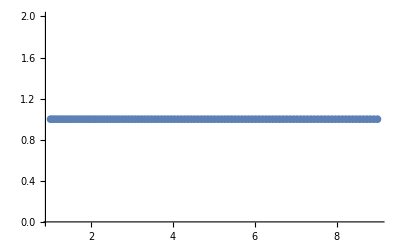

```mathematica
ListPlot[{#,1}&/@rgrid2,PlotRange->All]
```

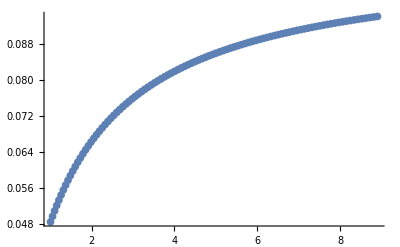

```mathematica
ListPlot[Table[{rgrid2[[i]],rgrid2[[i+1]]-rgrid2[[i]]},{i,1,Length[rgrid2]-1}],PlotRange->All]
```

```mathematica
PrevPoint[1,rgrid2]
```

-0.00115379

```mathematica
rgrid=Table[r,{r,0.1,5,0.1}];
```

```mathematica
Length[rgrid]
```

50

```mathematica
zgrid=Table[z,{z,-5,5,0.1}];
```

```mathematica
Length[zgrid]
```

101

```mathematica
hmattest=GenerateCylHamiltonian[rgrid,zgrid,2.0,True];
```

```mathematica
hmattest2=GenerateCylHamiltonian6[rgrid2,zgrid,2.0,True];
```

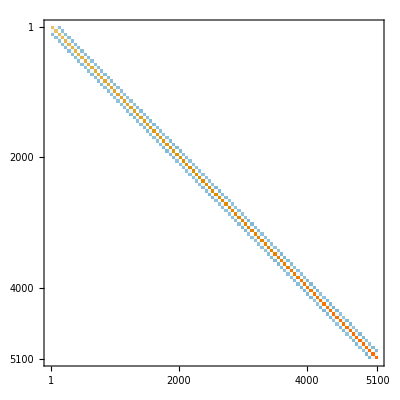

```mathematica
MatrixPlot[hmattest]
```

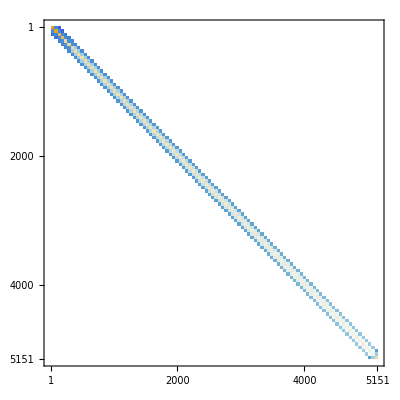

```mathematica
MatrixPlot[hmattest2]
```

```mathematica
Eigenvalues[hmattest,-30]
```

{3.60981,3.37641,3.22496,3.07194,2.98738,2.91681,2.62217,2.55108,2.39166,2.3081,2.29965,2.04327,1.98536,1.75096,1.71111,1.53738,1.3673,1.14595,1.13006,1.07091,-0.870869,0.751035,0.679409,0.635584,-0.475133,0.412056,0.285396,-0.188152,-0.0437853,0.0408283}

```mathematica
Eigenvalues[hmattest2,-30]
```

{3.36084,3.24977,3.17039,2.9594,2.95136,2.74972,2.47217,2.44775,2.31679,2.25811,2.11415,1.94808,1.79603,1.68351,1.63284,1.42263,1.25308,-1.11006,1.07593,1.06541,0.954815,-0.672592,0.634939,0.571379,0.54459,0.334242,-0.272469,0.225484,-0.116088,-0.07948}

```mathematica
testeig=Eigensystem[hmattest,-10];
```

```mathematica
functest=Table[{{rgrid[[Index1to2[i,Length[zgrid]][[1]]]],zgrid[[Index1to2[i,Length[zgrid]][[2]]]]},testeig[[2,1,i]]},{i,1,Length[rgrid]*Length[zgrid]}];
```

```mathematica
functestint=Interpolation[functest]
```

InterpolatingFunction[{{0.1, 5.}, {-5., 5.}}, <>]

```mathematica
testeig2=Eigensystem[hmattest2,-13];
```

```mathematica
testeig2[[1,1]]
```

-1.11006

```mathematica
functest2=Table[{{rgrid2[[Index1to2[i,Length[zgrid]][[1]]]],zgrid[[Index1to2[i,Length[zgrid]][[2]]]]},testeig2[[2,1,i]]},{i,1,Length[rgrid2]*Length[zgrid]}];
```

```mathematica
ListPlot3D[{#[[1]][[1]],#[[1]][[2]],#[[2]]}&/@functest2,PlotRange->All]
```

-Graphics3D-

```mathematica
functest2int=Interpolation[functest2]
```

InterpolatingFunction[{{0.1, 5.}, {-5., 5.}}, <>]

```mathematica
testnorm2=NormalizeWf[testeig2[[2,1]],rgrid,zgrid];
```

```mathematica
laplaciantest2=GenerateCylHamiltonian6[rgrid,zgrid,2.0,False];
```

```mathematica
vHtest2=LinearSolve[laplaciantest2,2Pi#^2&/@ testnorm2];
```

```mathematica
vHtest2int=Interpolation[Table[{{rgrid[[Index1to2[i,Length[zgrid]][[1]]]],zgrid[[Index1to2[i,Length[zgrid]][[2]]]]},vHtest2[[i]]},{i,1,Length[rgrid]*Length[zgrid]}]]
```

InterpolatingFunction[{{0.1, 5.}, {-5., 5.}}, <>]

```mathematica
potH0int=Interpolation[potH0]
```

InterpolatingFunction[{{0.1000000000000000055, 4.999999999999998224}, {-4.999999999999998224, 4.999999999999998224}}, <>]

```mathematica
Plot3D[{potH0int[r,z],vHtest2int[r,z]+(potH0int[5,0]-vHtest2int[5,0])},{r,0.1,5},{z,-5,5},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {5, 0} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
ntest=(laplaciantest2.(#[[2]]&/@potH0))1/(2Pi);
```

```mathematica
ntestint=Interpolation[Table[{{rgrid[[Index1to2[i,Length[zgrid]][[1]]]],zgrid[[Index1to2[i,Length[zgrid]][[2]]]]},ntest[[i]]},{i,1,Length[rgrid]*Length[zgrid]}]]
```

InterpolatingFunction[{{0.1, 5.}, {-5., 5.}}, <>]

```mathematica
Plot3D[ntestint[r,z],{r,0.1,5},{z,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[functestint[r,z],{r,0.1,5},{z,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[functest2int[r,z],{r,0.1,5},{z,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[functestint[r,z]/(√r),{r,0.1,5},{z,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
laplaciantest=GenerateCylHamiltonian[rgrid,zgrid,2.0,False];
```

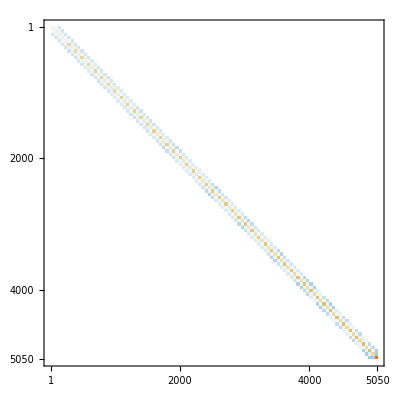

```mathematica
MatrixPlot[laplaciantest]
```

```mathematica
orb0int=Interpolation[orb0]
potHint=Interpolation[potH]
```

InterpolatingFunction[{{0.1, 5.}, {-5., 5.}}, <>]

InterpolatingFunction[{{0.1, 5.}, {-5., 5.}}, <>]

```mathematica
NIntegrate[orb0int[r,z]^2 r,{r,0.1,5},{z,-5,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.00084

```mathematica
datatemp=2Pi #[[1]][[1]](#[[2]])^2&/@orb0
```

{4.69439597286013459×10^-7,1.90938132608961205×10^-6,4.41593088676432647×10^-6,8.15467246296663074×10^-6,0.0000133702363305827665,0.0000204009073956013297,0.0000296990742823422889,0.0000418586800168650296,0.000057651254250364946,0.0000780726145138943332,0.00010440293448192272,0.00013828364978774601,0.000181815597964696876,0.000237683989054778812,0.00030931725409309804,0.000401088663069122331,0.000518571883461381674,0.000668864453370678627,0.000860996688506511621,0.00110644779329291108,0.00141979625634359424,0.00181953804223057063,0.00232911380709049553,0.00297819566299843031,0.00380429491204374775,0.00485476471532763954,0.00618928564131175623,0.00788293688906685725,0.0100299696400596924,0.0127484088467713612,0.0161856071331201157,0.0205248447558239205,0.0259929746053350704,0.0328688612022905578,0.041491703472684297,0.0522664611770893225,0.0656575652653448728,0.0821392126210221053,0.101969253977524758,0.12416063958692536,0.142137871321879545,0.143202720192894522,0.136588313690857791,0.128983468491215998,0.122074544616378609,0.116242232603309306,0.111543619822232062,0.107952366597069238,0.105425676910275843,0.103926002023050569,0.103428908935440583,0.103926001983196209,0.105425676826179854,0.107952366479789446,0.111543619669073738,0.116242232381566313,0.122074544358950112,0.128983468201984007,0.136588313328278594,0.143202719760054939,0.142137870828102728,0.124160639147282371,0.101969253604347221,0.0821392123043442638,0.0656575649966390193,0.0522664609459572459,0.0414917032778172039,0.0328688610287046352,0.0259929744637390322,0.0205248446427057443,0.0161856070389571116,0.01274840876240639,0.0100299695765207344,0.00788293684152542711,0.00618928561035670641,0.00485476468103031282,0.00380429488296852417,0.00297819563593736815,0.00232911378469557948,0.00181953802183738678,0.0014197962395308391,0.00110644777972571833,0.000860996678917272331,0.000668864443966987795,0.000518571875513507494,0.000401088657811645833,0.000309317249722295278,0.000237683985986504063,0.000181815595387235753,0.000138283648207846897,0.000104402933457828975,0.0000780726136927422077,0.0000576512536868161086,0.0000418586793572259029,0.0000296990738119659117,0.0000204009071047310255,0.0000133702363594864946,8.15467246277926813×10^-6,4.41593080349763196×10^-6,1.90938132142609855×10^-6,4.69439576439751111×10^-7,1.425061092003163858×10^-6,5.796036683956482829×10^-6,0.00001340403049218532904,0.000024750527749739685,0.00004057626516396201871,0.00006190529947623701305,0.00009010667684850956625,0.0001269771700783175677,0.0001748498162844094807,0.0002367344879353137988,0.0003164985508162549015,0.0004190979276886558438,0.0005508716611119030215,0.0007199165205413923029,0.0009365625215203508005,0.001213975515297869461,0.00156891958225977574,0.002022720060607931955,0.002602477895549026087,0.003342598020948358106,0.004286708850806531329,0.005490067064210302243,0.007022561819430078319,0.008972454786014052907,0.01145101685625751677,0.01459824615461805716,0.01858987136007339042,0.02364585045348258541,0.03004055047364307361,0.0381147043840632853,0.04828901649371432884,0.06107877787787006737,0.07710772857124895325,0.0971168828372893807,0.1219581817895145648,0.1525485434119360915,0.1897231665001088841,0.2338303617957908898,0.2836736492314827184,0.3340629425895585097,0.3725970791399531912,0.3863694289451467411,0.3814749018868600155,0.3686167444208173286,0.3539198865913090934,0.3401145113424963721,0.3283326500028303513,0.3190205492228135232,0.3123365575068668414,0.3083238123666196088,0.3069867518834330839,0.3083238122195542038,0.3123365572551918715,0.3190205488486537164,0.3283326495058248081,0.3401145106821596272,0.3539198858339383051,0.3686167435315655095,0.381474900869767072,0.3863694277618219745,0.372597077945059675,0.3340629414460502758,0.28367364821764032,0.2338303608864231725,0.1897231657422140972,0.1525485427387867043,0.1219581812250129105,0.09711688236582801466,0.07710772819520802005,0.06107877755197353687,0.04828901620470903165,0.0381147041466822359,0.03004055027010970932,0.02364585030306982717,0.01858987123977465195,0.01459824605032871872,0.01145101676258436517,0.008972454705713093539,0.007022561749611113633,0.005490067006425987096,0.004286708801556037225,0.003342597985173680919,0.002602477863123764925,0.002022720032505847649,0.001568919562629057727,0.001213975501041034802,0.000936562510611626365,0.0007199165107922224138,0.0005508716535697917666,0.0004190979220991055843,0.0003164985458932294907,0.0002367344848510939092,0.0001748498137805887971,0.0001269771674816809596,0.00009010667527036398351,0.00006190529846124983042,0.00004057626477989612254,0.0000247505278303079897,0.00001340403013683773799,5.796036588752463559×10^-6,1.425061043878762815×10^-6,2.619958439796275176×10^-6,0.00001065531229514084935,0.00002463926214257170663,0.00004549014636395267148,0.00007456397247531232912,0.0001137345872566383371,0.0001655057922701716565,0.000233161626161010397,0.0003209633189847568463,0.0004344040365667077312,0.00058053583508446865,0.0007683871383892885973,0.001009493984628448473,0.001318574235270687105,0.001714381405612120542,0.002220783761736165499,0.002868125419198149157,0.003694939600411531959,0.0047501001200417018,0.006095516247519472119,0.007809497828048930559,0.009990942250923977182,0.01276452122652919219,0.01628707091311525683,0.02075540991307325922,0.02641581644647759927,0.03357537296549733575,0.0426153032124643618,0.05400622692223833867,0.06832483550263074078,0.0862706416529701275,0.1086797755289157879,0.1365294698156655508,0.170920215979714164,0.2130091120443812894,0.263840788543850944,0.3239700157781535123,0.3926856439310953106,0.46659581600910585,0.537747108633284867,0.5935413552227059201,0.6237108892862799338,0.6302844859497374886,0.6220771700336355605,0.6070267259620770771,0.5902185309919103735,0.5745080481869443432,0.5614093079480099855,0.5516986257831955197,0.5457590549153259563,0.5437629130407919968,0.545759054685805791,0.5516986253213687792,0.5614093072796916277,0.5745080473064884793,0.5902185298590381559,0.6070267246388064719,0.6220771684902565809,0.6302844841938085837,0.6237108874390397566,0.5935413533608392184,0.5377471068616725653,0.466595814353824512,0.3926856424454812823,0.323970014496213072,0.2638407874196607231,0.213009111090075084,0.1709202151642386086,0.1365294691331990192,0.1086797749611358947,0.08627064116801902708,0.06832483509587204701,0.0540062265818313389,0.04261530294271489177,0.03357537275653452208,0.02641581627494198322,0.0207554097490400805,0.01628707077354252696,0.01276452110645059433,0.009990942152634883936,0.007809497743474687967,0.006095516181642407646,0.004750100061962115841,0.003694939546588189998,0.002868125381915501099,0.002220783734707886295,0.00171438138759117116,0.0013185742186417018,0.001009493970262806183,0.0007683871263173809668,0.0005805358246561018244,0.0004344040287088760931,0.0003209633118389387391,0.000233161620726983015,0.0001655057869220065943,0.000113734584652969311,0.00007456397134709585363,0.00004549014626494608985,0.00002463926197164687768,0.00001065531221442013727,2.619958341485898361×10^-6,3.945304657575842689×10^-6,0.00001604412096136940544,0.00003709516074012542584,0.0000684736150639302283,0.0001122091169057192207,0.0001711046800588939191,0.0002489028677587401899,0.0003505082866351780206,0.0004822787181667829278,0.0006524010573461303458,0.0008713728142333126802,0.001152615571976231248,0.001513253591145050808,0.001975099105214593029,0.002565895995775783732,0.003320885721857788614,0.004284774061743461815,0.005514194403684182265,0.007080783530289235564,0.009075008082347226917,0.01161090464203035072,0.014831920561340926,0.01891806423973304725,0.02409458500999989836,0.03064239405030539128,0.03891038758329815043,0.04932970862258553059,0.06242972137032606134,0.07885496695969312525,0.09938143062812563342,0.1249287427195589998,0.1565618607291198679,0.1954702929270621124,0.2429032746290280319,0.3000229433191835977,0.3676122172907507669,0.4455441140832243561,0.5319187647726515996,0.6219274702462553813,0.7070853463633749156,0.7765669573720830399,0.8222241809103878385,0.8437256797526358297,0.846810716036623294,0.8386546760235441794,0.8251848539044911382,0.8105067397505634812,0.7972209084169767081,0.7868872094878696414,0.7803913476457343689,0.77818074559861018,0.7803913473280287514,0.786887208892223328,0.79722090751073636,0.8105067385011917775,0.8251848524074136614,0.8386546741596957166,0.8468107139417274556,0.8437256774467400965,0.8222241785099743735,0.7765669549548075916,0.7070853440471332975,0.6219274680728696217,0.5319187628030176674,0.4455441123584339409,0.3676122157295081291,0.300022941959787167,0.2429032734807131686,0.1954702919537286761,0.1565618599189316381,0.124928742041418417,0.09938143008801668434,0.07885496648852814519,0.06242972100258511172,0.04932970832995202748,0.03891038734731240735,0.03064239384029566665,0.02409458482185395083,0.01891806407061190173,0.01483192042062836892,0.01161090452441835972,0.009075007983159447439,0.007080783441452505383,0.005514194329565033856,0.004284774003546290979,0.003320885686408937816,0.002565895967712312048,0.001975099078810441689,0.001513253566549820677,0.001152615551372015668,0.0008713727951537566073,0.0006524010421881992278,0.0004822787068237211468,0.0003505082756163760907,0.0002489028591208519494,0.0001711046750276413148,0.0001122091150268838504,0.00006847361452111580321,0.00003709516068690693849,0.00001604412081659895083,3.945304556595752675×10^-6,5.327089566173004141×10^-6,0.00002166100646014346137,0.00005007289283647069057,0.00009240623744711262978,0.0001513801925515982236,0.0002307470865774163123,0.0003355122641083928446,0.000472227955162293051,0.0006493771157148878434,0.0008778679397364053073,0.001171665657625751316,0.001548595109670894629,0.00203135605407105817,0.002648803245333552519,0.00343755539077233658,0.004444011375455735999,0.005726868669304130164,0.007360257780734905,0.009437627282213486844,0.01207653557657569326,0.01542452580425366519,0.01966627565491564874,0.02503221704450120109,0.03180880058792856182,0.04035051614830215242,0.05109364222993809185,0.0645714279671098324,0.0814299246805824067,0.1024428337939171145,0.1285222880623303476,0.1607200609099234944,0.2002097383326426024,0.2482341115478773494,0.3059926681968653794,0.3744316659126860673,0.4538877975517520662,0.5435412903569055509,0.6406970596116549199,0.7401116073511386167,0.8339702195604681669,0.9134250135210691605,0.9718694801948059306,1.007801400331708593,1.024447802781476221,1.027269122015967121,1.021757336143082243,1.012381980249191738,1.002382644490913154,0.9939322130249600645,0.9883799840094666975,0.9864530233932992143,0.9883799837160615391,0.9939322123764613504,1.002382643385921797,1.012381978830658164,1.021757334301660224,1.027269119890363017,1.024447800301059916,1.007801397688943012,0.9718694773238564009,0.9134250107082099805,0.8339702167651410967,0.7401116047773788306,0.640697057280370538,0.5435412882606902293,0.453887795651085033,0.3744316642356064067,0.305992666745639536,0.248234110347826579,0.2002097373055812517,0.1607200600756844269,0.1285222873539626429,0.102442833204062527,0.08142992419108069236,0.0645714275850534549,0.05109364192105222276,0.04035051586420481615,0.03180880034424579306,0.02503221684349989334,0.01966627547634649047,0.01542452565147087293,0.01207653544255054587,0.009437627164992717967,0.007360257680567660948,0.00572686859971731802,0.004444011322374297364,0.003437555347853214826,0.002648803208207106976,0.002031356021265382784,0.001548595080625222619,0.001171665633126445089,0.0008778679201888458927,0.0006493770991982779521,0.0004722279413825847377,0.0003355122523802083691,0.0002307470802480727237,0.0001513801890050181118,0.00009240623695571047689,0.00005007289229761033119,0.00002166100635688481989,5.327089413804597596×10^-6,6.706960290040693911×10^-6,0.00002726827116416536998,0.00006302136389466933094,0.0001162668788180672016,0.0001903957805058337947,0.0002900830465200923847,0.0004215576118953177017,0.0005929625596870632376,0.0008148244958879609674,0.001100656660372868822,0.001467727066369795679,0.001938030864349543348,0.00253951555121421343,0.003307618785745192782,0.004287191483905464461,0.005534893783998636084,0.007122168070237849563,0.009138911038749508705,0.01169798486705815213,0.01494072318554475494,0.01904359787267005258,0.02422621040055351146,0.03076074661129892669,0.03898296972450222608,0.04930469489491989268,0.06222744926622143166,0.07835660574151830435,0.09841458742842779873,0.1232506199354675675,0.1538427431582023601,0.1912850930149509901,0.2367495044789084223,0.2914050837171771004,0.356273018014825543,0.4319889217955982272,0.5184484172303766685,0.6143390842890348349,0.7166398488396336122,0.8203194764998988046,0.9186431409725010414,1.00447376630778343,1.072375117381039815,1.120333383468046729,1.149845996174989487,1.164646887854652254,1.16918912824326962,1.167603596852406609,1.16322644146152508,1.158502214961670841,1.155056997636338688,1.153809844686726922,1.155056997311649281,1.158502214231155568,1.163226440293729635,1.167603595278587568,1.169189126292232057,1.164646885507890741,1.149845993528758491,1.120333380652436457,1.072375114363109072,1.004473763185210098,0.9186431378592476199,0.8203194736387369599,0.7166398462218048876,0.6143390819708381805,0.5184484150858481577,0.4319889199190046719,0.3562730164500450083,0.2914050823752052442,0.2367495033195524491,0.1912850920399436904,0.1538427423328784523,0.1232506192334891538,0.09841458683097594531,0.07835660525428235997,0.06222744886571917338,0.04930469455433744136,0.03898296943330786756,0.03076074637730020884,0.02422621019518298082,0.01904359770442178144,0.01494072303169506228,0.01169798473271555895,0.009138910925823143691,0.007122167979297025132,0.005534893718761562755,0.00428719142545889268,0.003307618735558833634,0.002539515507487879601,0.001938030826120361938,0.001467727036787884226,0.001100656636671716684,0.0008148244761288765836,0.0005929625434019146939,0.0004215575989384253253,0.0002900830390105962265,0.000190395775801499398,0.0001162668768987688487,0.00006302136309804028736,0.00002726827047623420914,6.706960117831735664×10^-6,8.036634958675501595×10^-6,0.0000326692930551908168,0.00007548492217395173412,0.000139211789500592076,0.0002278677156827300714,0.0003469857854911090093,0.0005039284052408100283,0.0007083054768934113838,0.000972517858831404685,0.001312453498743082813,0.001748370863454936516,0.002306012651591232282,0.003018002671508813444,0.003925589932160150531,0.005080816852157341708,0.006549202476916400405,0.008413046375065923693,0.01077547328827067934,0.01376535071859778883,0.0175432179995538715,0.02230836089916249255,0.02830714116139161913,0.03584263297441854955,0.04528550634610785005,0.0570859007747849485,0.07178570336668545111,0.0900301180046502982,0.1125765912858981665,0.1402979236668268418,0.1741745932770965543,0.2152688269537555375,0.264669761241033416,0.3233955309011384889,0.3922356273277726516,0.4715186246573088096,0.5608028534709727499,0.6585209903889597302,0.7616734973738060886,0.8657530395511235132,0.9651356830410285103,1.054071366011435229,1.128050390400095375,1.184901316284974462,1.225012792199429257,1.250707922913409237,1.265279027050117097,1.272148557335722964,1.274341734365674125,1.274242429051028663,1.273527376624376498,1.273181157459602794,1.273527376254714483,1.274242428234905768,1.274341733199243579,1.27214855574873734,1.265279025065583114,1.250707920523494129,1.225012789545445403,1.184901313346310408,1.128050387315703694,1.054071362874405668,0.96513567986626232,0.8657530365008078883,0.7616734946409961841,0.6585209879081760446,0.5608028512765148701,0.4715186226893048503,0.3922356256621735188,0.3233955294853049913,0.2646697600063266367,0.2152688259063025081,0.1741745923914772792,0.1402979229097805727,0.1125765906467214468,0.09003011747763005086,0.07178570295003277335,0.05708590040858709429,0.04528550603356575474,0.03584263271462188609,0.02830714094498829445,0.02230836071152211352,0.01754321783119276638,0.01376535056838363835,0.0107754731620550441,0.008413046271076634283,0.00654920239301344417,0.005080816780477166853,0.003925589869321396666,0.003018002617662128366,0.002306012604844028891,0.001748370825257180127,0.001312453472323258399,0.0009725178374404134277,0.0007083054589278485987,0.0005039283904450627488,0.0003469857759562132677,0.0002278677100219440114,0.0001392117859117212339,0.00007548492058971417275,0.00003266929187274889642,8.036634570993105553×10^-6,9.276063814864990569×10^-6,0.00003770107592309398392,0.00008708622623008333215,0.000160543234905881637,0.0002626501923671514325,0.0003997038506485745281,0.0005800700689513951125,0.0008146492673204485894,0.001117479548212357014,0.001506506474921599049,0.002004556016378776368,0.002640555394717834936,0.00345105635461340601,0.004482125824993833764,0.005791680629616134792,0.007452354822156443663,0.009554999603103353413,0.01221292497144629012,0.01556699640348835662,0.0197916948299666495,0.02510222668946184996,0.03176272364271595647,0.04009548175475960425,0.05049103758091124295,0.06341862968949097977,0.07943620736322314085,0.09919856398684048725,0.1234613222995119865,0.1530773066176896084,0.1889802515334398691,0.2321488520142207944,0.2835421083883226548,0.343995476812761031,0.4140680692229569937,0.4938369380070286462,0.5826496661010224515,0.6788755171191238208,0.7797379878168737674,0.8813526760525881711,0.9790939337469858909,1.068317480190721605,1.145265512253424954,1.207796640388695345,1.255621806800408993,1.290014139416032182,1.31322059655256975,1.327848958201312079,1.33639561274810058,1.3409533924594494,1.343064732242887694,1.343664443509368949,1.343064731793178892,1.340953391582718946,1.336395611572373351,1.327848956650425484,1.313220594550402948,1.290014137082166926,1.255621804154945624,1.20779663756019647,1.145265509199630742,1.068317477107192083,0.9790939306691071952,0.8813526731406460057,0.779737985106326412,0.6788755147239165579,0.5826496639598042992,0.4938369360878254405,0.4140680675446315966,0.3439954753451335907,0.2835421071082421144,0.2321488509282752875,0.1889802506392664911,0.1530773058375837861,0.1234613216667513417,0.09919856346697895328,0.07943620693448242738,0.06341862931178046806,0.05049103726331320665,0.04009548148984459689,0.03176272341440495172,0.02510222649423976842,0.01979169466367633217,0.01556699625962419279,0.01221292483775403501,0.009554999489411679932,0.007452354727727202136,0.005791680551291402277,0.004482125755340029366,0.003451056294063669211,0.002640555340657337104,0.002004555975147282673,0.001506506446205446155,0.001117479521192184877,0.000814649245600854298,0.0005800700504405093438,0.0003997038399672342249,0.0002626501848565280928,0.0001605432306262895647,0.00008708622378516679762,0.00003770107491403609152,9.276063347970705355×10^-6,0.00001039283326524850898,0.00004223183612894978997,0.00009752070751449147485,0.0001796993837441277019,0.0002938234053616145055,0.0004468365587540918756,0.0006479488369528635612,0.0009091370992984883545,0.001245791626139491767,0.001677538117335628007,0.002229271905723803392,0.00293244906219988311,0.00382668794141171433,0.004961744017818534062,0.006399930466408043599,0.008219065887916386774,0.01051603772374988696,0.01341107261243842738,0.01705280065601635836,0.02162418335351959023,0.02734933789333421853,0.03450122250108457394,0.04341003308463509242,0.05447197985127871988,0.06815783549104883069,0.0850202382381576919,0.1056981548029449461,0.1309161172135186828,0.1614748273897853903,0.1982285016654219297,0.2420430615237014823,0.2937283497167943823,0.3539377495784432528,0.4230312704146253879,0.5009053312649209379,0.5868062962570139974,0.6791660407332643674,0.7755224227507442129,0.8726023887566962983,0.9666278135127680573,1.053834132409463221,1.131081548248470315,1.196354678146760104,1.248972619263100505,1.289469155753230494,1.319243989842951259,1.340138678833252593,1.354057585060233021,1.362688994505232438,1.367328956631981482,1.368784533831629416,1.367328956213446183,1.362688993652049113,1.354057583819858787,1.340138677234851181,1.319243987904066816,1.289469153508825028,1.248972616754632257,1.19635467548081566,1.131081545415775439,1.053834129548754736,0.966627810690157417,0.8726023860388488041,0.7755224201952561118,0.6791660384766946697,0.5868062942845540972,0.5009053294624755054,0.4230312687857730733,0.3539377481346378174,0.2937283485000930114,0.2420430604714354913,0.1982285007637948382,0.1614748266037180091,0.1309161165504189169,0.1056981542602830931,0.08502023779616430153,0.06815783510041864193,0.05447197952653315205,0.04341003280205719135,0.03450122226225063264,0.02734933769666642448,0.02162418318726630809,0.01705280051310989286,0.01341107248201653932,0.0105160376113694853,0.00821906579481483795,0.006399930384203098275,0.004961743948740516831,0.003826687880924402152,0.002932449009506046637,0.002229271862766213143,0.001677538084614342291,0.001245791597753154455,0.0009091370754263777677,0.0006479488186989700982,0.0004468365463938347893,0.0002938233969333549735,0.0001796993789345916881,0.00009752070497269744285,0.00004223183463883799256,0.0000103928327609656643,0.00001136195062280801179,0.00004616012368635164176,0.0001065545338077913139,0.0001962505092225754544,0.0003206872532527952097,0.000487324197897756406,0.0007060371393801627982,0.0009896414369253540636,0.001354565205450556351,0.001821701536654416751,0.002417475414762665019,0.003175168225993930034,0.004136550329718911334,0.005353879745911742518,0.006892332228434719172,0.00883293330922319887,0.01127606532972074821,0.01434561898496073677,0.01819384582618885788,0.02300694077754463997,0.02901133321877309245,0.03648058233882324561,0.0457426422739080405,0.05718706775037632055,0.07127144868267490382,0.0885259702677796365,0.1095544687559851942,0.135029687801807527,0.1656796531662815013,0.2022612702115934802,0.2455166132565783325,0.2961073275831970027,0.3545237766348164769,0.4209690179774526453,0.4952244842429252414,0.5765150619828985902,0.6634051224349391858,0.7537696096841307257,0.8448865992235197532,0.9336784417661796812,1.017082210651611014,1.092469518404459479,1.157995684579917409,1.212773976459762699,1.256840296318942756,1.29095157740296656,1.316302362884754568,1.33423965033706588,1.346025921776609063,1.35266807388041045,1.354808719668118,1.35266807346761907,1.346025920993157443,1.334239649185044317,1.316302361422083323,1.290951575561693227,1.256840294197115063,1.212773974199406951,1.157995682151134307,1.092469515868774259,1.017082208082077521,0.9336784392832639249,0.844886596765150219,0.7537696073904910206,0.6634051203656104967,0.5765150601612274044,0.4952244825597635979,0.4209690164586223045,0.3545237753307328476,0.2961073264670865727,0.2455166122845657081,0.2022612693358737311,0.1656796524128650736,0.1350296871365286197,0.1095544682151393636,0.0885259698049330102,0.0712714483325734936,0.05718706742898829759,0.04574264200974989248,0.03648058210322384601,0.02901133303168685727,0.02300694062334443023,0.0181938456885733783,0.01434561885896292653,0.01127606522192244174,0.00883293321405077004,0.006892332151319965498,0.005353879680490193761,0.004136550270807052006,0.00317516817807334307,0.002417475372616622762,0.001821701503418787389,0.001354565177347860628,0.0009896414127058583469,0.000706037121298044004,0.0004873241866048325336,0.0003206872455812495555,0.0001962505041282487027,0.000106554531216217562,0.00004616012258546542223,0.00001136195006768492738,0.00001216566458032779094,0.00004941407907841992812,0.0001140228231287830288,0.0002098955366816805357,0.0003427553205570033203,0.0005204381728207638443,0.0007532980154079042126,0.001054739955519334008,0.001441903736168399501,0.001936524963527747748,0.002566007586958574539,0.003364747273410906347,0.004375751495885590666,0.00565260765733336902,0.007261855178640986553,0.009285819202704162482,0.0118259613626686073,0.01500679372321714686,0.0189803819091120511,0.02393142763079667424,0.03008286134234191652,0.03770178461001382047,0.04710546581194768915,0.05866689959661652908,0.07281917469324435249,0.09005754374353150459,0.1109376487093285616,0.1360678398915151302,0.1660929868027136962,0.201666730616224905,0.2434089838207701435,0.2918459929874969295,0.3473319443725937246,0.4099544948674033066,0.479432219561266317,0.5550196493200986521,0.6354438936384727616,0.7189023528090639534,0.8031483702475737558,0.885675733227307442,0.9639833968867790885,1.035867994437133205,1.099671589983506899,1.154421277188181663,1.199833959563625477,1.23620351720690522,1.264216233606288354,1.284745485551848709,1.298664545894695014,1.306698515287665844,1.309321682959510079,1.306698514930991339,1.298664545180285669,1.284745484539035091,1.264216232317561434,1.236203515639076312,1.199833957736675507,1.154421275163457804,1.099671587919905682,1.035867992225204308,0.9639833946831598397,0.8856757310776471316,0.8031483681068681795,0.7189023507395249593,0.6354438917851428572,0.5550196476302642916,0.4794322180178530722,0.4099544935023220231,0.3473319432008573033,0.291845991984711955,0.2434089829357854167,0.2016667298379604332,0.1660929861178108153,0.1360678392948462239,0.1109376482234889564,0.09005754331933682466,0.07281917435058985699,0.05866689930165059933,0.04710546555850777687,0.03770178439648961313,0.0300828611645342834,0.02393142747880512737,0.01898038177459826927,0.01500679360139781067,0.01182596126080908432,0.009285819111865601371,0.007261855101111568938,0.005652607595391419352,0.004375751446645226815,0.003364747233091535937,0.002566007549498114045,0.001936524933213271063,0.001441903710126981713,0.001054739934742774568,0.0007532980013940204562,0.0005204381621155408149,0.0003427553127178275177,0.0002098955323058036274,0.0001140228211345672722,0.00004941407797071324096,0.00001216566409659541491,0.0000127931750735120637,0.00005195022552162566465,0.0001198267560617905107,0.000220456445783687161,0.0003597451423313678872,0.0005457650818934006266,0.0007891600464314376103,0.001103677017361913562,0.001506844759545804772,0.002020824689532605326,0.002673464525864809461,0.003499590049194216653,0.004542575031908324241,0.005856232828471849389,0.007507074974226861268,0.009576980791543715134,0.01216631547279382235,0.01539752029168375867,0.01941917290135558569,0.02441047487417289869,0.03058605925102169299,0.03820091808883505702,0.04755511742973849705,0.0589977874361279749,0.072929640303170155,0.08980297479649336525,0.1101177834674421448,0.1344122137099709044,0.1632453119034622213,0.1971698158818829893,0.2366929400887437687,0.2822238863231562436,0.3340085297515983123,0.3920546692823376401,0.4560554734091147814,0.5253238492233491683,0.5987550993471028025,0.6748370398256044969,0.7517227758755031564,0.8273695138175181477,0.8997282749051540602,0.9669501553623014157,1.027564202810957832,1.080587235297821111,1.125545986643217849,1.162417201822779607,1.191510377240440354,1.213324887861710747,1.228409603926955616,1.237244069530353802,1.240151082550456596,1.23724406918181022,1.228409603305704245,1.213324887001111754,1.19151037626580731,1.16241720051929405,1.125545985076559161,1.080587233606564432,1.027564201028500093,0.9669501535401589857,0.8997282730547638068,0.8273695120069255679,0.751722774056548217,0.6748370381073425505,0.5987550977372943265,0.5253238477612994785,0.4560554721017006188,0.3920546681147956364,0.3340085287477131263,0.282223885465835959,0.2366929392930197374,0.1971698152064304526,0.1632453113209705299,0.1344122131896885203,0.1101177830215032135,0.08980297442452982385,0.07292963999219185977,0.0589977871826205131,0.04755511720362530782,0.0382009178996372603,0.03058605908254967504,0.02441047473985018614,0.0194191727793100128,0.01539752017777687369,0.01216631538127738455,0.009576980702299552408,0.007507074905286566087,0.005856232771440737899,0.004542574989874185907,0.003499590012596739201,0.0026734644941578749,0.00202082466673393516,0.001506844739674198614,0.001103677003966010704,0.0007891600355906383783,0.0005457650739668054867,0.0003597451352742059126,0.0002204564413826173553,0.0001198267536692379038,0.00005195022447759797645,0.00001279317487272040638,0.00001324018193130945218,0.00005375159999060922727,0.0001239291221734020526,0.0002278697202852045925,0.0003715634853659141975,0.0005631829276273344016,0.0008134803875930393132,0.001136307723127139159,0.001549276699859540789,0.002074582821742133204,0.002740019372246074677,0.003580212272516129809,0.00463810932946761482,0.005966759040343509601,0.007631413732175146453,0.00971198734209486535,0.01230588880798746232,0.01553123437870994466,0.01953041376275355516,0.02447394108663946509,0.03056445773293795328,0.03804066418810913557,0.04718083640512586,0.05830542400445353033,0.0717780303456050842,0.08800384402898001436,0.1074243415785389501,0.1305068495039164487,0.1577274018751129997,0.1895453595665958916,0.2263686137205941629,0.268509056923534358,0.3161295536784727853,0.3691859785175114496,0.427370909466343067,0.4900687731659346405,0.5563346219166808228,0.6249087872221075002,0.6942758671161675396,0.7627681853412984248,0.8287022868302110322,0.8905258690135534519,0.946946736757395322,0.9970183857678387211,1.04016809668252007,1.076168244554339951,1.105063990220196168,1.12707687028482076,1.142503808897065896,1.151626958359739602,1.154644382551016271,1.15162695803646405,1.142503808285249217,1.127076869512637731,1.10506398933985665,1.07616824355233012,1.040168095377944115,0.997018384385704873,0.9469467352961855287,0.8905258675917269223,0.8287022853272286232,0.7627681838998437657,0.694275865639842316,0.6249087858142241051,0.5563346206257027232,0.4900687720504008556,0.4273709084430210249,0.3691859776228326957,0.3161295528924174492,0.2685090562494909467,0.2263686131355813455,0.1895453590481229051,0.1577274013853426122,0.1305068490551091458,0.1074243411778651218,0.08800384369659534866,0.07177803008937867151,0.05830542377427080675,0.04718083621570968729,0.0380406640230052814,0.03056445759873793751,0.02447394097290182581,0.01953041366331086426,0.01553123427979797354,0.01230588871999772704,0.009711987266112212821,0.007631413667415931276,0.005966758991546307013,0.004638109290018326763,0.003580212243734283941,0.002740019345585522987,0.002074582802318841898,0.001549276688606654983,0.001136307713003542251,0.0008134803797188277396,0.0005631829195876522086,0.0003715634783440653282,0.0002278697156085630314,0.0001239291195659350415,0.00005375159901819466016,0.00001324018155314346597,0.00001350826838590147491,0.00005482521076980210934,0.0001263483024110720132,0.000232174868922730829,0.0003782867539250653536,0.0005728297754427549314,0.0008264966651096590077,0.001153026004693293365,0.001569833393193457303,0.002098794557549854138,0.002767203296683105442,0.003608929769730172192,0.00466580614582448944,0.005989266717528644712,0.007642266860671996602,0.009701499062702619279,0.01225991219583084904,0.01542952090991877348,0.01934446208879691668,0.02416421179088207459,0.03007681500996006977,0.03730189858134975441,0.04609313049189344044,0.05673965628908710021,0.0695658864809106742,0.08492883719963809993,0.1032120594036985567,0.1248150640084540935,0.150137119485589468,0.1795544422270669842,0.213390223663278276,0.2518777495800283957,0.2951181515570919536,0.3430360863095742929,0.3953386944055032866,0.4514851216180095588,0.5106749810830895271,0.5718635030806867373,0.6338080063150968709,0.6951446244458046169,0.7544869554982391846,0.8105316749943932597,0.8621528295116178039,0.90846826550504559,0.9488681472064603237,0.9830043895731329217,1.010747923889075249,1.032125718726546932,1.047250782339566539,1.056256814743744721,1.059246190028324836,1.056256814503207489,1.047250781783800061,1.03212571795613081,1.01074792318296288,0.9830043886865515843,0.9488681461952772582,0.9084682644152323955,0.8621528284724073323,0.8105316739708691312,0.7544869543949140108,0.695144623303710257,0.6338080051795013516,0.5718635020094411258,0.5106749800925195891,0.4514851207628015678,0.3953386936605924899,0.3430360856601780524,0.295118150993957038,0.2518777490962877355,0.2133902232654192986,0.1795544418751998091,0.1501371191710892111,0.1248150636735904557,0.103212059112974283,0.08492883697136699936,0.06956588629615274867,0.05673965614045648806,0.04609313035202946079,0.03730189845800451257,0.03007681491155975726,0.02416421170376137686,0.01934446201162464893,0.01542952083135400007,0.01225991212106747485,0.009701498997073187534,0.007642266804802456293,0.005989266671592203514,0.00466580611111633663,0.003608929739336567143,0.00276720327363942781,0.002098794541319284754,0.001569833384154096825,0.00115302599782006826,0.0008264966581670767916,0.0005728297694798176322,0.0003782867475294597712,0.0002321748638092953258,0.0001263482993111515909,0.00005482520949509515278,0.00001350826806736262426,0.00001360414679004308538,0.0000551989315058441996,0.0001271509420952985647,0.0002335005312599940872,0.000380137448097359719,0.000575066422763641537,0.0008287701808579494066,0.001154680649448643086,0.001569772264971648925,0.002095293973691433017,0.002757658907236894868,0.003589512157841553555,0.004630997494982247597,0.005931242456489711637,0.007550077097759559874,0.009559993967465484946,0.01204834364368832429,0.01511974007376304346,0.01889862040951022896,0.02353186289887312102,0.02919131066165985707,0.03607597731248122291,0.04441362011973536906,0.05446126026822323265,0.06650411026982477214,0.08085224960294200379,0.09783428699281638444,0.1177871973895080843,0.1410415645503079989,0.1679016598185739714,0.1986202067229431699,0.2333683831322603204,0.2722026208631444845,0.3150310291851929246,0.3615836211617112932,0.4113916363593498437,0.4637816566407962579,0.5178893964353183459,0.5726956667267574519,0.6270831559175502116,0.6799080753632027294,0.7300767029589718406,0.7766148869294679365,0.8187195797486633887,0.8557852952460990689,0.8874037822248356542,0.9133404604611153291,0.9334948653191462464,0.9478539113218351897,0.9564464408837947744,0.9593059636522916869,0.9564464406820213269,0.9478539109127112274,0.9334948647260721413,0.9133404598261295562,0.8874037815486774838,0.855785294503340566,0.8187195789654987896,0.7766148861946783714,0.7300767022272011696,0.6799080746033787252,0.6270831551355820225,0.5726956659520469793,0.517889395641238292,0.4637816559558762549,0.4113916357961602578,0.3615836206416209256,0.3150310287157708809,0.2722026204781316384,0.2333683827926113982,0.1986202064823653882,0.1679016596134050198,0.1410415643736690789,0.1177871971968771035,0.0978342868388487538,0.0808522494668581534,0.06650411016884886303,0.05446126016303437983,0.04441362003977813434,0.03607597722550642956,0.02919131059434480957,0.02353186282820298169,0.01889862035620868542,0.01511974002334600741,0.01204834359325913334,0.009559993916810295948,0.007550077054122140142,0.005931242422633331663,0.004630997468591176849,0.003589512131195300924,0.002757658887928846193,0.002095293959344830872,0.001569772254771604232,0.001154680642922043965,0.0008287701737918609603,0.0005750664171654282465,0.0003801374425516117338,0.0002335005267331294488,0.0001271509388975548787,0.00005519893082932225361,0.00001360414675199054875,0.00001353880448558107936,0.00005491799294211280177,0.0001264437050617228719,0.0002320489185388343666,0.0003774579547687568649,0.0005704351220206935351,0.0008211236581814149372,0.001142484076921594731,0.001550843375690380951,0.002066568787344596831,0.002714881140069791982,0.003526823638152746975,0.004540401141246205381,0.00580190266015776862,0.007367414584484214286,0.009304523616790572262,0.0116941946759215816,0.01463278939141508238,0.0182341629131548665,0.02263173920298484909,0.02798041643097318375,0.03445809297297984267,0.04226653174253510202,0.05163119820255730192,0.06279962176839992096,0.0760377521740405917,0.09162372953674224508,0.1098384859222122935,0.1309526809995243251,0.1552096861229311079,0.1828047094750061437,0.2138607277670093459,0.2484026507672195223,0.286332031299249675,0.327405498921845639,0.3712207082961517751,0.4172136538277356024,0.4646704264819772396,0.5127547356876854613,0.5605499250176823433,0.6071112788374771246,0.6515219350757797703,0.6929445175347905456,0.7306611838248728313,0.7640970760974677256,0.7928254939400826991,0.816556525450686306,0.835113512401570058,0.8484031380445400801,0.856385094112904926,0.8590465197611876523,0.8563850939451377502,0.8484031376809638314,0.8351135119985502038,0.8165565250008712181,0.7928254935039571092,0.7640970755832208205,0.7306611833592686877,0.6929445170450053719,0.6515219346406213928,0.6071112783486438773,0.5605499245640395319,0.5127547351562802926,0.4646704260120480641,0.4172136533958169937,0.3712207079567454188,0.3274054986301323103,0.2863320310365158824,0.2484026505378581177,0.213860727574035734,0.1828047093636550241,0.1552096860470750936,0.1309526809484055676,0.1098384858663043825,0.09162372948357531071,0.07603775212428676475,0.06279962171848521964,0.05163119814929752457,0.04226653170633927388,0.03445809293277317582,0.02798041638868843688,0.02263173916810306362,0.01823416288887883172,0.01463278936509760003,0.01169419464065705964,0.009304523585393716628,0.007367414557330983071,0.005801902635673347209,0.004540401122833081189,0.003526823622177910044,0.002714881126128503786,0.002066568775676430293,0.001550843366621126822,0.001142484069772304829,0.000821123653392292202,0.0005704351163107930614,0.0003774579513231365072,0.000232048914779950699,0.0001264437039055442095,0.00005491799263519722434,0.00001353880466369050034,0.00001332659533759085242,0.00005404125746677309571,0.0001243645546494290852,0.0002280794255757916792,0.0003706831091100360939,0.0005596166479780890708,0.0008045769872068947016,0.00111791898359108389,0.001515156671598147128,0.00201557450903722891,0.002642960250147536497,0.003426470991804815003,0.004401642477928817848,0.005611548728835275979,0.007108113211758923796,0.008953563975832740659,0.01122201180136770773,0.01400111179776345064,0.01739374367328569579,0.02151961286123547055,0.02651663342926671913,0.03254190397514118719,0.0397720303275388654,0.04840248829298958104,0.05864566052937406872,0.07072713571381345058,0.08487983915119057294,0.1013355926331293833,0.1203138036275781991,0.1420071832529652726,0.1665647137525771598,0.1940725350730218808,0.2245339779375793453,0.2578505765767573986,0.2938064357110359973,0.3320586425208044976,0.3721363233056656523,0.4134502899185143971,0.4553139599311941416,0.4969744913838335288,0.5376511836743099834,0.5765766353513969371,0.6130353958751312385,0.6463951848785508503,0.6761271445958828021,0.7018136715773122527,0.7231445996183308064,0.7399043496168085513,0.7519537981805577965,0.7592109543565232715,0.7616341905161575535,0.759210954251626067,0.7519537979868632455,0.7399043494073823325,0.7231445994107938934,0.701813671361557123,0.6761271443312800434,0.6463951846075331998,0.6130353956404412832,0.5765766351311817838,0.5376511834580512856,0.4969744911535766622,0.4553139596385821184,0.4134502896455398609,0.372136323105598799,0.332058642404694435,0.2938064356405956571,0.2578505765384027088,0.2245339779159287061,0.1940725350688991662,0.1665647137959562779,0.1420071833114557657,0.1203138036835348312,0.1013355926816168443,0.08487983918737003517,0.07072713574426679854,0.05864566053217792507,0.04840248831640089224,0.03977203035873940044,0.03254190398720987116,0.02651663343879694899,0.02151961285998721583,0.01739374367848236399,0.01400111179465471751,0.0112220117884083406,0.008953563960037466875,0.007108113196608281489,0.005611548712598417864,0.004401642466318578735,0.003426470980702845474,0.002642960241055427077,0.002015574496992926374,0.001515156664596415807,0.001117918978920955067,0.0008045769820573378878,0.0005596166453265069026,0.0003706831060248993541,0.000228079423724726122,0.0001243645535110001864,0.00005404125746043321855,0.00001332659542765799781,0.00001298432225776609472,0.00005263746948055248058,0.0001210739866756996119,0.0002218922417553123688,0.0003603128723502640293,0.00054338786093213918,0.0007802841456838332617,0.001082647509061806006,0.001465054012417266837,0.001945557183730384035,0.002546339461719594392,0.003294475778741021018,0.004222815244253343012,0.005370983337235354999,0.006786501114995458557,0.008526009228561525356,0.0106565719407828743,0.01325701955695967018,0.01641926527983142534,0.02024950464321168102,0.02486917141452501468,0.03041548454201795761,0.03704137734907043218,0.04491455692383481301,0.05421540356186500336,0.0651333972627718551,0.0778617602846515015,0.09259005001099990723,0.1094945380311782396,0.1287263882679014529,0.1503979073898971771,0.1745674826251770852,0.2012242221426713679,0.2302737199584886515,0.2615266980416002544,0.294692427318361102,0.3293786839383076319,0.3650994796922429573,0.4012909085300031091,0.4373342798882459842,0.4725844775210179223,0.5064004874657782732,0.5381745512843959345,0.5673565965222552046,0.5934714473017620206,0.6161276312834170271,0.6350180498348849383,0.6499140470094698401,0.6606552729582864305,0.6671380869210523538,0.6693051166338732983,0.6671380868366890138,0.6606552728854806463,0.6499140469864463118,0.6350180497986743077,0.616127631226228321,0.5934714472049914482,0.5673565964865968367,0.5381745512811607203,0.506400487464088984,0.472584477541350983,0.4373342798525103298,0.4012909084802752209,0.3650994796205703693,0.3293786839280301676,0.2946924273572574051,0.2615266981267642577,0.2302737200840597141,0.2012242223099496819,0.1745674828063370928,0.1503979075915919457,0.1287263884741730301,0.109494538222300268,0.09259005017798278589,0.07786176040748031789,0.06513339737822960393,0.05421540367706500398,0.0449145570287613977,0.03704137745286025163,0.03041548461550787797,0.02486917146845414684,0.02024950468357787074,0.01641926531456720409,0.01325701957134707538,0.01065657194721334247,0.008526009227191026929,0.006786501107926830145,0.005370983329786752931,0.004222815240789391896,0.003294475775710065508,0.002546339455901098231,0.001945557175446306507,0.001465054005290018411,0.001082647505656365248,0.0007802841432730014059,0.0005433878578099475692,0.0003603128697279258227,0.0002218922412003568385,0.0001210739861070264063,0.00005263746905402193853,0.00001298432229253717617,0.00001253035357404288438,0.00005078164125738081425,0.0001167466271070831901,0.0002138126863077256895,0.0003468863878067357129,0.0005225816183162437536,0.0007494741243763617555,0.001038426852744265503,0.001402991474117523564,0.001859892116360074392,0.00242959709611139702,0.003136983535505351419,0.004012097419455950597,0.005091008054983622692,0.006416749985149948466,0.008040337228647972181,0.01002182336213606772,0.01243136593797311155,0.01535023488669301745,0.01887168103002135667,0.02310155385090527274,0.02815852682981682981,0.03417375742601112484,0.04128977876440429278,0.04965839826998593563,0.05943737013150900307,0.07078562414865978848,0.0838568830013132227,0.09879159472664203766,0.1157072554889460576,0.1346874026513934869,0.1557698131697533762,0.1789347246625428502,0.2040941650245052049,0.2310836750332956676,0.2596577654582463172,0.2894903000210522939,0.3201806008494626932,0.3512654400923716366,0.382236290414400671,0.4125603990894786547,0.4417036010648850676,0.4691524697497570204,0.4944335104675793903,0.5171276294930075777,0.536878942048140564,0.5533979304399825645,0.566459827284708421,0.5758997241231063085,0.5816062083555117189,0.5835153070332586921,0.5816062083633868623,0.5758997241517528356,0.5664598273807321448,0.5533979305168819863,0.5368789421401158011,0.5171276295916317714,0.4944335105932219929,0.4691524698809806579,0.4417036012314536091,0.4125603992654564651,0.3822362905946006713,0.3512654402210184598,0.320180601027081798,0.2894903002105352894,0.2596577656983694752,0.2310836753096438415,0.2040941652960886177,0.17893472497563251,0.1557698134893801166,0.1346874029660550024,0.1157072558010393847,0.09879159501576299707,0.08385688323338389439,0.07078562436968495583,0.05943737033101492431,0.04965839846852209041,0.04128977893702729347,0.03417375758060911895,0.02815852694765723268,0.02310155395073346234,0.01887168111335698639,0.01535023495585245552,0.01243136598597103769,0.01002182338954332503,0.008040337245657372817,0.006416749995345805776,0.005091008059826568787,0.004012097422153898733,0.003136983538539504974,0.002429597096325919947,0.00185989211209109537,0.001402991471380940167,0.001038426849256790067,0.0007494741230485465845,0.000522581616158761944,0.0003468863867029106195,0.0002138126853014681674,0.0001167466263154081658,0.00005078164067142256802,0.00001253035331107763546,0.00001198380510094028778,0.0000485517241338974492,0.0001115634972870327827,0.0002041768706609660094,0.000330958362856974618,0.0004980505631644851926,0.0007133979418634011587,0.0009870343297654647037,0.001331435904359153572,0.001761943781428468397,0.002297259830160223419,0.00296001812815250904,0.003777432082484545682,0.004782013576242709182,0.006012355041850556101,0.007513957828008466315,0.009340080154990459417,0.0115525651978642642,0.01422259383737322377,0.017431287980750295,0.02127006869033880219,0.02584065092352220666,0.03125453379077895252,0.03763182678858387181,0.04509924043909680774,0.05378707225380797706,0.06382503965708426063,0.07533686159507629185,0.08843357130416640989,0.1032056655577060937,0.1197143510615275232,0.1379823377016379078,0.157984823061821267,0.1796414900366332762,0.2028104539095508523,0.2272851061013887736,0.2527946677995220921,0.2790089715050286471,0.3055475433612348182,0.3319925252832783104,0.3579044352132158805,0.3828393410528706742,0.4063658067050792455,0.4280800281859525793,0.4476179018570263029,0.4646632968665863142,0.4789524206680435831,0.4902747505511911734,0.4984714472821259761,0.503432407772604354,0.5050931332644747358,0.5034324077928439078,0.4984714473403272188,0.4902747507003286171,0.4789524207830241753,0.4646632970297402509,0.4476179020604781002,0.4280800284351028631,0.4063658069622632765,0.3828393413142853354,0.357904435553502,0.3319925256384565582,0.3055475437266290767,0.2790089718778357839,0.2527946682284633226,0.2272851065273440526,0.2028104543642911187,0.1796414904927655227,0.1579848235069395628,0.1379823381215859554,0.1197143514726983197,0.1032056659384863823,0.08843357165746596255,0.07533686189251214616,0.063825039946209642,0.05378707250060372534,0.04509924069733048146,0.03763182699545705038,0.03125453398146224133,0.0258406510794509873,0.02127006882797742569,0.0174312880952779539,0.01422259393567843922,0.01155256527169622244,0.009340080213833855118,0.007513957870189253699,0.006012355071541322639,0.004782013595395930483,0.00377743209572999433,0.002960018140426260854,0.002297259836612335757,0.001761943783750252093,0.001331435904285375529,0.0009870343286586880897,0.000713397940707271708,0.0004980505620988541152,0.0003309583623379391076,0.0002041768696921437279,0.0001115634968675917132,0.00004855172347092579434,0.0000119838048690243666,0.00001136381725795909885,0.00004602566319225248545,0.000105705211215226446,0.0001933191361971648954,0.0003130784884780341586,0.0004706358105842389802,0.00067328325748728656,0.0009302038290289124966,0.001252778253973288748,0.001654950062299828928,0.002153650725344295077,0.002769285368781009803,0.003526277254233491927,0.004453665647638044424,0.005585746782114024379,0.006962740901342451625,0.008631459654445468183,0.01064593748572911983,0.01306797745973994169,0.01596754735331787829,0.01942294528916375457,0.02352063751616503718,0.02835465599911239663,0.03402543161682935552,0.04063793523108116132,0.04829900573358307111,0.05711376827988122843,0.06718108995914063816,0.07858808991278432462,0.09140381605404850003,0.1056723204719882965,0.1214055000494655362,0.1385762050747695159,0.1571122322826002761,0.1768918843862489073,0.1977417661398029217,0.2194373764618738285,0.2417068373961255833,0.2642377904691644368,0.2866871246061477034,0.3086928400121013455,0.329887067236347913,0.3499091141034984209,0.3684174402755816661,0.3850996607015912067,0.3996800146670250531,0.4119241402626886496,0.4216413850774947959,0.4286851925997403232,0.4329522869662038561,0.4343814132303336702,0.4329522869877776099,0.4286851926912839014,0.4216413852226222296,0.4119241404558659197,0.3996800149335228866,0.3850996610626865832,0.3684174406525503521,0.3499091144589875421,0.3298870676432849917,0.3086928404781650667,0.2866871250778657112,0.2642377909835501699,0.2417068379162263624,0.2194373770123939727,0.1977417666817500123,0.1768918849422585884,0.1571122328439432916,0.1385762056351237497,0.121405500555949968,0.1056723209404070434,0.09140381650364743188,0.07858809031499271315,0.06718109032957009125,0.05711376861900401187,0.04829900604091857895,0.04063793551303977498,0.0340254318791501523,0.02835465622766301767,0.02352063771747503878,0.01942294545693476837,0.01596754750034772377,0.01306797757871479629,0.01064593758413232553,0.008631459741713217456,0.006962740962692635654,0.005585746832181706639,0.004453665680616793415,0.00352627727816018192,0.002769285389691691132,0.002153650739755825364,0.001654950069805890706,0.001252778256776688827,0.0009302038313301168066,0.0006732832596474074023,0.0004706358116256751892,0.0003130784893584385128,0.0001933191363447055811,0.0001057052113716204721,0.00004602566321910701816,0.00001136381731535470003,0.00001068894114354342363,0.00004327890898298381076,0.00009934623803191068887,0.0001815615337936535724,0.0002937743402514986061,0.0004411411452313933157,0.0006302973731669117333,0.0008695746519144787697,0.001169264808409521854,0.001541931926032504859,0.002002772962693614821,0.002570026096426014754,0.003265423672586127303,0.004114683419530824281,0.005148027149970671929,0.006400710372075653516,0.007913538955148839752,0.009733340032892339821,0.01191334407682559184,0.01451342342265699877,0.01760012034748738673,0.02124638614264427622,0.02553094239844906671,0.0305371701449624939,0.03635143253517151618,0.04306074737533226081,0.05074974819032580474,0.05949691195945696747,0.06937008737777841264,0.0804214328703537954,0.0926819616795023788,0.1061559889469379979,0.1208158681921270072,0.1365974782522331275,0.1533969567959245433,0.1710691566942394632,0.1894282128093999543,0.2082504478425998429,0.2272796271660345044,0.2462343224185900513,0.2648168992916089729,0.2827234522938986209,0.2996539059822587515,0.3153215128724242638,0.329461100724319054,0.3418356354200982788,0.3522409269787153115,0.3605085670138306758,0.3665073988203321965,0.3701439553108184327,0.3713623382795766226,0.370143955374254618,0.366507398942945103,0.3605085672144882803,0.3522409272226375595,0.3418356357810916417,0.329461101128650772,0.3153215133180434854,0.2996539064287703061,0.2827234528266853031,0.2648168998484317412,0.2462343230109608253,0.2272796277953104858,0.2082504484994612812,0.1894282134697351889,0.1710691573253878583,0.1533969574328184992,0.1365974788981374031,0.1208158687864261933,0.1061559895145364505,0.09268196219338179157,0.08042143335534563715,0.06937008782267395944,0.05949691237759619286,0.05074974858722854726,0.04306074773074610858,0.0363514328532333628,0.03053717042741838954,0.02553094265469095163,0.02124638636113997125,0.01760012053422940941,0.01451342357183344215,0.01191334421328785966,0.009733340151453387513,0.007913539058054725133,0.006400710458099291726,0.005148027214347280146,0.004114683473687159179,0.003265423713938879067,0.002570026125086005838,0.002002772982666690058,0.001541931940839921955,0.001169264818334432359,0.0008695746578488261749,0.0006302973785404238616,0.0004411411491973287649,0.0002937743435867174614,0.0001815615357020374643,0.0000993462387672783547,0.00004327890967581805704,0.00001068894135278964944,9.976644380274256211×10^-6,0.0000403824189033515095,0.00009265032469137807136,0.0001692054726413690613,0.0002735379280968164401,0.0004103129561484461375,0.0005855188430015897852,0.0008066528967971643548,0.00108294628675202834,0.001425628082944235356,0.001848228021161344224,0.002366916196053567078,0.003000875800960388701,0.003772702088478257151,0.004708816935762079275,0.005839883403294436576,0.007201198746800914342,0.008833036962591318534,0.01078090405829777014,0.01309566022426076889,0.01583345437428924304,0.01905540828961505079,0.02282698171117038646,0.02721694712213081712,0.03229590632495023548,0.03813429172343105734,0.04479981629801048974,0.052354368798327235,0.0608503958342830093,0.07032686968732236937,0.08080500639076844402,0.09228396761388527451,0.1047368430922226036,0.1181072574511225719,0.1323069627638433014,0.1472147568785623107,0.1626769984604553417,0.1785098743894211399,0.1945034214814843407,0.210427131688463908,0.2260368031415712422,0.241082166598242269,0.2553147440889636165,0.2684953958782288742,0.2804010871783771417,0.290830539741230782,0.2996086031476016061,0.3065893533414615128,0.3116580711187485321,0.3147323507656708299,0.3157626232265856927,0.3147323508609757289,0.3116580713119515678,0.3065893536055371659,0.2996086034781669607,0.2908305401368809143,0.2804010876411684183,0.2684953963848825604,0.2553147446258691778,0.2410821671846450189,0.2260368037663468718,0.2104271323448484303,0.1945034221904723288,0.1785098751296742034,0.1626769992137320961,0.1472147576000433882,0.1323069634619086401,0.1181072581362177597,0.1047368437270638103,0.09228396821254370952,0.08080500695997973733,0.07032687020067101547,0.06085039632994919591,0.05235436926116212818,0.04479981673385008908,0.0381342921081692062,0.03229590667609961295,0.02721694742720643258,0.02282698197799741829,0.01905540852084909831,0.01583345457433740748,0.01309566039010812379,0.01078090420203166812,0.008833037090527261209,0.007201198858830135736,0.005839883498842286985,0.004708817015605623941,0.003772702156767687613,0.003000875854004470876,0.002366916234721362442,0.001848228049456858736,0.001425628106483335453,0.001082946302622731996,0.000806652906438273009,0.0005855188502685793281,0.0004103129626777538753,0.0002735379339036188925,0.0001692054759946740832,0.0000926503273994105263,0.00004038242035800996838,9.976644763413499136×10^-6,9.242938468515996437×10^-6,0.0000374011527802894931,0.00008576707063342377304,0.0001565255347140485067,0.0002528158457372113663,0.0003788257789812206388,0.0005399174085685685012,0.0007427848179564877243,0.0009956437487253528147,0.001308452842648544935,0.001693165341603422749,0.002164008819312460232,0.002737788679014606741,0.003434208574761822263,0.004276197608858582785,0.005290230155515793234,0.00650661908920716367,0.007959757666576667154,0.009688278808906199338,0.01173509425840323213,0.01414726954058416504,0.01697568540625080397,0.02027443311892044135,0.02409989081500673637,0.02850943249931536367,0.03355973231286308399,0.03930464449950090064,0.04579266674648553024,0.05306402956349194339,0.06114749834439036065,0.0700570221102848679,0.07978841261105262563,0.09031627963435131404,0.1015914789183849595,0.1135393362049628202,0.1260588914048095816,0.1390233540830033527,0.1522818781363781843,0.1656626545433285502,0.1789772020293651806,0.1920256191975003542,0.2046024705034164178,0.2165029239190240959,0.2275287548437659417,0.2374938722909806199,0.2462291105066648227,0.2535861352340755975,0.2594404303809172521,0.2636934275261932958,0.2662739121886464193,0.2671388680417065409,0.2662739122997049865,0.2636934277531744892,0.2594404306648742177,0.2535861355848772667,0.2462291109078031199,0.2374938727898530817,0.2275287553613318833,0.2165029244951403385,0.2046024711009876316,0.1920256198567257824,0.1789772027121690385,0.1656626553279742277,0.1522818789643167049,0.1390233549277457019,0.1260588922191094849,0.1135393370069261015,0.1015914796715942734,0.09031628033480033968,0.07978841327174022312,0.07005702272157885953,0.06114749889584036982,0.05306403008431932634,0.0457926672325591848,0.03930464496272497277,0.03355973271763509847,0.02850943286306670069,0.02409989113122363844,0.02027443340398839158,0.01697568565155365044,0.01414726975399131415,0.0117350944399004818,0.009688278960319836647,0.007959757802624865671,0.006506619206508143045,0.005290230251278465289,0.004276197695743638467,0.003434208649141215379,0.002737788740042433368,0.002164008864406834134,0.001693165376657105222,0.001308452871951487193,0.0009956437691150690704,0.0007427848318484247098,0.000539917418474178333,0.0003788257866432111669,0.0002528158512523782808,0.0001565255395407242138,0.00008576707370059646671,0.00003740115438954280413,9.24293884913469992×10^-6,8.502120467999624284×10^-6,0.0000343930410390060183,0.0000788295983985684726,0.0001437653365505422306,0.0002320028189281181525,0.0003472730597261157874,0.0004943416198905669539,0.0006791411046386331475,0.0009089296373563116258,0.001192474519359238605,0.001540259482919546151,0.001964712788957852429,0.002480451813409942717,0.00310453749189735612,0.003856729365194662319,0.004759728461996008981,0.005839391485656910016,0.007124895065227264026,0.008648824391734806723,0.01044715549151550886,0.01255909617549417514,0.01502674730771387779,0.01789454450115931259,0.02120844170018342432,0.0250148027434876677,0.02935897725526762454,0.03428355226119781998,0.03982629276480680249,0.0460178118207170716,0.05287904363057941737,0.0604186276062543095,0.06863034669211830426,0.07749079126140931317,0.08695743982623000771,0.09696734914680937535,0.1074366297081559028,0.118260842900200218,0.1293163953674523241,0.140462929629519218,0.1515466256704943027,0.1624042486364277457,0.1728677118863564814,0.1827688859174946599,0.1919443759999629804,0.2002400164669489183,0.207514881382853636,0.2136446817309229651,0.2185244935840770281,0.2220708290272845821,0.2242231105673060382,0.2249446350195645585,0.2242231106816344628,0.2220708292604595116,0.2185244938938421987,0.2136446820694336788,0.2075148817997395305,0.2002400169565817456,0.1919443765649881001,0.1827688865219766325,0.1728677125514159755,0.1624042493107136942,0.1515466264090195961,0.1404629304350683574,0.1293163962141371767,0.1182608437185732844,0.107436630509926888,0.09696734995284405174,0.0869574406087469857,0.07749079198951432211,0.06863034736567550514,0.06041862824888645203,0.05287904420940141187,0.04601781237747872311,0.03982629328151570087,0.03428355274986452588,0.02935897768733107369,0.02501480313650232172,0.02120844204333233621,0.01789454480660120521,0.01502674756686569286,0.01255909640865443502,0.0104471556847132414,0.008648824550547142249,0.00712489519686149585,0.005839391602619837413,0.004759728568888776623,0.003856729454872900325,0.003104537570991570651,0.002480451877435845537,0.001964712839451576749,0.001540259521914627502,0.00119247455115547179,0.0009089296603417550555,0.0006791411212448604025,0.0004943416320791140432,0.0003472730680678915439,0.0002320028254217369983,0.0001437653408582413614,0.00007882960196102595076,0.00003439304228483753624,8.502120861425213542×10^-6,7.766622195946980314×10^-6,0.00003140838344348375336,0.00007195323261328945632,0.0001311352391380464845,0.000211438286917588553,0.0003161625589560866362,0.0004495132020347564955,0.0006167106349872278054,0.000824121795689834572,0.001079411223259273801,0.001391710115822662942,0.00177180057455320552,0.002232310665289399104,0.002787914259162934787,0.003455527202597390366,0.004254488741386760762,0.005206713973918269052,0.00633679963883461185,0.007672062103489774192,0.009242482910901367955,0.01108053433062065184,0.01322085538308433167,0.01569974855885523626,0.01855446932195380605,0.02182228530368830551,0.02553929077905031594,0.02973897489741915589,0.03445055898515370785,0.0396971396880411981,0.04549369886695513811,0.05184506668543023982,0.05874394860299921787,0.0661691464130804079,0.0740841156872489357,0.08243600088124519733,0.09115527582761452114,0.1001560872554897695,0.1093373551976096452,0.1185846299607892324,0.1277726452271681211,0.1367684516566230708,0.1454349677584078711,0.1536347561073173974,0.1612338247100136818,0.168105266382770595,0.174132580908415788,0.1792125693811002209,0.1832577391316310171,0.1861982023344120257,0.1879830875705471634,0.1885815020224547764,0.1879830876945559119,0.1861982025684254759,0.1832577394014465058,0.1792125697146881277,0.1741325813050514128,0.1681052668726115861,0.1612338252752285572,0.1536347566998185162,0.1454349684247481555,0.1367684523892954975,0.127772646007664678,0.1185846307806513968,0.1093373560531862903,0.1001560880683543076,0.091155276646610471,0.08243600168124068538,0.0740841164599082012,0.06616914714016138727,0.05874394928410912064,0.0518450673299339828,0.04549369945184962513,0.03969714023894777458,0.0344505595158683675,0.02973897538451851746,0.02553929121678963217,0.02182228568975731284,0.01855446967756417993,0.01569974886538040029,0.01322085565062631024,0.01108053456622558545,0.009242483108805753107,0.007672062259773362999,0.006336799774322496702,0.005206714096085240656,0.00425448885523822088,0.003455527299408304879,0.002787914341792448927,0.002232310733444879561,0.001771800628279737089,0.001391710159355767655,0.001079411255212017343,0.0008241218217525096585,0.0006167106533221452911,0.0004495132152755869792,0.0003161625689639992445,0.0002114382933082279129,0.0001311352437700166184,0.00007195323577080250554,0.00003140838480625689967,7.766622414880326757×10^-6,7.04695079766956436×10^-6,0.00002848962916485280602,0.00006523504157699496577,0.0001188116651929298468,0.0001914056003081908366,0.0002859157176979755469,0.0004060271105944713219,0.000556302126834415092,0.0007422881263390898211,0.0009706406430837190233,0.001249260085064054933,0.001587439082750371343,0.001996016531851865357,0.00248753271607629203,0.003076378147534715019,0.003778926537182801243,0.004613639919243744654,0.005601131312070428052,0.006764167773461233552,0.008127594246088615188,0.009718156724563811994,0.01156420231071830435,0.01369523401965217931,0.01614130055521807516,0.01893220556259547159,0.02209652844551676483,0.02566045902058830599,0.02964646192849986685,0.03407180251877397388,0.03894698441610792068,0.04427416707583820931,0.05004564860725890925,0.05624251280744729841,0.06283354607358545982,0.06977452855241237734,0.0770079922278568022,0.0844635167579200003,0.0920586018722113636,0.09970011620317725879,0.1072862803380995234,0.114709102082748054,0.12185714780830895,0.1286185122871931515,0.1348838409817212395,0.140549265012274753,0.1455191285559184564,0.1497084157228789064,0.1530448166790969305,0.1554704030854565893,0.1569429075724838072,0.1574366185832178452,0.1569429076788582899,0.1554704033068063976,0.1530448169640958781,0.1497084160562281541,0.1455191289583515905,0.1405492655000435135,0.1348838415145704531,0.1286185129043735842,0.1218571484555055589,0.1147091027942745053,0.1072862811004883641,0.09970011702080633722,0.09205860270517849418,0.08446351756408971467,0.07700799300752559094,0.06977452932576494024,0.06283354681508520457,0.05624251350155779595,0.05004564926296937893,0.04427416769756696589,0.03894698499800420778,0.03407180306562414548,0.02964646246203859257,0.02566045951788696091,0.02209652888811566128,0.01893220596122442984,0.01614130090866173704,0.01369523432074446924,0.01156420257008557674,0.009718156955177946163,0.008127594440575381952,0.006764167935352919241,0.005601131454488305563,0.004613640052011931903,0.003778926654699628143,0.003076378249140160252,0.002487532800826444202,0.001996016600879815947,0.001587439138309313189,0.001249260128753024272,0.0009706406767642922276,0.0007422881499696951328,0.0005563021457631495797,0.0004060271249358212055,0.0002859157292713912673,0.0001914056073167949677,0.0001188116700194883562,0.00006523504434368287767,0.00002848963068399060842,7.0469511153780722×10^-6,6.351708800410684734×10^-6,0.00002567146737920821863,0.0000587541087326970398,0.0001069377371061604459,0.0001721333560261229001,0.0002568702164300004992,0.0003643561373224577437,0.0004985520026740179777,0.000664259457984947196,0.000867220474391287476,0.001114226843733424411,0.001413236966337472093,0.001773496203323369614,0.002205655896685230408,0.002721884609754189483,0.003335963467259529024,0.004063355654860401135,0.004921238073374858217,0.00592848145078196233,0.007105563423643518199,0.008474398061987414523,0.0100580648599528396,0.01188042108691379941,0.01396558350214742149,0.01633726949048384358,0.01901799381607111867,0.02202812550980215837,0.02538481980646477674,0.02910085220629289402,0.03318339536244977635,0.03763279233504165749,0.04244139223962683542,0.04759252251567376376,0.05305967735763448698,0.05880599873686133731,0.06478411834175400828,0.07093641148252887934,0.07719569152645391558,0.08348634487742652444,0.08972587698664943064,0.09582681076386933375,0.1016988542553305588,0.1072512381771113857,0.1123951157893029802,0.1170459206594579827,0.1211255880837818016,0.1245645639257223529,0.1273035459834896868,0.1292949223389561265,0.130503890496852177,0.1309092527155037478,0.1305038906029179201,0.1292949225401366846,0.1273035462610569242,0.1245645642571848285,0.1211255884852696056,0.1170459211613400995,0.1123951163312787345,0.1072512387655143325,0.1016988549080592449,0.09582681143817016262,0.08972587771560469502,0.08348634562767451437,0.07719569232387594034,0.07093641225692894286,0.06478411911083718446,0.05880599947515144457,0.05305967805521525025,0.04759252320155930139,0.04244139289095107416,0.03763279295269352676,0.03318339592552433609,0.02910085274905690108,0.02538482033554176922,0.0220281260054186457,0.01901799425700868928,0.01633726988854086776,0.01396558385377525967,0.01188042139145935891,0.01005806511918049528,0.008474398287416714131,0.007105563623273575078,0.005928481617856707066,0.004921238222051835407,0.004063355788502748188,0.003335963583745062656,0.002721884705469649939,0.002205655980614438068,0.001773496272115538955,0.001413237020549241542,0.001114226886497657843,0.0008672205060034601594,0.0006642594818895309668,0.0004985520206024433564,0.0003643561521706309288,0.0002568702276119671567,0.0001721333638646931396,0.0001069377429878224748,0.00005875411252665556758,0.00002567146899084337477,6.351709117250206948×10^-6,5.687675359718992984×10^-6,0.00002298117234000945919,0.00005257237914483695762,0.00009562495717265802998,0.0001537983985597787163,0.0002292849962612206986,0.0003248589585121615451,0.0004439368623705199911,0.0005906484328942959162,0.0007699163227662008756,0.0009875430628829923357,0.001250302710304216249,0.001566033928853170347,0.001943730147897333899,0.002393621338610026874,0.002927240583402933285,0.003557467260811231091,0.004298537129589636751,0.00516600843751283258,0.006176671931817700805,0.007348392190107172615,0.008699867487819484595,0.01025029667712740686,0.01201894329213273076,0.01402459079078879434,0.01628488776591979871,0.0188155885184942683,0.02162970259839447985,0.02473657576267820138,0.02814093513624932144,0.03184194047402510017,0.03583229209314575397,0.04009745183777577034,0.04461503616789386042,0.04935443830078362242,0.0542767291273596048,0.05933487475514410631,0.06447429103772658093,0.06963373586699138955,0.0747465178946100027,0.07974197992089684068,0.0845471969717611053,0.08908881628429464307,0.09329496010253084608,0.09709711220630776441,0.1004319147319241824,0.1032428136234654049,0.1054815036239694651,0.1071091386432166862,0.1080972854147273685,0.1084286090657629509,0.1080972855010757247,0.1071091388317528355,0.1054815039039046319,0.1032428139608651428,0.1004319151419881855,0.09709711269048034688,0.09329496064304059108,0.08908881686070272038,0.08454719758035335219,0.07974198056270766865,0.07474651855791606311,0.06963373656247238487,0.06447429177567852111,0.05933487546901681752,0.05427672982637257088,0.04935443897729646043,0.0446150368301466527,0.04009745247800043192,0.03583229271045325678,0.03184194107622087355,0.02814093569583480021,0.02473657630293525068,0.02162970311576177398,0.01881558900921026271,0.01628488820271866524,0.01402459119789051541,0.01201894364671222445,0.01025029698393405079,0.008699867750290342989,0.007348392416185762195,0.006176672130989092538,0.005166008608719914946,0.004298537280212437708,0.003557467391425908258,0.002927240698258535059,0.00239362143585559783,0.001943730229205141733,0.001566033994942476292,0.001250302761171504107,0.0009875431026896783218,0.0007699163548872964388,0.0005906484564950294122,0.0004439368786916995207,0.0003248589717645727413,0.0002292850071492355215,0.0001537984067942014913,0.00009562496286200457429,0.00005257238278024718941,0.00002298117377162178327,5.687675655615558108×10^-6,5.059934284542959069×10^-6,0.0000204391355488774394,0.00004673592632865556095,0.00008495565027292683451,0.00013653003051016343,0.00020334704395849961,0.0002877905840605785286,0.0003927891073575835867,0.0005218722822407201447,0.0006792343674008832803,0.0008698026415548117089,0.001099308640622672372,0.001374359340073735948,0.001702504552504986723,0.002092295900168668476,0.002553331754824430069,0.003096281414194883521,0.003732880826085438943,0.004475891155673090051,0.005339010971916072052,0.006336732334148798748,0.007484131519166111287,0.008796585905359201898,0.01028941063145795713,0.01197741128050860568,0.01387435319024584283,0.0159923528764344702,0.0183412035070936058,0.02092765286414443231,0.02375466005273325171,0.02682066342790980482,0.0301188986504520281,0.03363680929796498098,0.03735559450990454782,0.04124993538926148123,0.04528793739124203789,0.04943131582398365218,0.05363584012323907467,0.05785203696283680836,0.06202613749574442769,0.06610123832441458164,0.07001863255249898483,0.07371925765255009847,0.07714520122920102983,0.08024120461500060633,0.08295610744635697613,0.08524418287890128424,0.08706632232736324788,0.08839103759764435888,0.08919525817019986512,0.08946490862609570609,0.08919525825858257867,0.0883910377862393708,0.08706632258151426502,0.08524418319991430013,0.08295610783850243975,0.08024120508470154306,0.07714520171955412501,0.07371925817093573422,0.07001863313026038774,0.06610123893535092157,0.06202613813807769733,0.05785203762385214189,0.05363584081142537818,0.04943131650742101481,0.04528793804093178427,0.04124993604312331199,0.03735559514268538821,0.03363680991135714899,0.0301188992415098072,0.02682066400888195846,0.02375466059619993529,0.0209276533830134995,0.0183412040014488099,0.01599235334606881219,0.01387435361838007841,0.01197741166375963584,0.01028941097747698826,0.008796586204171449117,0.007484131777553461371,0.006336732556256216951,0.005339011162841073722,0.00447589132441681742,0.003732880975329629646,0.003096281545165227903,0.002553331865296163258,0.002092295993953635384,0.00170250463193941625,0.001374359404662440282,0.001099308689757092552,0.0008698026798300681088,0.0006792343986194103174,0.0005218723048680103571,0.0003927891241945083332,0.0002877905963464996501,0.0002033470541591800385,0.0001365300388935638719,0.00008495565595754649577,0.00004673592943075996605,0.00002043913696893876811,5.05993456816270332×10^-6,4.472035443655465315×10^-6,0.0000180595295040124155,0.00004127651825734294413,0.00007498593141130875715,0.0001204150218141178317,0.0001791793014542609125,0.0002533143050648616613,0.000345314408369728613,0.0004581777890857062073,0.0005954563496653058226,0.0007613090689212522946,0.0009605568399398061971,0.00119873627200292148,0.001482149325235514411,0.00181790490773368825,0.002213947800608064498,0.00267906954397400479,0.003222895088423246232,0.003855838499294700485,0.004589020522017254604,0.005434140857397213849,0.006403298130855085398,0.007508751817050558284,0.008762621653979852994,0.0101765228118605431,0.01176113800928536546,0.01352573211771525303,0.01547761911539578596,0.0176215968418433304,0.01995936983449439086,0.02248898598806837361,0.02520431630277521443,0.02809461027883651652,0.03114415964826803099,0.03433210213734070894,0.03763239194734243403,0.0410139576902228495,0.04444105865885904636,0.04787384012204351862,0.0512690765314951786,0.054581081064337188,0.05776274896005166188,0.06076669591832147762,0.06354644683290948611,0.0660576298546769618,0.06825913083132682102,0.07011416857915793729,0.07159125600996494398,0.07266501946504663173,0.07331685485406134648,0.07353540596503881692,0.07331685493363687286,0.07266501963501945245,0.07159125626935696042,0.07011416887931374109,0.06825913118811773319,0.06605763027174971566,0.06354644728371623032,0.06076669638148328974,0.0577627494795923895,0.05458108161319954926,0.05126907712188757444,0.0478738407407920744,0.04444105930421611101,0.04101395832151110342,0.03763239257194734631,0.03433210275538165685,0.03114416025841493251,0.02809461085424991466,0.02520431685827987752,0.02248898652058314317,0.019959370349989047,0.01762159732803008936,0.01547761957843601376,0.01352573254371505723,0.01176113840747158554,0.01017652316541980982,0.00876262198165412593,0.007508752104444392391,0.006403298384001518749,0.005434141079712352265,0.004589020717571588707,0.003855838666671542086,0.003222895237522700201,0.002679069673088530567,0.002213947908814193376,0.001817904997448590438,0.001482149401072565658,0.001198736333945505694,0.00096055688839126521,0.0007613091083053704128,0.0005954563798852646204,0.0004581778117018382089,0.000345314422879521947,0.0002533143167639800779,0.0001791793109132058869,0.0001204150285187866322,0.0000749859361482818933,0.0000412765206685730296,0.00001805953082744861834,4.472035759073746438×10^-6,3.926175729920700358×10^-6,0.00001585104837214753643,0.00003621335292490831594,0.00006574895999031130891,0.0001055030557291674557,0.0001568491574248863077,0.0002215143335477068935,0.0003016099296982442477,0.0003996669436187587572,0.0005186750077455253761,0.0006621236080489533758,0.0008340438438356897112,0.001039048612240816453,0.001282368542790362957,0.001569880527038217534,0.001908125077994386728,0.002304308190846179899,0.002766282867850885596,0.003302505047286540551,0.003921958519420516124,0.004634043421296677387,0.005448423300056495687,0.006374826617879280813,0.007422800018000042095,0.008601412460672863182,0.00991891214188859627,0.01138234088666626575,0.01299711469005856008,0.01476658247371036011,0.01669157944315713486,0.01876999453419771305,0.020996374714455875,0.0233615903375542345,0.02585258642964825904,0.02845224300783882874,0.03113936466832270576,0.03388881414593639476,0.03667179848782657949,0.03945630781620152652,0.04220769907510275277,0.04488940843964730401,0.04746376894487569445,0.04989290406637120436,0.05213966399963190262,0.05416857010138713779,0.0559467327317504636,0.05744471093540747719,0.05863728538458403224,0.05950412101101437701,0.06003030048412878432,0.06020671465370406045,0.06003030055234642413,0.05950412116370359079,0.05863728560956486285,0.05744471120247253268,0.05594673306370651265,0.05416857047757662161,0.0521396644210388697,0.04989290450252828208,0.04746376943069555183,0.04488940895195488143,0.04220769962203103914,0.03945630838050656576,0.03667179907575474484,0.03388881473007690409,0.03113936524663811069,0.02845224358185237076,0.02585258699096688101,0.0233615908641547263,0.02099637522333317886,0.018769995031049576,0.01669157992282250097,0.01476658292470808488,0.01299711511066213759,0.01138234128150129903,0.009918912501838068646,0.008601412791922364296,0.007422800315085434005,0.00637482688588466421,0.005448423541878330156,0.004634043635166899839,0.003921958707068869724,0.003302505209416409423,0.002766283013521947633,0.002304308318464303216,0.001908125181921270612,0.001569880613350664673,0.001282368614505002895,0.001039048671473309441,0.0008340438923431820308,0.0006621236455894296024,0.000518675038769648011,0.0003996669659126455252,0.000301609945855586459,0.0002215143462241471278,0.0001568491667586021516,0.0001055030623724074321,0.00006574896421344736873,0.00003621335571357823299,0.00001585104954424137926,3.926175944427307471×10^-6,3.42338838573472896×10^-6,0.00001381768411237483079,0.00003155486683106374358,0.00005725831275942103675,0.00009181231908381001611,0.0001363770739482028095,0.0001924085184259366952,0.0002616824501931052326,0.0003463221339823041973,0.0004488284526202224303,0.0005721114556735957866,0.0007195218193541279964,0.0008948804388705560286,0.001102503959732192891,0.001347223642087187557,0.001634394553503319898,0.001969891620800841778,0.002360088791900237333,0.002811817243444224464,0.0033322985221911068,0.003929048661662176894,0.004609749572464530485,0.00538208503387749675,0.00625353946573384619,0.007231159520819068953,0.008321280224097157774,0.009529220151767481889,0.01085895248035407229,0.01231276184149733529,0.01389089960807884226,0.01559125285077494861,0.01740904411153854353,0.01933658044966134771,0.02136307021599845142,0.02347452488870598564,0.02565376074294056445,0.02788051149723532355,0.03013165790758585125,0.03238157463736551814,0.03460258858185569116,0.03676553668708928028,0.03884040588119060587,0.04079703318562546033,0.04260584105285980062,0.04423858149960413325,0.0456690620670988071,0.04687382875060770602,0.04783278273627326583,0.0485297113851704508,0.04895271742107669211,0.04909453405515502258,0.04895271748307674787,0.04852971151694497157,0.0478327829325844338,0.04687382899185196846,0.04566906235103473772,0.0442385818373925622,0.04260584142782534547,0.04079703359227627693,0.03884040633193950922,0.03676553717513604933,0.03460258907009725516,0.03238157514604097812,0.03013165843027444888,0.02788051202604160402,0.02565376126011664292,0.02347452540782379328,0.02136307072267191019,0.01933658093228170369,0.01740904457615378384,0.01559125330461720032,0.01389090003854633133,0.01231276224705991722,0.01085895285471614067,0.009529220500336197096,0.008321280544274835125,0.007231159817939042023,0.006253539740574963972,0.005382085276767254337,0.004609749794313067217,0.003929048862262198522,0.003332298701672220152,0.002811817398988953714,0.002360088929478577755,0.001969891741457986128,0.001634394655220692338,0.001347223727538615656,0.001102504029171466622,0.0008948804967506274232,0.0007195218663677984812,0.0005721114942903141712,0.0004488284818917741112,0.0003463221558345448185,0.0002616824672688195828,0.0001924085314619982607,0.0001363770839079233371,0.00009181232535159744659,0.00005725831675997925143,0.00003155486919066395034,0.00001381768528028856285,3.423388602483491378×10^-6,2.963733332850084737×10^-6,0.00001195950052048234486,0.00002730052926291416589,0.00004951131389033157515,0.00007933498539863604308,0.0001177449964389717131,0.0001659606192310582046,0.0002254657042317676747,0.0002980300241024614413,0.0003857323958770568291,0.0004909845713867855545,0.0006165546654574084892,0.0007655886280665475616,0.0009416279635864387151,0.00114862159012857222,0.001390929425333731269,0.00167331501395471604,0.002000924212877835739,0.002379246880559665255,0.002814058501278993769,0.003311338731762220289,0.003877164406237348551,0.004517575000970844196,0.005238409723012465816,0.006045116393339497951,0.006942534070605228622,0.00793465305510209178,0.009024358037192434624,0.01021316211579323861,0.01150094169372109079,0.01288568386508000746,0.01436325942363541101,0.01592723526816333798,0.01756874021447134507,0.01927639686169024905,0.02103633070093894868,0.02283226442814069056,0.02464570204441569283,0.02645620278014410711,0.0282417406771505517,0.02997914076485044725,0.03164457906066057473,0.03321412978229311938,0.03466434107400924182,0.03597281885619373553,0.03711879826627669622,0.03808368279463035389,0.03885153290647925631,0.03940948808712635788,0.03974810895746042332,0.03986162905887896686,0.03974810900244604301,0.03940948822067104135,0.03885153308799828751,0.0380836830033473092,0.03711879852623745192,0.03597281914440066977,0.03466434140610841939,0.0332141301404120455,0.03164457947761709336,0.02997914120674735667,0.02824174112954597688,0.02645620324975966352,0.02464570252346071088,0.02283226491827248541,0.02103633118353078957,0.01927639733665353765,0.01756874067784036864,0.01592723571247625012,0.01436325985102714669,0.01288568428031955831,0.01150094208839216302,0.0102131624837538502,0.00902435838157388447,0.007934653373510802613,0.006942534358484388434,0.006045116655018214773,0.005238409964156634923,0.004517575220285345626,0.003877164601470468703,0.003311338910010420709,0.002814058658950954899,0.002379247021407475363,0.002000924336919193728,0.001673315125220576759,0.001390929521243938638,0.001148621669765861447,0.000941628030903873945,0.0007655886832277686486,0.0006165547094795891132,0.0004909846062591386244,0.0003857324242081130336,0.0002980300467919110555,0.0002254657227551542526,0.0001659606335154173775,0.0001177450066929423329,0.00007933499228285702406,0.00004951131805888993234,0.0000273005319073292506,0.00001195950140476778075,2.963733595705498097×10^-6,2.546480177986051124×10^-6,0.00001027337733132730296,0.00002344256678224471397,0.00004249221497515265192,0.00006804242717733222111,0.0001009042795268432462,0.0001420918094318234126,0.0001928364779387285656,0.0002546035230575449859,0.0003291095195298111282,0.0004183402777206986937,0.0005245680695955403754,0.0006503669439412720293,0.0007986246767070496686,0.0009725496585480663056,0.001175670816859352379,0.001411828466951433279,0.001685153795611499225,0.00200003467966845494,0.002361065492920086468,0.002772978789853687639,0.003240557047655370204,0.003768523256663486003,0.004361409817502246722,0.005023406311694558156,0.005758187776122920843,0.0065687267061363772,0.00745709327295151997,0.008424250027652620479,0.009469848697280767447,0.0105920381328269075,0.01178729327329551497,0.01305027554066280457,0.01437373506857038781,0.01574846428111239963,0.01716331096910032966,0.01860525680131300379,0.02005956456482853571,0.02150999420958346305,0.0229390843211007667,0.02432849269786234944,0.02565938588534767071,0.02691286577375662846,0.02807041861057543223,0.02911437132038226983,0.03002833882787930262,0.03079764735563794328,0.03140971879782212335,0.03185440377050759461,0.03212425196138298301,0.03221471169156058388,0.03212425201372026523,0.03185440387538842209,0.03140971896405589192,0.03079764754866485621,0.03002833906359270391,0.02911437157639097181,0.02807041890155032154,0.02691286607975498098,0.02565938624494331838,0.02432849308247523348,0.02293908471984344572,0.0215099946162781156,0.02005956500269045445,0.01860525723945822208,0.01716331140866841302,0.01574846471938038988,0.01437373549609599524,0.0130502759469454465,0.01178729365861585414,0.01059203850236591703,0.009469849043962606654,0.008424250358323469475,0.007457093585359803272,0.006568726989233874759,0.005758188033811155528,0.005023406546274709821,0.004361410036636509779,0.003768523455009246703,0.00324055722561073047,0.002772978949494135805,0.002361065638636747511,0.002000034810364045103,0.001685153908433060093,0.001411828567056972482,0.001175670904717644753,0.0009725497314248217761,0.0007986247382518526646,0.0006503669934802158355,0.0005245681087287274323,0.0004183403099111088459,0.0003291095464410336527,0.0002546035460390510124,0.0001928364954749205263,0.000142091823313448013,0.0001009042891006819435,0.00006804243372252086793,0.00004249221918282269155,0.0000234425690709534569,0.00001027337829349103404,2.546480342386459765×10^-6,2.170279025564795687×10^-6,8.753706432669990556×10^-6,0.00001996756470562037753,0.000036175142545175872,0.00005789001459930928852,0.00008578295603666560118,0.0001206911345481129614,0.0001636291519873603799,0.0002158014617023311473,0.0002786155574082495038,0.000353695238975830578,0.0004428931024143539878,0.0005483012435944831614,0.0006722590238823003922,0.000817356525100003259,0.0009864322302943404918,0.001182563244381659891,0.001409046380393578522,0.001669368277077809097,0.001967162916964978859,0.002306154929060532433,0.002690087487268547327,0.003122633980380988208,0.003607293279983965865,0.004147269176756004485,0.004745335504623401727,0.005403689572620381974,0.00612379751939758893,0.006906236517473401886,0.007750539660353208817,0.008655050541231608099,0.009616794857896469068,0.01063137704830033438,0.01169290949590823068,0.01279398159141372862,0.0139256744509907145,0.01507762582695259144,0.01623814749841199411,0.01739439511238747587,0.01853258814788171844,0.01963827482178746856,0.02069663487233297335,0.02169281074584478372,0.02261225652784916607,0.02344109276493328099,0.02416645497268718987,0.02477682377832131427,0.0252623255766479073,0.02561499318568104969,0.02582897806668665943,0.02590070699286664183,0.02582897810677688248,0.02561499327201702561,0.02526232571678915992,0.02477682394943878402,0.02416645517771644451,0.02344109300219906414,0.02261225678451429709,0.02169281102345390161,0.02069663517894361536,0.01963827516045486703,0.01853258849880193028,0.01739439548325759884,0.0162381478724690529,0.01507762621788935857,0.01392567484424942241,0.01279398198729432853,0.01169290988135197167,0.01063137740908030542,0.009616795207513033471,0.008655050867405313137,0.007750539975666534105,0.006906236805348079003,0.006123797801805009733,0.005403689826114101309,0.00474533573275169241,0.004147269386714818738,0.003607293476896547249,0.003122634154565706309,0.002690087645655747059,0.002306155071837516665,0.001967163048533856149,0.001669368392720833829,0.001409046480657033274,0.00118256333162739439,0.0009864323034232676133,0.0008173565897598039965,0.0006722590771236401977,0.0005483012895583329837,0.0004428931401224077587,0.0003536952702869759609,0.0002786155840527855716,0.0002158014834540324644,0.0001636291696258411555,0.0001206911471758269789,0.00008578296522634428235,0.0000578900202610708708,0.00003617514626766764621,0.00001996756682350711603,8.753707266675583373×10^-6,2.170279211885482106×10^-6,1.833317074404184368×10^-6,7.393023277117002531×10^-6,0.00001685792253206557648,0.00003052676152756228156,0.00004882143692351709951,0.00007229223631662356576,0.0001016248124789284116,0.0001376485343308838352,0.000181345814422337891,0.0002338619127360691106,0.0002965146447170033002,0.0003708032941115372908,0.0004584159274803883859,0.000561234171574945401,0.0006813344049015806916,0.0008209841776810379264,0.000982632625271237071,0.001168893527506383992,0.001382519719853895891,0.001626367597810309032,0.001903350592369020443,0.002216380809424325627,0.002568298286919434907,0.002961787924178193961,0.003399284641867432868,0.003882868056472805373,0.004414148861275150391,0.004994149726236301384,0.005623184596963444749,0.006300740865315163826,0.007025369714009370314,0.007794590254699778244,0.00860481328669155426,0.009451290537089682247,0.01032809449474137263,0.01122813334750469682,0.01214320417118641984,0.01306408609501214169,0.01398067341318674535,0.01488214668968073189,0.01575717823421947292,0.01659416636628181328,0.01738149151794381445,0.01810778605639643667,0.0187622088122600003,0.01933471494700763059,0.01981631205275644323,0.02019929346710403786,0.02047744107182216645,0.02064619041990900805,0.02070275287435394254,0.02064619045625149042,0.02047744114484777923,0.02019929357824183171,0.01981631218945315263,0.01933471512472971461,0.01876220901154890699,0.0181077862777354741,0.01738149175907045255,0.01659416663157683874,0.01575717852895592381,0.01488214700059870735,0.01398067373656406879,0.01306408643223481328,0.01214320450728337938,0.01122813368948781883,0.01032809483666099639,0.009451290861325088988,0.008604813599933852965,0.007794590552926131032,0.007025370002521376118,0.006300741134847460463,0.005623184848291760955,0.004994149965419400217,0.004414149079564799831,0.003882868258674114097,0.00339928482573671488,0.002961788095067392161,0.002568298442543364772,0.002216380947325484455,0.001903350721102416459,0.001626367712431376153,0.00138251982297233181,0.001168893616061421759,0.0009826327025974397353,0.0008209842435159363098,0.0006813344605242420834,0.0005612342210095960968,0.0004584159689884366334,0.0003708033289196552836,0.0002965146744945472058,0.0002338619377297335458,0.0001813458345500515903,0.0001376485501908723416,0.0001016248245499463483,0.00007229224474537331585,0.00004882144178776335104,0.00003052676415015512579,0.00001685792380680547528,7.39302398486726049×10^-6,1.833317261095650291×10^-6,1.533456849173537945×10^-6,6.182569051640929683×10^-6,0.0000140931404299722955,0.00002550862519098753084,0.00004077249840184991012,0.00006033218837079904431,0.00008474430947333165044,0.000114680916125319592,0.0001509364278536719893,0.0001944348352917834795,0.0002462367042669196044,0.0003075454296305880735,0.0003797120844800311374,0.0004642381395401240412,0.0005627752111330168002,0.0006771209582828831311,0.0008092101416361357595,0.0009610998722267198266,0.001134948059923943483,0.001332984150160147113,0.001557471393322394421,0.001810660017486865873,0.002094731107049176624,0.002411731197281428937,0.002763498204838035349,0.003151579759241300975,0.003577145645370949449,0.004040896642714046503,0.004542972695785584057,0.005082863920441999615,0.00565932834968264986,0.006270320712533289309,0.006912936613902777825,0.007583376361293250095,0.00827693234363442557,0.008988003148724023281,0.009710136765084123755,0.01043610413318313441,0.01115800288421157275,0.01186738989655352261,0.01255543980057959752,0.01321312542400545453,0.01383141473176107436,0.01440147833421890832,0.01491490060532347831,0.01536388741615221175,0.01574146331836593442,0.01604165145769745919,0.01625963005802323098,0.01639185996246696723,0.01643617901300634189,0.01639185999484821242,0.01625963012201476708,0.01604165155852834757,0.01574146343960915917,0.01536388756489619649,0.01491490077213630172,0.01440147851902139813,0.01383141493540082282,0.01321312565805501318,0.0125554400483082835,0.01186739016493149653,0.01115800317145544158,0.01043610442726424251,0.009710137060427638921,0.008988003442122033835,0.008276932633998078424,0.007583376644543620419,0.006912936882163045566,0.006270320975963747234,0.005659328599675544054,0.005082864156292132835,0.004542972912051698089,0.004040896840967036349,0.003577145835616311237,0.003151579933295649713,0.002763498365542256266,0.002411731344121449177,0.002094731241089436002,0.001810660138082319266,0.001557471503791771603,0.001332984251029389613,0.001134948146601293528,0.0009610999502328897552,0.0008092102077147509752,0.0006771210147671113311,0.000562775260100534017,0.000464238181530059382,0.0003797121221388368497,0.0003075454612521126867,0.000246236731431133364,0.0001944348580441694983,0.0001509364463382989176,0.0001146809307669523057,0.00008474431998622322561,0.00006033219552544033744,0.00004077250284718327901,0.00002550862713074553685,0.00001409314152554189702,6.182569493844930629×10^-6,1.533457004650468932×10^-6,1.268357114644642826×10^-6,5.112777965457930597×10^-6,0.00001165093805860560787,0.00002107920707050474634,0.00003367438087049608868,0.00004979659162910501398,0.00006989319613134395802,0.00009450339859545317693,0.0001242633377309901248,0.000159911310138204654,0.0002022927504361719815,0.0002523645280780793742,0.0003111980523242333488,0.0003799805978352945712,0.0004600142382898264329,0.0005527116701911808798,0.0006595882208514404393,0.0007822492884158063417,0.0009223724903852306813,0.001081683886782261925,0.001261927694723466716,0.001464829170502255878,0.001692050444821607662,0.001945139523496095758,0.002225472900295912045,0.002534192710758367819,0.002872139775131139485,0.003239784275198387486,0.00363715640583365229,0.004063779535001517844,0.004518608946467709014,0.00499997924924550242,0.005505563768489547969,0.006032349072767605957,0.006576627418178580205,0.007134009490652712235,0.007699459163662872199,0.008267351110633140025,0.008831551169190775605,0.009385518355453085665,0.009922426449507557714,0.01043530201928606938,0.01091717496301719497,0.01136123700519543994,0.01176100290389148654,0.0121104691873531531,0.01240426482937247741,0.01263778888856657294,0.01280733024503583358,0.01291016526009740242,0.01294463014304877049,0.01291016528744524977,0.01280733029784711661,0.01263778897814275921,0.01240426494043990507,0.0121104693126653444,0.01176100304897321198,0.01136123716107799585,0.01091717514032269956,0.01043530221024609177,0.009922426661600593007,0.009385518580432142113,0.008831551406137267467,0.008267351354471670336,0.007699459406411027472,0.007134009725755213995,0.006576627654262384802,0.006032349299160356236,0.005505563986809020989,0.004999979462430335241,0.004518609161432068071,0.004063779734871284643,0.003637156592113904099,0.003239784452924748772,0.002872139939389801936,0.002534192868701681725,0.002225473042793090798,0.001945139652286501716,0.001692050561966921124,0.001464829276956337109,0.001261927794980583131,0.001081683974556290127,0.0009223725704793243974,0.0007822493560115815786,0.0006595882789085250416,0.0005527117189098903856,0.0004600142794219789502,0.0003799806338749526106,0.0003111980832783780062,0.0002523645557437412649,0.0002022927730405896713,0.0001599113293441513618,0.0001242633538988884509,0.00009450341094088515249,0.00006989320518740895373,0.00004979659774779455079,0.00003367438458791890981,0.00002107920923062708511,0.00001165093888934968441,5.112778357717579607×10^-6,1.268357231285449857×10^-6,1.035575890438372067×10^-6,4.173693097632616118×10^-6,9.508199792328846828×10^-6,0.00001719561769022061541,0.0000274563886938691031,0.00004057700250890150351,0.00005691284678512193937,0.00007689158415150447053,0.0001010168368179645506,0.0001298719192407863857,0.0001641233218760969816,0.0002045235944414752528,0.0002519132298825754122,0.0003072211177938064112,0.000371463057323566623,0.0004457378427496035792,0.000531220328954462367,0.0006291509844445476062,0.000740821353262892819,0.0008675549990619427482,0.001010683540415405444,0.001171517527182541678,0.001351312107868533153,0.00155122763590892571,0.001772285651662875784,0.002015320958783410228,0.002280930857053162197,0.002569422906982704748,0.002880762936698261496,0.003214525279436612778,0.003569847474843033141,0.003945391744971411445,0.00433931573369660169,0.004749254723063520756,0.005172317435034077076,0.005605097144374712489,0.006043699279979343631,0.006483786166590704105,0.006920638745204303978,0.007349234489452192324,0.007764339880589514193,0.008160615207035232812,0.008532728687188131074,0.008875476497039676167,0.00918390489082534991,0.009453430387465548585,0.009679953917690519855,0.009859965124411599499,0.009990633118777831308,0.01006988059814965502,0.0100964386783884286,0.01006988061718477791,0.009990633164843915085,0.009859965191923459851,0.009679954008934864873,0.009453430498850226449,0.009183905015122776713,0.00887547663396581627,0.008532728840648092961,0.008160615375383378996,0.007764340054932093501,0.007349234673074484397,0.006920638938967715242,0.006483786364558346247,0.006043699477853565082,0.005605097337754179579,0.005172317627766599888,0.004749254911203980357,0.004339315920250611132,0.003945391928693183722,0.00356984765111888386,0.00321452545560075346,0.002880763099336819141,0.002569423062497422269,0.002280931001326246465,0.002015321094116534158,0.001772285776469443028,0.00155122774821475484,0.001351312208423740552,0.001171517619413211459,0.001010683623704888171,0.0008675550752050432924,0.000740821418911435977,0.0006291510424517029017,0.0005312203781971224073,0.0004457378833045196859,0.0003714630926628135634,0.0003072211473588181164,0.0002519132558474539376,0.0002045236164645236524,0.0001641233410973741354,0.0001298719352089821222,0.0001010168498595577237,0.0000768915947832536659,0.00005691285424568186788,0.00004057700756322690338,0.0000274563917301942643,0.00001719561953522272344,9.508200539801809487×10^-6,4.17369344321536159×10^-6,1.035575925105375044×10^-6,8.326562181177762723×10^-7,3.355312556523216944×10^-6,7.641763591447432791×10^-6,0.00001381502444324580377,0.00002204821213172113074,0.00003256608053310794146,0.00004564707756464767747,0.00006162577905669180335,0.00008089551505848146087,0.0001039109981085349444,0.0001311907099528631447,0.0001633187829144880483,0.0002009460700111480905,0.0002447900611010823056,0.000295633290709783034,0.0003543198319423156531,0.0004217494876272967081,0.0004988692618589202895,0.0005866617561644866068,0.0006861301345307588108,0.0007982794259051535577,0.0009240940009467199271,0.001064511215776999338,0.001220391350310582743,0.001392484244181576291,0.00158139315327826758,0.001787536687301803859,0.002011109829685719549,0.002252045402243488269,0.002509977325026704691,0.002784207484592397579,0.003073677774907974385,0.003376949223541255963,0.003692189726510028781,0.004017172030000972148,0.004349283044380839826,0.004685545531247596257,0.005022652382741145756,0.005357013576123900031,0.005684815023491414358,0.006002088244223822556,0.006304789088718732438,0.006588883370023045397,0.006850436857898692042,0.007085706776887235571,0.007291231847100302693,0.007463917848093852375,0.007601115721341947096,0.007700689665432488819,0.007761072654321333276,0.007781307617341252166,0.007761072676720844471,0.007700689702093001886,0.00760111577694156345,0.007463917917381600075,0.007291231936033521787,0.00708570687760117486,0.006850436970299589738,0.00658888349907599603,0.006304789225263162854,0.006002088390276923998,0.005684815176108582299,0.005357013731530372672,0.005022652541722589448,0.004685545686128647557,0.004349283201089163581,0.004017172178772577634,0.003692189878066789775,0.003376949373130329685,0.003073677927602273509,0.002784207631217993059,0.002509977469878547189,0.002252045542538316999,0.002011109964660206467,0.001787536810762118654,0.001581393270870735111,0.001392484351590292682,0.001220391448334636135,0.001064511302672555341,0.0009240940797894364549,0.0007982794955013794553,0.0006861301963097911502,0.0005866618126270336255,0.0004988693105049470489,0.0004217495287885171624,0.0003543198667785128012,0.0002956333197192539902,0.0002447900861906638353,0.0002009460909871949467,0.0001633188006878189635,0.0001311907247916660226,0.0001039110108991936091,0.00008089552541574119193,0.00006162578717338501396,0.00004564708381413272395,0.00003256608442125136659,0.00002204821466875428291,0.00001381502605668508044,7.641764285291609029×10^-6,3.355312724922836008×10^-6,8.326562408510916041×10^-7,6.571966635619912535×10^-7,2.647871873489442491×10^-6,6.029062311558807812×10^-6,0.00001089580556380531649,0.00001738175259005401578,0.00002566025526494664931,0.00003594582946563814025,0.00004849587434399369387,0.00006361252073041642035,0.00008164443819620350876,0.0001029884415849237357,0.0001280906746360067283,0.0001574471485734446367,0.0001916033873369180117,0.0002311528915564910821,0.0002767341581756934191,0.0003290259306550270518,0.0003887404257231603262,0.0004566142365607029329,0.000533396704495374997,0.0006198355783924973394,0.0007166598775802511283,0.0008245599737071264132,0.0009441650066779346226,0.001076017940750000584,0.001220548711506480966,0.001378046046357261668,0.001548628810330131978,0.001732217741815879321,0.001928508756695302515,0.002136948935231624225,0.002356716540652588599,0.002586706274166513728,0.002825520978946721802,0.003071470884419815326,0.003322581267846781544,0.003576609091109079511,0.003831068993989128182,0.004083268421177258202,0.004330351567667498978,0.004569351100690484078,0.004797246578001134502,0.005011027815782234686,0.005207761482849893302,0.005384658746450131613,0.005539141819884931327,0.005668907189167073463,0.005771983379024144142,0.005846781217689115173,0.005892134967086385368,0.005907332690686966125,0.00589213498835606544,0.00584678125845883175,0.005771983423464711676,0.005668907252382589751,0.00553914188803521448,0.005384658824547857345,0.005207761573228172503,0.005011027914358391786,0.004797246686003649125,0.004569351216757503138,0.004330351686856630319,0.004083268547714038826,0.003831069121227206905,0.003576609223657211557,0.00332258139461157882,0.003071471008522385551,0.002825521101424197399,0.002586706396921842346,0.002356716663097004726,0.002136949054004759873,0.001928508873659345104,0.001732217858094093845,0.001548628918161965454,0.0013780461476834291,0.001220548805227976923,0.001076018030964729578,0.0009441650868968088008,0.000824560045508624297,0.0007166599418238811425,0.0006198356347943380964,0.0005333967557698256867,0.0004566142827197772894,0.0003887404669436061346,0.000329025964811046876,0.0002767341868826748101,0.0002311529170204132464,0.0001916034081549435111,0.0001574471655938766457,0.0001280906883829260575,0.0001029884533370544841,0.0000816444477858336614,0.00006361252845909514025,0.00004849588133838732912,0.00003594583402387573646,0.00002566025871441428896,0.00001738175461075871036,0.00001089580663153775477,6.029062695670444313×10^-6,2.647871903042622007×10^-6,6.571966775290588349×10^-7,5.069076584761487215×10^-7,2.042070207435250023×10^-6,4.648634368351324986×10^-6,8.398464932583989319×10^-6,0.00001339256179300948217,0.00001976181528416028304,0.00002766802495813017903,0.00003730509397932766162,0.00004890029557782106468,0.00006271549836752015092,0.00007904821182983659652,0.00009823230428311794339,0.0001206382183641961978,0.0001466724986644891718,0.000176776446144503277,0.0002114236651878594313,0.0002511163213006473671,0.0002963798822370019661,0.0003477561743444103447,0.0004057945785472387332,0.0004710412703075164096,0.0005440264486778300215,0.0006252495671187024037,0.0007151626944673333442,0.000814152227129428446,0.0009225192661085275654,0.001040459169967646878,0.001168040791182256652,0.001305186169421854785,0.001451651378256469812,0.001607009481252631852,0.001770636418975245325,0.001941700797251713426,0.002119158361476703933,0.002301751973413106486,0.002488017655117947399,0.002676297160524665015,0.002864757217887418896,0.003051415432743822991,0.003234172433177757821,0.003410849675088375447,0.003579231972008530866,0.003737113617551946146,0.003882346808801669428,0.004012890749722393369,0.004126860023305691269,0.004222570454207744714,0.004298581077983633432,0.004353730631782503033,0.004387167396852419103,0.004398371292005255461,0.004387167415523462423,0.004353730661400450224,0.004298581114343403866,0.004222570500445656977,0.004126860074973147211,0.004012890814628981884,0.003882346879344459868,0.003737113698243257348,0.003579232054393286326,0.003410849765493263212,0.003234172523634668501,0.003051415526844890195,0.00286475731283182628,0.002676297259336528928,0.002488017755959213892,0.002301752067847721238,0.002119158452440784495,0.001941700889633303199,0.001770636509761940913,0.001607009572596047303,0.001451651468514959437,0.001305186257937755179,0.001168040875200514306,0.001040459248658787531,0.0009225193425318618038,0.000814152297403915885,0.0007151627588935628735,0.0006252496246974653879,0.0005440265017321980385,0.0004710413182946395282,0.0004057946197798010791,0.0003477562127816351856,0.0002963799154340597447,0.0002511163496537218344,0.0002114236898611351198,0.0001767764666823172645,0.0001466725157402097188,0.0001206382312453190563,0.00009823231596614560923,0.00007904822147309834803,0.00006271550591530159507,0.00004890030193593527285,0.00003730509908470109864,0.00002766802895777832944,0.00001976181779054201699,0.0000133925633415548453,8.398465859958998454×10^-6,4.648634631929216821×10^-6,2.042070371937270198×10^-6,5.069077080376888653×10^-7,3.79655658733028752×10^-7,1.529248381888681856×10^-6,3.480524468113611565×10^-6,6.28634332161507612×10^-6,0.00001002095258041052391,0.00001478050138003500653,0.00002068373079978657466,0.00002787278336930583957,0.000036514051306338207,0.00004679898122474620533,0.00005894473803595225863,0.00007319461491894034164,0.00008981806745566825872,0.0001091102421898988165,0.0001313908574048245695,0.0001570022867345732288,0.0001863066986330218953,0.0002196821148338832077,0.0002575172569642179006,0.0003002050723160260361,0.0003481348805250619879,0.0004016830954434733601,0.0004612025687402747518,0.0005270106276438499459,0.0005993759820903564519,0.0006785047644879466268,0.0007645259930765504376,0.0008574769285606924133,0.0009572887595284684805,0.001063773223092852917,0.001176610722747036662,0.001295340612615396281,0.001419354262083620392,0.001547891461615092268,0.001680040741507704285,0.001814743995100739516,0.001950805682625015991,0.002086906769559152656,0.002221623301874708055,0.002353449430637418359,0.002480824331122121903,0.002602162476269502159,0.00271588643925587066,0.002820461219334622347,0.002914429140629848289,0.002996444107045822613,0.003065304156717896414,0.003119981203304495306,0.003159646893798547052,0.003183693787102132598,0.00319175099220503085,0.003183693794856784521,0.0031596469132575379,0.00311998122776606123,0.003065304189804624683,0.002996444144682916085,0.002914429186488103601,0.002820461275167620151,0.00271588650057890967,0.002602162544226287,0.002480824398481285017,0.002353449506116991395,0.002221623376235243792,0.002086906843212101958,0.001950805759712450743,0.001814744073888166935,0.001680040815209708785,0.001547891530981322574,0.001419354332258105223,0.001295340684158259847,0.001176610790381734517,0.001063773291908369904,0.0009572888276697374942,0.0008574769917178920262,0.0007645260534031509326,0.0006785048189654301838,0.0005993760323298325665,0.0005270106713862105643,0.0004612026100722232995,0.0004016831342816149018,0.0003481349155423665893,0.0003002051050678257782,0.0002575172859181910846,0.0002196821409883660166,0.0001863067211480881018,0.0001570023064262685774,0.0001313908744453843683,0.0001091102555347443158,0.00008981807767947897698,0.0000731946244270202232,0.00005894474619878310356,0.00004679898773140848311,0.0000365140561334565289,0.00002787278726108193977,0.00002068373357035715397,0.00001478050319522523764,0.00001002095393000161171,6.286344005728601044×10^-6,3.480524796866254246×10^-6,1.529248522686934557×10^-6,3.796557290697982972×10^-7,2.734974401613475234×10^-7,1.101524120885190154×10^-6,2.50658863363178372×10^-6,4.526158331475255065×10^-6,7.212836861656716234×10^-6,0.00001063469881079174964,0.00001487574565196444551,0.00002003643453051391874,0.00002623422931555404057,0.00003360411073489526104,0.0000422989810248299699,0.00005248988469069919148,0.00006436595498901683594,0.0000781340042083677295,0.00009401765296605065249,0.0001122559008497564237,0.0001331010400916747709,0.0001568158133133771317,0.0001836697373737221881,0.0002139345182197418166,0.0002478785181089576363,0.000285760263948072515,0.0003278210103173604965,0.0003742764310300485015,0.0004253075745857301108,0.0004810512258340720178,0.0005415899456171742971,0.0006069420316283048156,0.0006770517882162771289,0.0007517804321234427262,0.0008308980922719993185,0.0009140773034165547038,0.001000888442571307233,0.001090797457839721626,0.001183166307333107344,0.001277256316647163154,0.001372234707708498083,0.00146718430905727321,0.001561116485094236932,0.001652987029671409086,0.001741714754511263816,0.001826202323920319318,0.001905358805895310979,0.001978123286078070247,0.002043488795920313913,0.00210052584171690801,0.00214840474707616609,0.002186416041036233461,0.002213988208921817166,0.002230702209752065302,0.002236302219293285543,0.002230702215720181263,0.002213988218928433538,0.002186416057262728913,0.002148404771246019153,0.002100525869291493854,0.00204348882687311365,0.001978123323786688103,0.00190535885261499018,0.001826202369536727047,0.001741714808057432473,0.001652987084184255606,0.001561116541187223304,0.001467184363705278879,0.001372234761751899213,0.001277256373970704274,0.001183166360958215959,0.001090797510429980584,0.001000888494198706679,0.0009140773565279674419,0.0008308981434355359217,0.0007517804828250344484,0.0006770518385116966203,0.0006069420786092710232,0.0005415899876707767102,0.0004810512656032776922,0.0004253076091616379076,0.0003742764621219701135,0.0003278210384749108046,0.0002857602925325574981,0.0002478785436810673959,0.0002139345409893015297,0.000183669758730433573,0.0001568158329588542737,0.0001331010569689447569,0.0001122559156048108846,0.0000940176657862611931,0.00007813401448289657668,0.00006436596291636279461,0.00005248989140392176996,0.00004229898678222233619,0.00003360411524078471679,0.00002623423302870546723,0.00002003643762929408105,0.00001487574775507926955,0.0000106347004196182248,7.212838057697421117×10^-6,4.526159236804412949×10^-6,2.506589000126975321×10^-6,1.101524293422095115×10^-6,2.734974780673168787×10^-7,1.867057208583729546×10^-7,7.518956620996967295×10^-7,1.710723429328371341×10^-6,3.088408285134554187×10^-6,4.920343382443253561×10^-6,7.252306003114190904×10^-6,0.00001014074379459971894,0.00001365310589865028284,0.00001786818372468289275,0.00002287642081583501084,0.00002878014825132165388,0.00003569369017355357172,0.00004374328825720098787,0.00005306677924315033557,0.00006381296711385564817,0.00007614062135544701261,0.00009021703704914865285,0.0001062161005076796664,0.0001243157981706082458,0.0001446951343577561134,0.0001675304295480260303,0.0001929909968326932229,0.0002212342051196779056,0.0002523999880188523132,0.0002866048776415165816,0.000323935681110314882,0.0003644429486330988846,0.0004081344283046199341,0.0004549687348483364093,0.0005048494556266606604,0.0005576199981423150385,0.0006130594232467205427,0.0006708795707243948572,0.0007307236872007176205,0.0007921668320936714918,0.0008547181940707264263,0.000917825469063562897,0.0009808813295321519735,0.001043231960145964991,0.001104187549630676236,0.001163034496465057006,0.001219049101686289139,0.001271512359844494495,0.001319725430488658219,0.001363025305988797247,0.001400800226402951548,0.001432504286821584132,0.001457670794825946285,0.001475923871604360387,0.001486987961169149428,0.001490694843049793178,0.001486987965245110114,0.001475923880087757394,0.001457670806160011811,0.001432504306308551098,0.001400800243509925932,0.001363025326722477958,0.001319725454637886015,0.001271512391246374775,0.001219049134641446369,0.001163034531164473847,0.001104187590276983243,0.001043232003190817262,0.0009808813682580801272,0.0009178255087778507118,0.0008547182326080634126,0.0007921668707453354652,0.0007307237255571151013,0.0006708796082277196933,0.0006130594617114504417,0.0005576200348272135218,0.0005048494927149035499,0.0004549687704742179166,0.0004081344617038035509,0.000364442976728902926,0.0003239357074561428239,0.0002866049006143256475,0.0002524000079223460803,0.0002212342236740808053,0.0001929910149487880372,0.0001675304463250706651,0.0001446951494154439071,0.0001243158129762010677,0.0001062161146810185717,0.00009021704905411803613,0.0000761406318975175897,0.00006381297633934233247,0.00005306678651080326986,0.00004374329384811692794,0.00003569369465869336797,0.00002878015179958378318,0.00002287642391883581603,0.00001786818617637148134,0.00001365310818122971596,0.00001014074534835873531,7.252307247749640264×10^-6,4.920344412577868989×10^-6,3.088409080817279244×10^-6,1.710723855600780303×10^-6,7.518958129840703881×10^-7,1.867057861041655893×10^-7,1.177887507516912033×10^-7,4.743181036992558312×10^-7,1.079036934679291701×10^-6,1.947667734405334407×10^-6,3.102268873533049441×10^-6,4.571357796017869904×10^-6,6.390078668657325633×10^-6,8.600396273975541501×10^-6,0.00001125129266687350835,0.00001439894401416550256,0.00001810684616699743423,0.00002244586199571959776,0.00002749415083161185932,0.0000333369448106903728,0.00004006613745113545808,0.00004777963650581383676,0.00005658045272558235805,0.00006657547698784531691,0.00007787392647179460296,0.00009058541919601492243,0.0001048176827792645163,0.0001206738789309796388,0.0001382495650546324951,0.000157629318200565304,0.0001788830826113511487,0.0002020623054091980398,0.0002271959562464482679,0.0002542865525803069594,0.0002833063177841673845,0.0003141936332140010075,0.0003468499265692898972,0.0003811371990076311122,0.000416876313518605744,0.0004538462365921367149,0.0004917843307389095123,0.0005303878362772078486,0.0005693165933316336389,0.0006081970296056956691,0.0006466274156336228524,0.0006841842812008972241,0.0007204298910365505222,0.0007549206002067999242,0.0007872158853323414573,0.0008168877758938674546,0.0008435304033738480066,0.000866769389461551843,0.0008862707483141849116,0.0009017490070571382984,0.0009129742921621819034,0.0009197780930712132803,0.0009220575557541826735,0.0009197780964477064837,0.0009129742960185536048,0.0009017490146541084543,0.0008862707579471259251,0.0008667694022860413397,0.0008435304167025913532,0.0008168877909811615974,0.0007872159043775762305,0.0007549206197363345732,0.0007204299124169800022,0.0006841843070308797356,0.0006466274425692486713,0.0006081970559892784375,0.0005693166175035761069,0.0005303878624132665804,0.0004917843551879750268,0.0004538462617605776808,0.0004168763391820739352,0.0003811372235090187967,0.0003468499508159470465,0.00031419365585867551,0.0002833063415163690684,0.0002542865724569841382,0.0002271959748997938008,0.0002020623215389419767,0.0001788830967289319921,0.0001576293297754586281,0.0001382495764172233083,0.0001206738898192377527,0.0001048176928107400801,0.00009058542903797559848,0.00007787393596274670092,0.00006657548617751552231,0.00005658046051384753079,0.00004777964344635547648,0.00004006614307803375456,0.00003333694948096081527,0.00002749415428777702591,0.00002244586500969971582,0.00001810684852758312239,0.00001439894576184066547,0.0000112512943600204107,8.600397833465498839×10^-6,6.390079896048074653×10^-6,4.57135868441529387×10^-6,3.102269731083010987×10^-6,1.947668385970842198×10^-6,1.079037259141147269×10^-6,4.743182421347196308×10^-7,1.177887968524450888×10^-7,6.550460866751062971×10^-8,2.637610861376608088×10^-7,5.999751286309329147×10^-7,1.082807924979951533×10^-6,1.724407988065784078×10^-6,2.540475922982713818×10^-6,3.55035166269189997×10^-6,4.77711648411337939×10^-6,6.247694075393420092×10^-6,7.992940409514619793×10^-6,0.00001004770575875605726,0.00001245084999925534925,0.0000152451956000580925,0.00001847739453313591499,0.0000221976922050800081,0.0000264595626320729326,0.00003131919897923893557,0.00003683483472636085955,0.00004306588487296310559,0.00005007188786057422181,0.00005791124591090161382,0.00006663976322141539241,0.00007630898688493835502,0.00008696436962903533297,0.00009864328465741300466,0.0001113729310809853844,0.0001251681804284418482,0.0001400294299245006991,0.0001559405383328146889,0.0001728669120554799474,0.0001907538498807408267,0.000209525216322617242,0.0002290825520515256344,0.00024930467805645374,0.0002700478875579481514,0.0002911467714220751745,0.000312415714951476344,0.0003336510811345706596,0.0003546340675383936944,0.0003751341960357894471,0.0003949133696819857158,0.0004137304059890425027,0.0004313459198434295326,0.0004475274362201353244,0.0004620545526432525528,0.0004747240239387683335,0.0004853545672624675846,0.0004937912641282902501,0.0004999093735719179514,0.0005036174730893242899,0.00050485976001100269,0.0005036174734163561681,0.0004999093740440356329,0.0004937912641251582087,0.0004853545720753922596,0.0004747240303383162348,0.0004620545605214244176,0.0004475274446973821117,0.0004313459311908336101,0.0004137304179040437058,0.0003949133834734375461,0.0003751342111857305644,0.0003546340830627010846,0.0003336510969657848797,0.0003124157303268029924,0.0002911467864803851995,0.0002700479031222092385,0.0002493046928810926921,0.000229082567897337418,0.0002095252308657080633,0.0001907538628781188605,0.0001728669249257013211,0.0001559405499523236529,0.0001400294410320247244,0.0001251681896796201557,0.0001113729390314733954,0.00009864329174832463847,0.0000869643752300442295,0.00007630899206355090458,0.00006663976825057485281,0.0000579112506494328991,0.00005007189264474444815,0.00004306589011774551417,0.00003683483960721145093,0.00003131920317130952003,0.00002645956671247281933,0.00002219769581120552104,0.00001847739744249963621,0.00001524519778846696899,0.00001245085199066849444,0.00001004770720941139749,7.992941603420296258×10^-6,6.247695033552972243×10^-6,4.777117388859290859×10^-6,3.550352395752386593×10^-6,2.54047642445527402×10^-6,1.724408509126561577×10^-6,1.08280827784738352×10^-6,5.999753089158124016×10^-7,2.637611587801877703×10^-7,6.550463990258375582×10^-8,2.887246863713590843×10^-8,1.162526723434026348×10^-7,2.644194658391906469×10^-7,4.771639555936937414×10^-7,7.598031827465294024×10^-7,1.119206832019204101×10^-6,1.563834609508716144×10^-6,2.103778410913258191×10^-6,2.750805081641043125×10^-6,3.518393207328549365×10^-6,4.421757526395908167×10^-6,5.477853064164513958×10^-6,6.705350958985631705×10^-6,8.124577934399577048×10^-6,9.757409933567883167×10^-6,0.00001162710971512769481,0.00001375810073914737205,0.00001617567026263197324,0.00001890559048209735163,0.00002197365725931032549,0.00002540513989569259593,0.00002922414467306285968,0.00003345289263273012812,0.00003811092344474891854,0.00004321423397855445643,0.0000487743729070900873,0.00005479751013091178657,0.00006128351036303152912,0.00006822504437739956881,0.00007560676782737444402,0.00008340460914361714009,0.00009158520794222589885,0.0001001055319871883678,0.0001089127209612322641,0.0001179441721310326758,0.0001271279094333456294,0.0001363832365270387749,0.0001456216851925079145,0.0001547482596256797461,0.0001636629451188014992,0.0001722624685909688963,0.0001804422573681937553,0.0001880985507139704121,0.0001951306114024492724,0.0002014429549727276408,0.0002069475471854416767,0.0002115658806695256608,0.0002152308700990501234,0.0002178885066659824453,0.0002194992073300384765,0.000220038815422436375,0.0002194992084044134564,0.0002178885065290850379,0.0002152308707667575938,0.0002115658831357123521,0.0002069475505029984683,0.0002014429582187099429,0.0001951306137775063937,0.0001880985547096543138,0.0001804422618605298802,0.0001722624749184450156,0.000163662952003553587,0.0001547482667457670399,0.0001456216923382566348,0.0001363832436193697194,0.0001271279166872450103,0.000117944179263777759,0.0001089127274930006544,0.0001001055388235438664,0.000091585214258104085,0.00008340461471535385972,0.0000756067724556913268,0.0000682250489199168651,0.00006128351452594078888,0.00005479751363398135029,0.0000487743761911499216,0.00004321423670489323396,0.00003811092573193540969,0.00003345289466611997362,0.00002922414671065804995,0.00002540514206330855151,0.00002197365940973108984,0.00001890559266562321291,0.00001617567244822770277,0.00001375810279100851703,0.00001162711167196879807,9.757411722655966632×10^-6,8.124579272768630662×10^-6,6.705351905007203364×10^-6,5.477853960181151465×10^-6,4.421758330840225119×10^-6,3.518393783275457213×10^-6,2.750805580048142081×10^-6,2.10377888726680558×10^-6,1.563834948563684192×10^-6,1.119207142625042827×10^-6,7.598034008284375813×10^-7,4.771641184407471694×10^-7,2.644195201875518553×10^-7,1.162527161552309534×10^-7,2.887247603316627262×10^-8,7.181677182502996601×10^-9,2.891564837315467794×10^-8,6.576632535477325435×10^-8,1.186727375674257443×10^-7,1.889516532290062557×10^-7,2.783042791911778493×10^-7,3.888250164245148175×10^-7,5.230118349418360782×10^-7,6.837764606851231011×10^-7,8.744532170252017351×10^-7,1.098804592350621982×10^-6,1.361021928218231063×10^-6,1.66571886712719541×10^-6,2.017915988865754773×10^-6,2.423014028963885751×10^-6,2.886753339598176296×10^-6,3.41515750837136252×10^-6,4.014459221579694989×10^-6,4.691006962803062666×10^-6,5.451150110593520848×10^-6,6.301103725914501002×10^-6,7.246790562096652493×10^-6,8.293663601611488667×10^-6,9.446509116584054888×10^-6,0.00001070923550003510646,0.0000120846497109965856,0.00001357422938865638402,0.00001517789485752426124,0.00001689379142786531485,0.00001871808814484276838,0.00002064480452957611888,0.00002266567128276990651,0.00002477004111101741126,0.00002694484726310375411,0.00002917462946220222979,0.00003144162317927283635,0.00003372592365312216727,0.00003600571776924904405,0.00003825759226791226738,0.00004045690493083494616,0.00004257821732670981789,0.00004459577667091156238,0.00004648403592238664784,0.0000482181955731275388,0.00004977475365035534584,0.00005113204314028159886,0.00005227074575530450495,0.00005317435279421100797,0.00005382957565385562641,0.00005422667545048863789,0.00005435970800083748314,0.0000542266757716160816,0.00005382957588320104159,0.00005317435307050155841,0.00005227074652620110402,0.00005113204442179831968,0.00004977475437911955162,0.00004821819598894749247,0.00004648403649005903815,0.00004459577797057277049,0.0000425782187163912524,0.00004045690665568983921,0.00003825759424019290102,0.000036005719557245287,0.00003372592519189812449,0.00003144162519100906054,0.00002917463096842794936,0.00002694484905807930706,0.00002477004277121720973,0.00002266567290678864102,0.00002064480553746752071,0.00001871808922470971206,0.00001689379220325421325,0.00001517789561800914905,0.00001357423013210801595,0.0000120846505511742057,0.00001070923616348373666,9.446509685021177168×10^-6,8.293664080221821339×10^-6,7.246791185444262179×10^-6,6.301104320269999654×10^-6,5.451150673682514455×10^-6,4.691007397416658581×10^-6,4.014459759272955553×10^-6,3.415158067554586092×10^-6,2.886753951997912901×10^-6,2.423014547759834862×10^-6,2.017916345185108525×10^-6,1.665719138103862622×10^-6,1.361022140132901927×10^-6,1.098804810710981155×10^-6,8.744533764177042875×10^-7,6.837765565551107311×10^-7,5.230119431673670934×10^-7,3.888251192524780378×10^-7,2.783043877737541522×10^-7,1.889517343432571147×10^-7,1.186727612596983598×10^-7,6.576633987294076953×10^-8,2.891564420800383747×10^-8,7.181680332753816187×10^-9}

```mathematica
potHtest=LinearSolve[laplaciantest,datatemp]
```

{0.00444798,0.00891356,0.0134144,0.0179684,0.0225937,0.0273089,0.0321332,0.0370862,0.0421886,0.0474618,0.0529282,0.0586114,0.0645362,0.0707287,0.0772166,0.0840288,0.0911961,0.0987506,0.106726,0.115158,0.124083,0.133538,0.143562,0.154193,0.165468,0.177423,0.19009,0.203497,0.217664,0.232599,0.248299,0.264741,0.281877,0.299633,0.317894,0.336502,0.355246,0.373855,0.391995,0.409266,0.425233,0.439525,0.452039,0.46281,0.471913,0.479434,0.485459,0.490061,0.493303,0.49523,0.495869,0.49523,0.493303,0.490061,0.485459,0.479434,0.471913,0.46281,0.452039,0.439525,0.425233,0.409266,0.391995,0.373855,0.355246,0.336502,0.317894,0.299633,0.281877,0.264741,0.248299,0.232599,0.217664,0.203497,0.19009,0.177423,0.165468,0.154193,0.143562,0.133538,0.124083,0.115158,0.106726,0.0987506,0.0911961,0.0840288,0.0772166,0.0707287,0.0645362,0.0586114,0.0529282,0.0474618,0.0421886,0.0370862,0.0321332,0.0273089,0.0225937,0.0179684,0.0134144,0.00891356,0.00444798,0.00776636,0.0155634,0.023422,0.0313732,0.0394488,0.0476812,0.0561037,0.0647507,0.0736582,0.0828634,0.0924055,0.102326,0.112667,0.123475,0.134798,0.146687,0.159195,0.172379,0.186297,0.201012,0.216586,0.233087,0.25058,0.269133,0.288813,0.309681,0.331795,0.355203,0.379942,0.406029,0.433458,0.46219,0.492147,0.523195,0.555137,0.587696,0.620502,0.653074,0.684819,0.715037,0.742989,0.768082,0.79008,0.809006,0.824988,0.838182,0.848744,0.856809,0.862488,0.865862,0.866981,0.865862,0.862488,0.856809,0.848744,0.838182,0.824988,0.809006,0.79008,0.768082,0.742989,0.715037,0.684819,0.653074,0.620502,0.587696,0.555137,0.523195,0.492147,0.46219,0.433458,0.406029,0.379942,0.355203,0.331795,0.309681,0.288813,0.269133,0.25058,0.233087,0.216586,0.201012,0.186297,0.172379,0.159195,0.146687,0.134798,0.123475,0.112667,0.102326,0.0924055,0.0828634,0.0736582,0.0647507,0.0561037,0.0476812,0.0394488,0.0313732,0.023422,0.0155634,0.00776636,0.0105686,0.0211789,0.0318727,0.0426924,0.0536808,0.064882,0.0763413,0.0881053,0.100223,0.112744,0.125723,0.139215,0.153278,0.167975,0.183371,0.199534,0.216538,0.234459,0.253377,0.273375,0.294541,0.316965,0.340736,0.365948,0.392689,0.421046,0.451096,0.482906,0.516525,0.551978,0.589257,0.628308,0.669023,0.71122,0.754627,0.798863,0.843415,0.887628,0.930696,0.971701,1.00972,1.044,1.07418,1.10021,1.12221,1.14037,1.15491,1.16601,1.17382,1.17847,1.18001,1.17847,1.17382,1.16601,1.15491,1.14037,1.12221,1.10021,1.07418,1.044,1.00972,0.971701,0.930696,0.887628,0.843415,0.798863,0.754627,0.71122,0.669023,0.628308,0.589257,0.551978,0.516525,0.482906,0.451096,0.421046,0.392689,0.365948,0.340736,0.316965,0.294541,0.273375,0.253377,0.234459,0.216538,0.199534,0.183371,0.167975,0.153278,0.139215,0.125723,0.112744,0.100223,0.0881053,0.0763413,0.064882,0.0536808,0.0426924,0.0318727,0.0211789,0.0105686,0.0130356,0.0261224,0.0393119,0.0526559,0.0662074,0.0800203,0.0941502,0.108655,0.123593,0.139028,0.155024,0.17165,0.188978,0.207084,0.226048,0.245954,0.266892,0.288955,0.312242,0.336855,0.362901,0.39049,0.419733,0.450742,0.483627,0.518493,0.555435,0.594533,0.635846,0.679403,0.725188,0.773135,0.823103,0.874861,0.928068,0.982245,1.03676,1.09081,1.14345,1.19361,1.24026,1.28255,1.32,1.35244,1.37995,1.40271,1.42095,1.43488,1.44469,1.45052,1.45246,1.45052,1.44469,1.43488,1.42095,1.40271,1.37995,1.35244,1.32,1.28255,1.24026,1.19361,1.14345,1.09081,1.03676,0.982245,0.928068,0.874861,0.823103,0.773135,0.725188,0.679403,0.635846,0.594533,0.555435,0.518493,0.483627,0.450742,0.419733,0.39049,0.362901,0.336855,0.312242,0.288955,0.266892,0.245954,0.226048,0.207084,0.188978,0.17165,0.155024,0.139028,0.123593,0.108655,0.0941502,0.0800203,0.0662074,0.0526559,0.0393119,0.0261224,0.0130356,0.0152475,0.0305547,0.0459814,0.0615879,0.0774358,0.0935879,0.110109,0.127065,0.144526,0.162564,0.181255,0.200678,0.220917,0.24206,0.264199,0.287433,0.311864,0.337602,0.36476,0.393457,0.423816,0.455963,0.490026,0.526135,0.564415,0.604985,0.647952,0.693407,0.741412,0.791994,0.84513,0.90073,0.958622,1.01853,1.08004,1.14259,1.20546,1.26774,1.32838,1.38624,1.44023,1.48946,1.53332,1.57154,1.60411,1.63115,1.65288,1.66951,1.68123,1.6882,1.69051,1.6882,1.68123,1.66951,1.65288,1.63115,1.60411,1.57154,1.53332,1.48946,1.44023,1.38624,1.32838,1.26774,1.20546,1.14259,1.08004,1.01853,0.958622,0.90073,0.84513,0.791994,0.741412,0.693407,0.647952,0.604985,0.564415,0.526135,0.490026,0.455963,0.423816,0.393457,0.36476,0.337602,0.311864,0.287433,0.264199,0.24206,0.220917,0.200678,0.181255,0.162564,0.144526,0.127065,0.110109,0.0935879,0.0774358,0.0615879,0.0459814,0.0305547,0.0152475,0.0172473,0.0345616,0.0520101,0.0696609,0.0875827,0.105846,0.124524,0.14369,0.163424,0.183805,0.204918,0.226853,0.249702,0.273565,0.298545,0.32475,0.352297,0.381307,0.411904,0.444222,0.478396,0.514566,0.552873,0.59346,0.636461,0.682007,0.730212,0.781168,0.834938,0.891542,0.95094,1.01302,1.07758,1.14428,1.21267,1.28211,1.35182,1.42081,1.48799,1.5522,1.61231,1.6674,1.71678,1.76009,1.7972,1.82816,1.85313,1.87229,1.88583,1.89389,1.89657,1.89389,1.88583,1.87229,1.85313,1.82816,1.7972,1.76009,1.71678,1.6674,1.61231,1.5522,1.48799,1.42081,1.35182,1.28211,1.21267,1.14428,1.07758,1.01302,0.95094,0.891542,0.834938,0.781168,0.730212,0.682007,0.636461,0.59346,0.552873,0.514566,0.478396,0.444222,0.411904,0.381307,0.352297,0.32475,0.298545,0.273565,0.249702,0.226853,0.204918,0.183805,0.163424,0.14369,0.124524,0.105846,0.0875827,0.0696609,0.0520101,0.0345616,0.0172473,0.01906,0.0381936,0.0574743,0.0769766,0.096776,0.11695,0.137577,0.158739,0.180522,0.203014,0.226307,0.250498,0.275689,0.301987,0.329505,0.358361,0.38868,0.420591,0.454233,0.489746,0.527276,0.566973,0.608988,0.653468,0.700558,0.75039,0.803081,0.858722,0.917368,0.979026,1.04364,1.11107,1.18107,1.25328,1.32719,1.40211,1.47721,1.5515,1.62384,1.6931,1.75814,1.81801,1.872,1.91962,1.96067,1.99509,2.02297,2.04444,2.05964,2.06871,2.07172,2.06871,2.05964,2.04444,2.02297,1.99509,1.96067,1.91962,1.872,1.81801,1.75814,1.6931,1.62384,1.5515,1.47721,1.40211,1.32719,1.25328,1.18107,1.11107,1.04364,0.979026,0.917368,0.858722,0.803081,0.75039,0.700558,0.653468,0.608988,0.566973,0.527276,0.489746,0.454233,0.420591,0.38868,0.358361,0.329505,0.301987,0.275689,0.250498,0.226307,0.203014,0.180522,0.158739,0.137577,0.11695,0.096776,0.0769766,0.0574743,0.0381936,0.01906,0.0207019,0.0414829,0.0624222,0.0835997,0.105097,0.126996,0.149382,0.172344,0.195972,0.22036,0.245609,0.27182,0.299103,0.327571,0.357345,0.38855,0.421317,0.455785,0.492098,0.530403,0.570853,0.613605,0.658812,0.706627,0.757195,0.81065,0.867102,0.926637,0.989299,1.05508,1.12389,1.19558,1.26987,1.34635,1.42448,1.50356,1.58272,1.66097,1.73719,1.81026,1.87908,1.94268,2.00032,2.05144,2.09574,2.13308,2.16345,2.18693,2.2036,2.21356,2.21687,2.21356,2.2036,2.18693,2.16345,2.13308,2.09574,2.05144,2.00032,1.94268,1.87908,1.81026,1.73719,1.66097,1.58272,1.50356,1.42448,1.34635,1.26987,1.19558,1.12389,1.05508,0.989299,0.926637,0.867102,0.81065,0.757195,0.706627,0.658812,0.613605,0.570853,0.530403,0.492098,0.455785,0.421317,0.38855,0.357345,0.327571,0.299103,0.27182,0.245609,0.22036,0.195972,0.172344,0.149382,0.126996,0.105097,0.0835997,0.0624222,0.0414829,0.0207019,0.0221837,0.0444511,0.0668863,0.0895737,0.112599,0.136051,0.160018,0.184593,0.209873,0.235956,0.262947,0.290955,0.320093,0.35048,0.382242,0.415508,0.450417,0.48711,0.525736,0.566447,0.609398,0.654748,0.702652,0.753263,0.806721,0.863156,0.922671,0.985338,1.05119,1.12019,1.19224,1.26715,1.34462,1.42422,1.50539,1.58739,1.66938,1.75037,1.82929,1.90503,1.97652,2.04283,2.10317,2.15695,2.20378,2.24344,2.27583,2.30095,2.31884,2.32954,2.33311,2.32954,2.31884,2.30095,2.27583,2.24344,2.20378,2.15695,2.10317,2.04283,1.97652,1.90503,1.82929,1.75037,1.66938,1.58739,1.50539,1.42422,1.34462,1.26715,1.19224,1.12019,1.05119,0.985338,0.922671,0.863156,0.806721,0.753263,0.702652,0.654748,0.609398,0.566447,0.525736,0.48711,0.450417,0.415508,0.382242,0.35048,0.320093,0.290955,0.262947,0.235956,0.209873,0.184593,0.160018,0.136051,0.112599,0.0895737,0.0668863,0.0444511,0.0221837,0.023513,0.0471136,0.0708896,0.0949294,0.119323,0.144161,0.169538,0.19555,0.222297,0.249882,0.278414,0.308004,0.33877,0.370834,0.404326,0.439379,0.476132,0.514731,0.555326,0.598069,0.643117,0.690627,0.74075,0.793636,0.849418,0.908217,0.970124,1.0352,1.10345,1.17483,1.24921,1.32638,1.40602,1.48768,1.57078,1.65461,1.73831,1.82094,1.90146,1.97882,2.05198,2.12003,2.18217,2.23778,2.28641,2.32775,2.36165,2.38802,2.40685,2.41814,2.4219,2.41814,2.40685,2.38802,2.36165,2.32775,2.28641,2.23778,2.18217,2.12003,2.05198,1.97882,1.90146,1.82094,1.73831,1.65461,1.57078,1.48768,1.40602,1.32638,1.24921,1.17483,1.10345,1.0352,0.970124,0.908217,0.849418,0.793636,0.74075,0.690627,0.643117,0.598069,0.555326,0.514731,0.476132,0.439379,0.404326,0.370834,0.33877,0.308004,0.278414,0.249882,0.222297,0.19555,0.169538,0.144161,0.119323,0.0949294,0.0708896,0.0471136,0.023513,0.0246957,0.049482,0.0744498,0.0996904,0.125297,0.151363,0.177985,0.205263,0.2333,0.262201,0.292077,0.323043,0.355218,0.388727,0.4237,0.460273,0.498585,0.538783,0.581014,0.625431,0.672187,0.721434,0.77332,0.827983,0.885551,0.946129,1.0098,1.07659,1.14651,1.21948,1.29536,1.37391,1.45479,1.53756,1.62162,1.70628,1.79071,1.87399,1.95515,2.03317,2.10709,2.17598,2.23908,2.29574,2.34546,2.38788,2.42277,2.44999,2.46946,2.48115,2.48505,2.48115,2.46946,2.44999,2.42277,2.38788,2.34546,2.29574,2.23908,2.17598,2.10709,2.03317,1.95515,1.87399,1.79071,1.70628,1.62162,1.53756,1.45479,1.37391,1.29536,1.21948,1.14651,1.07659,1.0098,0.946129,0.885551,0.827983,0.77332,0.721434,0.672187,0.625431,0.581014,0.538783,0.498585,0.460273,0.4237,0.388727,0.355218,0.323043,0.292077,0.262201,0.2333,0.205263,0.177985,0.151363,0.125297,0.0996904,0.0744498,0.049482,0.0246957,0.0257364,0.0515657,0.077581,0.103876,0.130545,0.157685,0.185394,0.213773,0.242928,0.272965,0.303996,0.336138,0.369511,0.404239,0.440455,0.478291,0.517887,0.559387,0.602937,0.648684,0.696776,0.747359,0.800571,0.856543,0.915387,0.977196,1.04203,1.10992,1.18083,1.25467,1.33129,1.41042,1.49173,1.57476,1.65893,1.74355,1.82784,1.91092,1.99187,2.06973,2.14357,2.21252,2.27582,2.33281,2.38296,2.42587,2.46127,2.48894,2.50878,2.52071,2.52469,2.52071,2.50878,2.48894,2.46127,2.42587,2.38296,2.33281,2.27582,2.21252,2.14357,2.06973,1.99187,1.91092,1.82784,1.74355,1.65893,1.57476,1.49173,1.41042,1.33129,1.25467,1.18083,1.10992,1.04203,0.977196,0.915387,0.856543,0.800571,0.747359,0.696776,0.648684,0.602937,0.559387,0.517887,0.478291,0.440455,0.404239,0.369511,0.336138,0.303996,0.272965,0.242928,0.213773,0.185394,0.157685,0.130545,0.103876,0.077581,0.0515657,0.0257364,0.0266393,0.053373,0.0802956,0.107502,0.135088,0.163152,0.191794,0.221115,0.251221,0.282219,0.314223,0.347348,0.381715,0.417447,0.454673,0.493526,0.534143,0.576663,0.621226,0.667976,0.717053,0.768592,0.822723,0.879562,0.93921,1.00174,1.06721,1.13561,1.2069,1.28097,1.35765,1.43667,1.51769,1.60024,1.68377,1.76762,1.85103,1.93318,2.01319,2.09016,2.16322,2.23154,2.29437,2.35105,2.40105,2.44393,2.47938,2.50715,2.52709,2.53909,2.54309,2.53909,2.52709,2.50715,2.47938,2.44393,2.40105,2.35105,2.29437,2.23154,2.16322,2.09016,2.01319,1.93318,1.85103,1.76762,1.68377,1.60024,1.51769,1.43667,1.35765,1.28097,1.2069,1.13561,1.06721,1.00174,0.93921,0.879562,0.822723,0.768592,0.717053,0.667976,0.621226,0.576663,0.534143,0.493526,0.454673,0.417447,0.381715,0.347348,0.314223,0.282219,0.251221,0.221115,0.191794,0.163152,0.135088,0.107502,0.0802956,0.053373,0.0266393,0.0274081,0.0549114,0.082605,0.110585,0.138947,0.16779,0.197215,0.227322,0.258218,0.29001,0.32281,0.356732,0.391896,0.428423,0.466439,0.506074,0.54746,0.59073,0.636021,0.683465,0.733195,0.785336,0.840005,0.897306,0.957324,1.02012,1.08572,1.15411,1.22524,1.29897,1.37513,1.45344,1.53354,1.615,1.69726,1.77971,1.86162,1.94221,2.02067,2.09616,2.16785,2.23494,2.29672,2.35256,2.40189,2.44429,2.4794,2.50694,2.52674,2.53867,2.54265,2.53867,2.52674,2.50694,2.4794,2.44429,2.40189,2.35256,2.29672,2.23494,2.16785,2.09616,2.02067,1.94221,1.86162,1.77971,1.69726,1.615,1.53354,1.45344,1.37513,1.29897,1.22524,1.15411,1.08572,1.02012,0.957324,0.897306,0.840005,0.785336,0.733195,0.683465,0.636021,0.59073,0.54746,0.506074,0.466439,0.428423,0.391896,0.356732,0.32281,0.29001,0.258218,0.227322,0.197215,0.16779,0.138947,0.110585,0.082605,0.0549114,0.0274081,0.0280465,0.0561883,0.0845205,0.113139,0.14214,0.171622,0.201684,0.232428,0.263958,0.296381,0.329807,0.364348,0.40012,0.437243,0.475839,0.516032,0.557949,0.601716,0.647463,0.695313,0.745388,0.797803,0.852662,0.910054,0.970048,1.03269,1.09799,1.16592,1.23641,1.30931,1.38444,1.46152,1.54019,1.62003,1.70051,1.78103,1.86093,1.93946,2.01588,2.08938,2.1592,2.22459,2.28486,2.33939,2.38764,2.42916,2.46359,2.49064,2.5101,2.52184,2.52576,2.52184,2.5101,2.49064,2.46359,2.42916,2.38764,2.33939,2.28486,2.22459,2.1592,2.08938,2.01588,1.93946,1.86093,1.78103,1.70051,1.62003,1.54019,1.46152,1.38444,1.30931,1.23641,1.16592,1.09799,1.03269,0.970048,0.910054,0.852662,0.797803,0.745388,0.695313,0.647463,0.601716,0.557949,0.516032,0.475839,0.437243,0.40012,0.364348,0.329807,0.296381,0.263958,0.232428,0.201684,0.171622,0.14214,0.113139,0.0845205,0.0561883,0.0280465,0.0285582,0.0572111,0.0860534,0.11518,0.144687,0.174671,0.205231,0.236467,0.268481,0.301378,0.335267,0.370255,0.406457,0.443987,0.482962,0.523501,0.565725,0.609753,0.655703,0.703693,0.753831,0.80622,0.86095,0.918098,0.977717,1.03984,1.10445,1.17152,1.24096,1.31261,1.38629,1.4617,1.53852,1.61631,1.69458,1.77277,1.85025,1.92633,2.0003,2.07143,2.13899,2.20229,2.26066,2.31353,2.36035,2.40068,2.43416,2.46049,2.47945,2.49088,2.4947,2.49088,2.47945,2.46049,2.43416,2.40068,2.36035,2.31353,2.26066,2.20229,2.13899,2.07143,2.0003,1.92633,1.85025,1.77277,1.69458,1.61631,1.53852,1.4617,1.38629,1.31261,1.24096,1.17152,1.10445,1.03984,0.977717,0.918098,0.86095,0.80622,0.753831,0.703693,0.655703,0.609753,0.565725,0.523501,0.482962,0.443987,0.406457,0.370255,0.335267,0.301378,0.268481,0.236467,0.205231,0.174671,0.144687,0.11518,0.0860534,0.0572111,0.0285582,0.028947,0.0579876,0.0872154,0.116724,0.146608,0.176963,0.207885,0.239473,0.271827,0.305049,0.339244,0.374517,0.410978,0.448735,0.487902,0.528589,0.570911,0.614978,0.660901,0.708784,0.758726,0.810817,0.865136,0.921741,0.980675,1.04195,1.10555,1.17142,1.23946,1.30951,1.38138,1.45479,1.5294,1.60481,1.68054,1.75608,1.83082,1.90413,1.97535,2.04381,2.10881,2.16972,2.22592,2.27683,2.32196,2.36086,2.39317,2.41861,2.43693,2.44798,2.45168,2.44798,2.43693,2.41861,2.39317,2.36086,2.32196,2.27683,2.22592,2.16972,2.10881,2.04381,1.97535,1.90413,1.83082,1.75608,1.68054,1.60481,1.5294,1.45479,1.38138,1.30951,1.23946,1.17142,1.10555,1.04195,0.980675,0.921741,0.865136,0.810817,0.758726,0.708784,0.660901,0.614978,0.570911,0.528589,0.487902,0.448735,0.410978,0.374517,0.339244,0.305049,0.271827,0.239473,0.207885,0.176963,0.146608,0.116724,0.0872154,0.0579876,0.028947,0.0292169,0.0585258,0.0880185,0.117787,0.147924,0.178522,0.209677,0.241484,0.27404,0.307444,0.341797,0.3772,0.413758,0.451575,0.490756,0.531407,0.573633,0.617537,0.663218,0.710772,0.760286,0.811837,0.865489,0.921291,0.979269,1.03942,1.10173,1.16611,1.23246,1.30063,1.37041,1.44153,1.51366,1.58643,1.65938,1.73201,1.80379,1.87411,1.94236,2.00792,2.07016,2.12847,2.18227,2.23102,2.27426,2.31155,2.34254,2.36694,2.38453,2.39514,2.39869,2.39514,2.38453,2.36694,2.34254,2.31155,2.27426,2.23102,2.18227,2.12847,2.07016,2.00792,1.94236,1.87411,1.80379,1.73201,1.65938,1.58643,1.51366,1.44153,1.37041,1.30063,1.23246,1.16611,1.10173,1.03942,0.979269,0.921291,0.865489,0.811837,0.760286,0.710772,0.663218,0.617537,0.573633,0.531407,0.490756,0.451575,0.413758,0.3772,0.341797,0.307444,0.27404,0.241484,0.209677,0.178522,0.147924,0.117787,0.0880185,0.0585258,0.0292169,0.0293721,0.058834,0.0884755,0.118386,0.148656,0.179377,0.21064,0.242537,0.275164,0.308614,0.342984,0.378372,0.414875,0.452594,0.491625,0.532069,0.574021,0.617576,0.662823,0.709847,0.758724,0.809519,0.862285,0.917056,0.973847,1.03265,1.09341,1.15607,1.22051,1.28656,1.35403,1.42265,1.4921,1.56203,1.63202,1.70159,1.77023,1.83741,1.90254,1.96506,2.02439,2.07995,2.13121,2.17767,2.21887,2.25443,2.28398,2.30726,2.32404,2.33417,2.33756,2.33417,2.32404,2.30726,2.28398,2.25443,2.21887,2.17767,2.13121,2.07995,2.02439,1.96506,1.90254,1.83741,1.77023,1.70159,1.63202,1.56203,1.4921,1.42265,1.35403,1.28656,1.22051,1.15607,1.09341,1.03265,0.973847,0.917056,0.862285,0.809519,0.758724,0.709847,0.662823,0.617576,0.574021,0.532069,0.491625,0.452594,0.414875,0.378372,0.342984,0.308614,0.275164,0.242537,0.21064,0.179377,0.148656,0.118386,0.0884755,0.058834,0.0293721,0.0294169,0.058921,0.0885996,0.11854,0.148829,0.179555,0.210807,0.242673,0.275245,0.308612,0.342868,0.378103,0.414411,0.451884,0.490615,0.530693,0.572209,0.615246,0.659885,0.7062,0.754256,0.804108,0.855795,0.909341,0.964749,1.022,1.08104,1.14178,1.20412,1.26788,1.33287,1.39882,1.46546,1.53242,1.59932,1.66571,1.73113,1.79506,1.857,1.9164,1.97272,2.02545,2.07409,2.11817,2.15727,2.191,2.21905,2.24115,2.25708,2.2667,2.26992,2.2667,2.25708,2.24115,2.21905,2.191,2.15727,2.11817,2.07409,2.02545,1.97272,1.9164,1.857,1.79506,1.73113,1.66571,1.59932,1.53242,1.46546,1.39882,1.33287,1.26788,1.20412,1.14178,1.08104,1.022,0.964749,0.909341,0.855795,0.804108,0.754256,0.7062,0.659885,0.615246,0.572209,0.530693,0.490615,0.451884,0.414411,0.378103,0.342868,0.308612,0.275245,0.242673,0.210807,0.179555,0.148829,0.11854,0.0885996,0.058921,0.0294169,0.0293557,0.0587958,0.0884045,0.118266,0.148465,0.179085,0.210213,0.241933,0.274331,0.307495,0.341511,0.376466,0.412446,0.449539,0.487829,0.527399,0.56833,0.610698,0.654574,0.700022,0.747096,0.795841,0.846286,0.898443,0.952306,1.00784,1.065,1.12368,1.18378,1.24511,1.3075,1.3707,1.43441,1.49832,1.56206,1.62522,1.68736,1.74802,1.80672,1.86296,1.91626,1.96613,2.01211,2.05377,2.09072,2.1226,2.14911,2.17,2.18506,2.19415,2.19719,2.19415,2.18506,2.17,2.14911,2.1226,2.09072,2.05377,2.01211,1.96613,1.91626,1.86296,1.80672,1.74802,1.68736,1.62522,1.56206,1.49832,1.43441,1.3707,1.3075,1.24511,1.18378,1.12368,1.065,1.00784,0.952306,0.898443,0.846286,0.795841,0.747096,0.700022,0.654574,0.610698,0.56833,0.527399,0.487829,0.449539,0.412446,0.376466,0.341511,0.307495,0.274331,0.241933,0.210213,0.179085,0.148465,0.118266,0.0884045,0.0587958,0.0293557,0.0291932,0.0584676,0.0879043,0.117584,0.147588,0.177998,0.208894,0.240358,0.272472,0.305319,0.338978,0.373534,0.409065,0.445653,0.483374,0.522306,0.56252,0.604083,0.647059,0.691501,0.737454,0.784953,0.834017,0.884649,0.936835,0.990535,1.04569,1.1022,1.15994,1.21877,1.27848,1.33884,1.39959,1.46041,1.52096,1.58087,1.63974,1.69712,1.75259,1.80569,1.85596,1.90298,1.94631,1.98556,2.02036,2.05038,2.07534,2.095,2.10919,2.11775,2.12061,2.11775,2.10919,2.095,2.07534,2.05038,2.02036,1.98556,1.94631,1.90298,1.85596,1.80569,1.75259,1.69712,1.63974,1.58087,1.52096,1.46041,1.39959,1.33884,1.27848,1.21877,1.15994,1.1022,1.04569,0.990535,0.936835,0.884649,0.834017,0.784953,0.737454,0.691501,0.647059,0.604083,0.56252,0.522306,0.483374,0.445653,0.409065,0.373534,0.338978,0.305319,0.272472,0.240358,0.208894,0.177998,0.147588,0.117584,0.0879043,0.0584676,0.0291932,0.0289342,0.0579462,0.0871136,0.116514,0.146225,0.176323,0.206886,0.237992,0.269717,0.30214,0.335336,0.369381,0.404351,0.44032,0.477357,0.515533,0.55491,0.59555,0.637505,0.680821,0.725534,0.77167,0.819238,0.868235,0.918638,0.970402,1.02346,1.07772,1.13305,1.1893,1.24629,1.30379,1.36154,1.41927,1.47665,1.53334,1.58895,1.6431,1.69538,1.74537,1.79267,1.83688,1.87759,1.91446,1.94713,1.97532,1.99875,2.0172,2.03051,2.03855,2.04123,2.03855,2.03051,2.0172,1.99875,1.97532,1.94713,1.91446,1.87759,1.83688,1.79267,1.74537,1.69538,1.6431,1.58895,1.53334,1.47665,1.41927,1.36154,1.30379,1.24629,1.1893,1.13305,1.07772,1.02346,0.970402,0.918638,0.868235,0.819238,0.77167,0.725534,0.680821,0.637505,0.59555,0.55491,0.515533,0.477357,0.44032,0.404351,0.369381,0.335336,0.30214,0.269717,0.237992,0.206886,0.176323,0.146225,0.116514,0.0871136,0.0579462,0.0289342,0.0285834,0.057241,0.086047,0.115075,0.144399,0.174091,0.204226,0.234877,0.266116,0.298016,0.330648,0.364082,0.398388,0.433634,0.469883,0.507197,0.545633,0.585243,0.626073,0.66816,0.711532,0.756207,0.802187,0.849461,0.898,0.947755,0.998654,1.0506,1.10348,1.15713,1.21138,1.26601,1.32079,1.37546,1.4297,1.4832,1.53562,1.58659,1.63575,1.68272,1.72712,1.76857,1.80674,1.84128,1.87188,1.89826,1.92019,1.93746,1.94992,1.95744,1.95995,1.95744,1.94992,1.93746,1.92019,1.89826,1.87188,1.84128,1.80674,1.76857,1.72712,1.68272,1.63575,1.58659,1.53562,1.4832,1.4297,1.37546,1.32079,1.26601,1.21138,1.15713,1.10348,1.0506,0.998654,0.947755,0.898,0.849461,0.802187,0.756207,0.711532,0.66816,0.626073,0.585243,0.545633,0.507197,0.469883,0.433634,0.398388,0.364082,0.330648,0.298016,0.266116,0.234877,0.204226,0.174091,0.144399,0.115075,0.086047,0.057241,0.0285834,0.0281458,0.0563621,0.0847192,0.113287,0.142136,0.171334,0.200952,0.231057,0.261719,0.293004,0.32498,0.35771,0.391259,0.425687,0.461054,0.497413,0.534814,0.573304,0.612919,0.653689,0.695637,0.738771,0.783088,0.828571,0.875186,0.92288,0.97158,1.02119,1.07159,1.12263,1.17415,1.22594,1.27779,1.32943,1.38059,1.43099,1.48029,1.52817,1.5743,1.61833,1.6599,1.6987,1.7344,1.76668,1.79527,1.81991,1.84039,1.85652,1.86814,1.87516,1.8775,1.87516,1.86814,1.85652,1.84039,1.81991,1.79527,1.76668,1.7344,1.6987,1.6599,1.61833,1.5743,1.52817,1.48029,1.43099,1.38059,1.32943,1.27779,1.22594,1.17415,1.12263,1.07159,1.02119,0.97158,0.92288,0.875186,0.828571,0.783088,0.738771,0.695637,0.653689,0.612919,0.573304,0.534814,0.497413,0.461054,0.425687,0.391259,0.35771,0.32498,0.293004,0.261719,0.231057,0.200952,0.171334,0.142136,0.113287,0.0847192,0.0563621,0.0281458,0.0276262,0.0553191,0.0831452,0.111171,0.139461,0.168082,0.197099,0.226576,0.256576,0.287162,0.318396,0.350337,0.383044,0.416571,0.450971,0.486292,0.522578,0.559867,0.59819,0.637572,0.678025,0.719555,0.762152,0.805795,0.850444,0.896044,0.942522,0.989782,1.03771,1.08616,1.13497,1.18396,1.23292,1.28161,1.32977,1.37714,1.42342,1.46831,1.51151,1.5527,1.59156,1.6278,1.66111,1.69123,1.71788,1.74085,1.75993,1.77495,1.78578,1.79231,1.7945,1.79231,1.78578,1.77495,1.75993,1.74085,1.71788,1.69123,1.66111,1.6278,1.59156,1.5527,1.51151,1.46831,1.42342,1.37714,1.32977,1.28161,1.23292,1.18396,1.13497,1.08616,1.03771,0.989782,0.942522,0.896044,0.850444,0.805795,0.762152,0.719555,0.678025,0.637572,0.59819,0.559867,0.522578,0.486292,0.450971,0.416571,0.383044,0.350337,0.318396,0.287162,0.256576,0.226576,0.197099,0.168082,0.139461,0.111171,0.0831452,0.0553191,0.0276262,0.0270295,0.0541218,0.0813397,0.108745,0.1364,0.164367,0.192704,0.221474,0.250735,0.280544,0.310959,0.342034,0.373821,0.406372,0.439731,0.473941,0.509041,0.545061,0.582029,0.619961,0.658865,0.698742,0.739576,0.781342,0.823998,0.867489,0.911738,0.956654,1.00212,1.04801,1.09416,1.14041,1.18654,1.23235,1.2776,1.32204,1.36541,1.40742,1.4478,1.48627,1.52253,1.55631,1.58734,1.61538,1.64019,1.66156,1.6793,1.69326,1.70333,1.7094,1.71143,1.7094,1.70333,1.69326,1.6793,1.66156,1.64019,1.61538,1.58734,1.55631,1.52253,1.48627,1.4478,1.40742,1.36541,1.32204,1.2776,1.23235,1.18654,1.14041,1.09416,1.04801,1.00212,0.956654,0.911738,0.867489,0.823998,0.781342,0.739576,0.698742,0.658865,0.619961,0.582029,0.545061,0.509041,0.473941,0.439731,0.406372,0.373821,0.342034,0.310959,0.280544,0.250735,0.221474,0.192704,0.164367,0.1364,0.108745,0.0813397,0.0541218,0.0270295,0.0263604,0.0527799,0.0793172,0.106031,0.132978,0.160217,0.187804,0.215795,0.244244,0.273205,0.30273,0.332869,0.363669,0.395174,0.427427,0.460463,0.494315,0.52901,0.564568,0.601002,0.638314,0.676499,0.71554,0.755407,0.796058,0.837434,0.879462,0.922051,0.965093,1.00846,1.052,1.09556,1.13895,1.18198,1.22441,1.26603,1.30659,1.34584,1.38352,1.41938,1.45315,1.48459,1.51346,1.53952,1.56256,1.5824,1.59887,1.61183,1.62117,1.6268,1.62869,1.6268,1.62117,1.61183,1.59887,1.5824,1.56256,1.53952,1.51346,1.48459,1.45315,1.41938,1.38352,1.34584,1.30659,1.26603,1.22441,1.18198,1.13895,1.09556,1.052,1.00846,0.965093,0.922051,0.879462,0.837434,0.796058,0.755407,0.71554,0.676499,0.638314,0.601002,0.564568,0.52901,0.494315,0.460463,0.427427,0.395174,0.363669,0.332869,0.30273,0.273205,0.244244,0.215795,0.187804,0.160217,0.132978,0.106031,0.0793172,0.0527799,0.0263604,0.0256239,0.0513029,0.0770921,0.103046,0.129218,0.155663,0.182432,0.209578,0.23715,0.265198,0.293769,0.322909,0.352659,0.38306,0.414148,0.445955,0.478508,0.51183,0.545934,0.58083,0.616516,0.652984,0.690212,0.728169,0.766812,0.806081,0.845905,0.886195,0.926848,0.967743,1.00874,1.04969,1.09042,1.13075,1.17047,1.20938,1.24725,1.28385,1.31896,1.35233,1.38373,1.41295,1.43975,1.46393,1.4853,1.50369,1.51896,1.53096,1.53961,1.54483,1.54657,1.54483,1.53961,1.53096,1.51896,1.50369,1.4853,1.46393,1.43975,1.41295,1.38373,1.35233,1.31896,1.28385,1.24725,1.20938,1.17047,1.13075,1.09042,1.04969,1.00874,0.967743,0.926848,0.886195,0.845905,0.806081,0.766812,0.728169,0.690212,0.652984,0.616516,0.58083,0.545934,0.51183,0.478508,0.445955,0.414148,0.38306,0.352659,0.322909,0.293769,0.265198,0.23715,0.209578,0.182432,0.155663,0.129218,0.103046,0.0770921,0.0513029,0.0256239,0.0248243,0.0497001,0.0746784,0.0998101,0.125145,0.150734,0.176624,0.202863,0.229498,0.256574,0.284133,0.312216,0.340862,0.370106,0.399979,0.43051,0.46172,0.493628,0.526243,0.559571,0.593607,0.628339,0.663745,0.69979,0.73643,0.773608,0.811253,0.849281,0.887592,0.926072,0.964593,1.00301,1.04117,1.0789,1.11601,1.15231,1.18761,1.22169,1.25434,1.28535,1.3145,1.3416,1.36644,1.38885,1.40864,1.42566,1.43978,1.45088,1.45888,1.46371,1.46532,1.46371,1.45888,1.45088,1.43978,1.42566,1.40864,1.38885,1.36644,1.3416,1.3145,1.28535,1.25434,1.22169,1.18761,1.15231,1.11601,1.0789,1.04117,1.00301,0.964593,0.926072,0.887592,0.849281,0.811253,0.773608,0.73643,0.69979,0.663745,0.628339,0.593607,0.559571,0.526243,0.493628,0.46172,0.43051,0.399979,0.370106,0.340862,0.312216,0.284133,0.256574,0.229498,0.202863,0.176624,0.150734,0.125145,0.0998101,0.0746784,0.0497001,0.0248243,0.0239663,0.0479804,0.0720897,0.0963413,0.120782,0.145457,0.170411,0.195688,0.221331,0.247381,0.273875,0.300852,0.328345,0.356386,0.385001,0.414214,0.444045,0.474505,0.505604,0.537342,0.569711,0.602698,0.636277,0.670415,0.705066,0.740175,0.775673,0.81148,0.8475,0.883628,0.919742,0.95571,0.991385,1.02661,1.06122,1.09504,1.12787,1.15954,1.18986,1.21862,1.24564,1.27074,1.29373,1.31445,1.33274,1.34847,1.36151,1.37177,1.37915,1.38361,1.38509,1.38361,1.37915,1.37177,1.36151,1.34847,1.33274,1.31445,1.29373,1.27074,1.24564,1.21862,1.18986,1.15954,1.12787,1.09504,1.06122,1.02661,0.991385,0.95571,0.919742,0.883628,0.8475,0.81148,0.775673,0.740175,0.705066,0.670415,0.636277,0.602698,0.569711,0.537342,0.505604,0.474505,0.444045,0.414214,0.385001,0.356386,0.328345,0.300852,0.273875,0.247381,0.221331,0.195688,0.170411,0.145457,0.120782,0.0963413,0.0720897,0.0479804,0.0239663,0.0230542,0.0461527,0.0693392,0.0926572,0.11615,0.139859,0.163826,0.18809,0.212691,0.237666,0.26305,0.288875,0.315172,0.341968,0.369288,0.39715,0.425569,0.454557,0.484118,0.514249,0.544941,0.576179,0.607935,0.640176,0.672858,0.705926,0.739313,0.772944,0.806729,0.840568,0.874349,0.907948,0.941231,0.974054,1.00626,1.0377,1.06819,1.09757,1.12566,1.15229,1.17729,1.20049,1.22173,1.24086,1.25775,1.27226,1.28428,1.29374,1.30054,1.30465,1.30602,1.30465,1.30054,1.29374,1.28428,1.27226,1.25775,1.24086,1.22173,1.20049,1.17729,1.15229,1.12566,1.09757,1.06819,1.0377,1.00626,0.974054,0.941231,0.907948,0.874349,0.840568,0.806729,0.772944,0.739313,0.705926,0.672858,0.640176,0.607935,0.576179,0.544941,0.514249,0.484118,0.454557,0.425569,0.39715,0.369288,0.341968,0.315172,0.288875,0.26305,0.237666,0.212691,0.18809,0.163826,0.139859,0.11615,0.0926572,0.0693392,0.0461527,0.0230542,0.0220923,0.0442253,0.0664394,0.0887748,0.111271,0.133966,0.156898,0.180104,0.203618,0.227475,0.251705,0.276338,0.301402,0.326919,0.35291,0.379392,0.406376,0.433871,0.461877,0.490391,0.519401,0.54889,0.578832,0.609193,0.639928,0.670985,0.702302,0.733805,0.765412,0.797028,0.828548,0.85986,0.89084,0.921355,0.951265,0.980423,1.00868,1.03588,1.06186,1.08647,1.10955,1.13096,1.15055,1.16818,1.18373,1.19709,1.20816,1.21686,1.22312,1.2269,1.22816,1.2269,1.22312,1.21686,1.20816,1.19709,1.18373,1.16818,1.15055,1.13096,1.10955,1.08647,1.06186,1.03588,1.00868,0.980423,0.951265,0.921355,0.89084,0.85986,0.828548,0.797028,0.765412,0.733805,0.702302,0.670985,0.639928,0.609193,0.578832,0.54889,0.519401,0.490391,0.461877,0.433871,0.406376,0.379392,0.35291,0.326919,0.301402,0.276338,0.251705,0.227475,0.203618,0.180104,0.156898,0.133966,0.111271,0.0887748,0.0664394,0.0442253,0.0220923,0.0210844,0.0422063,0.0634026,0.0847102,0.106165,0.127802,0.149657,0.171762,0.194149,0.216848,0.239888,0.263294,0.287091,0.311298,0.335934,0.361012,0.38654,0.412525,0.438966,0.465856,0.493185,0.520931,0.549071,0.577569,0.606384,0.635465,0.664753,0.694178,0.723663,0.753121,0.782455,0.81156,0.840323,0.868622,0.896331,0.923315,0.949438,0.97456,0.998538,1.02123,1.0425,1.06221,1.08024,1.09646,1.11075,1.12303,1.1332,1.14119,1.14694,1.1504,1.15156,1.1504,1.14694,1.14119,1.1332,1.12303,1.11075,1.09646,1.08024,1.06221,1.0425,1.02123,0.998538,0.97456,0.949438,0.923315,0.896331,0.868622,0.840323,0.81156,0.782455,0.753121,0.723663,0.694178,0.664753,0.635465,0.606384,0.577569,0.549071,0.520931,0.493185,0.465856,0.438966,0.412525,0.38654,0.361012,0.335934,0.311298,0.287091,0.263294,0.239888,0.216848,0.194149,0.171762,0.149657,0.127802,0.106165,0.0847102,0.0634026,0.0422063,0.0210844,0.0200346,0.0401034,0.0602404,0.080479,0.100852,0.121392,0.14213,0.163096,0.184319,0.205826,0.227642,0.24979,0.272291,0.295163,0.31842,0.342074,0.366131,0.390595,0.415463,0.440727,0.466376,0.492389,0.518741,0.545399,0.572322,0.599462,0.626763,0.65416,0.681581,0.708945,0.736163,0.763139,0.789768,0.815941,0.841541,0.866448,0.890538,0.913683,0.935757,0.956632,0.976184,0.994292,1.01084,1.02572,1.03884,1.05009,1.05941,1.06673,1.072,1.07517,1.07623,1.07517,1.072,1.06673,1.05941,1.05009,1.03884,1.02572,1.01084,0.994292,0.976184,0.956632,0.935757,0.913683,0.890538,0.866448,0.841541,0.815941,0.789768,0.763139,0.736163,0.708945,0.681581,0.65416,0.626763,0.599462,0.572322,0.545399,0.518741,0.492389,0.466376,0.440727,0.415463,0.390595,0.366131,0.342074,0.31842,0.295163,0.272291,0.24979,0.227642,0.205826,0.184319,0.163096,0.14213,0.121392,0.100852,0.080479,0.0602404,0.0401034,0.0200346,0.0189464,0.037924,0.0569637,0.0760959,0.0953506,0.114757,0.134343,0.154137,0.174163,0.194446,0.215009,0.235872,0.257053,0.278567,0.300426,0.32264,0.345213,0.368147,0.391438,0.415077,0.439053,0.463344,0.487925,0.512765,0.537826,0.563061,0.588417,0.613836,0.639249,0.664582,0.689752,0.714673,0.739248,0.763378,0.786958,0.809879,0.832027,0.85329,0.873553,0.892702,0.910625,0.927214,0.942366,0.955984,0.96798,0.978273,0.986793,0.993483,0.998295,1.0012,1.00217,1.0012,0.998295,0.993483,0.986793,0.978273,0.96798,0.955984,0.942366,0.927214,0.910625,0.892702,0.873553,0.85329,0.832027,0.809879,0.786958,0.763378,0.739248,0.714673,0.689752,0.664582,0.639249,0.613836,0.588417,0.563061,0.537826,0.512765,0.487925,0.463344,0.439053,0.415077,0.391438,0.368147,0.345213,0.32264,0.300426,0.278567,0.257053,0.235872,0.215009,0.194446,0.174163,0.154137,0.134343,0.114757,0.0953506,0.0760959,0.0569637,0.037924,0.0189464,0.0178234,0.0356751,0.0535831,0.0715749,0.0896777,0.107918,0.126321,0.144911,0.163712,0.182744,0.202028,0.221582,0.241421,0.261558,0.282003,0.302764,0.323844,0.345242,0.366955,0.388973,0.411282,0.433864,0.456694,0.47974,0.502968,0.526334,0.549789,0.573276,0.596735,0.620096,0.643285,0.666221,0.688818,0.710985,0.732627,0.753646,0.773941,0.793408,0.811947,0.829454,0.845831,0.86098,0.874809,0.887233,0.898172,0.907555,0.91532,0.921414,0.925798,0.92844,0.929323,0.92844,0.925798,0.921414,0.91532,0.907555,0.898172,0.887233,0.874809,0.86098,0.845831,0.829454,0.811947,0.793408,0.773941,0.753646,0.732627,0.710985,0.688818,0.666221,0.643285,0.620096,0.596735,0.573276,0.549789,0.526334,0.502968,0.47974,0.456694,0.433864,0.411282,0.388973,0.366955,0.345242,0.323844,0.302764,0.282003,0.261558,0.241421,0.221582,0.202028,0.182744,0.163712,0.144911,0.126321,0.107918,0.0896777,0.0715749,0.0535831,0.0356751,0.0178234,0.0166689,0.0333632,0.0501084,0.0669293,0.0838502,0.100895,0.118086,0.135446,0.152995,0.170752,0.188735,0.206959,0.225437,0.244181,0.263199,0.282497,0.302077,0.321937,0.342072,0.362473,0.383126,0.404013,0.42511,0.446388,0.467813,0.489345,0.510938,0.532541,0.554098,0.575544,0.596813,0.617831,0.63852,0.658798,0.678579,0.697776,0.716296,0.73405,0.750944,0.766889,0.781795,0.795576,0.80815,0.819442,0.82938,0.837902,0.844952,0.850485,0.854464,0.856862,0.857663,0.856862,0.854464,0.850485,0.844952,0.837902,0.82938,0.819442,0.80815,0.795576,0.781795,0.766889,0.750944,0.73405,0.716296,0.697776,0.678579,0.658798,0.63852,0.617831,0.596813,0.575544,0.554098,0.532541,0.510938,0.489345,0.467813,0.446388,0.42511,0.404013,0.383126,0.362473,0.342072,0.321937,0.302077,0.282497,0.263199,0.244181,0.225437,0.206959,0.188735,0.170752,0.152995,0.135446,0.118086,0.100895,0.0838502,0.0669293,0.0501084,0.0333632,0.0166689,0.0154859,0.0309947,0.0465491,0.0621714,0.0778836,0.0937067,0.109661,0.125766,0.142041,0.158501,0.175162,0.192039,0.209141,0.226479,0.244059,0.261887,0.279961,0.298281,0.316842,0.335632,0.35464,0.373846,0.39323,0.412763,0.432414,0.452146,0.471917,0.49168,0.511383,0.530969,0.550376,0.569538,0.588384,0.606842,0.624833,0.64228,0.659101,0.675214,0.690538,0.704992,0.718497,0.730976,0.742358,0.752575,0.761563,0.769268,0.775642,0.780642,0.784237,0.786403,0.787127,0.786403,0.784237,0.780642,0.775642,0.769268,0.761563,0.752575,0.742358,0.730976,0.718497,0.704992,0.690538,0.675214,0.659101,0.64228,0.624833,0.606842,0.588384,0.569538,0.550376,0.530969,0.511383,0.49168,0.471917,0.452146,0.432414,0.412763,0.39323,0.373846,0.35464,0.335632,0.316842,0.298281,0.279961,0.261887,0.244059,0.226479,0.209141,0.192039,0.175162,0.158501,0.142041,0.125766,0.109661,0.0937067,0.0778836,0.0621714,0.0465491,0.0309947,0.0154859,0.0142775,0.0285754,0.042914,0.0573132,0.0717924,0.0863706,0.101066,0.115895,0.130875,0.146019,0.161343,0.176856,0.192569,0.20849,0.224624,0.240974,0.257541,0.274321,0.29131,0.308497,0.32587,0.343411,0.361101,0.378913,0.396818,0.414783,0.432769,0.450734,0.468629,0.486404,0.504003,0.521366,0.538431,0.555131,0.571398,0.587162,0.602351,0.616892,0.630712,0.643741,0.655908,0.667146,0.677391,0.686584,0.694669,0.701598,0.707328,0.711823,0.715054,0.717001,0.717651,0.717001,0.715054,0.711823,0.707328,0.701598,0.694669,0.686584,0.677391,0.667146,0.655908,0.643741,0.630712,0.616892,0.602351,0.587162,0.571398,0.555131,0.538431,0.521366,0.504003,0.486404,0.468629,0.450734,0.432769,0.414783,0.396818,0.378913,0.361101,0.343411,0.32587,0.308497,0.29131,0.274321,0.257541,0.240974,0.224624,0.20849,0.192569,0.176856,0.161343,0.146019,0.130875,0.115895,0.101066,0.0863706,0.0717924,0.0573132,0.042914,0.0285754,0.0142775,0.0130464,0.0261108,0.0392113,0.0523655,0.0655906,0.0789032,0.0923193,0.105854,0.119521,0.133334,0.147304,0.161441,0.175754,0.190248,0.204929,0.219798,0.234856,0.250098,0.26552,0.281111,0.296861,0.312752,0.328766,0.34488,0.361066,0.377294,0.39353,0.409734,0.425864,0.441874,0.457715,0.473332,0.48867,0.503671,0.518274,0.532416,0.546034,0.559063,0.571441,0.583103,0.59399,0.604041,0.6132,0.621416,0.62864,0.634829,0.639946,0.643959,0.646843,0.648581,0.649161,0.648581,0.646843,0.643959,0.639946,0.634829,0.62864,0.621416,0.6132,0.604041,0.59399,0.583103,0.571441,0.559063,0.546034,0.532416,0.518274,0.503671,0.48867,0.473332,0.457715,0.441874,0.425864,0.409734,0.39353,0.377294,0.361066,0.34488,0.328766,0.312752,0.296861,0.281111,0.26552,0.250098,0.234856,0.219798,0.204929,0.190248,0.175754,0.161441,0.147304,0.133334,0.119521,0.105854,0.0923193,0.0789032,0.0655906,0.0523655,0.0392113,0.0261108,0.0130464,0.0117952,0.0236063,0.035449,0.0473389,0.059291,0.07132,0.0834396,0.0956632,0.108003,0.12047,0.133074,0.145824,0.158726,0.171787,0.18501,0.198395,0.211942,0.225649,0.239508,0.253512,0.267649,0.281905,0.296261,0.310698,0.32519,0.339711,0.354228,0.368708,0.383112,0.397399,0.411526,0.425445,0.439108,0.452461,0.465453,0.478027,0.49013,0.501703,0.512692,0.523042,0.532699,0.541611,0.54973,0.55701,0.56341,0.568891,0.573422,0.576975,0.579529,0.581067,0.581581,0.581067,0.579529,0.576975,0.573422,0.568891,0.56341,0.55701,0.54973,0.541611,0.532699,0.523042,0.512692,0.501703,0.49013,0.478027,0.465453,0.452461,0.439108,0.425445,0.411526,0.397399,0.383112,0.368708,0.354228,0.339711,0.32519,0.310698,0.296261,0.281905,0.267649,0.253512,0.239508,0.225649,0.211942,0.198395,0.18501,0.171787,0.158726,0.145824,0.133074,0.12047,0.108003,0.0956632,0.0834396,0.07132,0.059291,0.0473389,0.035449,0.0236063,0.0117952,0.0105264,0.0210667,0.0316344,0.0422431,0.0529059,0.0636354,0.0744435,0.0853418,0.0963406,0.10745,0.118677,0.13003,0.141515,0.153137,0.164896,0.176796,0.188833,0.201006,0.213309,0.225733,0.238269,0.250902,0.263618,0.276398,0.289219,0.302057,0.314886,0.327673,0.340386,0.352989,0.365444,0.377708,0.389739,0.401493,0.412921,0.423977,0.434613,0.44478,0.454429,0.463513,0.471985,0.479802,0.486921,0.493303,0.498911,0.503713,0.507682,0.510794,0.51303,0.514377,0.514827,0.514377,0.51303,0.510794,0.507682,0.503713,0.498911,0.493303,0.486921,0.479802,0.471985,0.463513,0.454429,0.44478,0.434613,0.423977,0.412921,0.401493,0.389739,0.377708,0.365444,0.352989,0.340386,0.327673,0.314886,0.302057,0.289219,0.276398,0.263618,0.250902,0.238269,0.225733,0.213309,0.201006,0.188833,0.176796,0.164896,0.153137,0.141515,0.13003,0.118677,0.10745,0.0963406,0.0853418,0.0744435,0.0636354,0.0529059,0.0422431,0.0316344,0.0210667,0.0105264,0.00924242,0.0184967,0.0277745,0.0370874,0.0464467,0.055863,0.0653467,0.0749075,0.0845542,0.0942949,0.104137,0.114086,0.124147,0.134324,0.144618,0.15503,0.165559,0.176201,0.186952,0.197804,0.208748,0.219773,0.230863,0.242004,0.253175,0.264355,0.275521,0.286645,0.297699,0.308652,0.31947,0.330117,0.340558,0.350752,0.36066,0.370241,0.379454,0.388256,0.396608,0.404468,0.411796,0.418555,0.424709,0.430224,0.435069,0.439218,0.442646,0.445333,0.447265,0.448428,0.448816,0.448428,0.447265,0.445333,0.442646,0.439218,0.435069,0.430224,0.424709,0.418555,0.411796,0.404468,0.396608,0.388256,0.379454,0.370241,0.36066,0.350752,0.340558,0.330117,0.31947,0.308652,0.297699,0.286645,0.275521,0.264355,0.253175,0.242004,0.230863,0.219773,0.208748,0.197804,0.186952,0.176201,0.165559,0.15503,0.144618,0.134324,0.124147,0.114086,0.104137,0.0942949,0.0845542,0.0749075,0.0653467,0.055863,0.0464467,0.0370874,0.0277745,0.0184967,0.00924242,0.00794536,0.0159007,0.0238758,0.0318805,0.0399242,0.0480158,0.056164,0.064377,0.0726621,0.081026,0.0894747,0.0980131,0.106645,0.115373,0.1242,0.133124,0.142145,0.15126,0.160464,0.169752,0.179114,0.188541,0.19802,0.207537,0.217077,0.22662,0.236146,0.245633,0.255056,0.264388,0.273601,0.282666,0.29155,0.300221,0.308645,0.316789,0.324616,0.332092,0.339183,0.345854,0.352073,0.357807,0.363026,0.367702,0.37181,0.375327,0.378232,0.380509,0.382146,0.383131,0.383461,0.383131,0.382146,0.380509,0.378232,0.375327,0.37181,0.367702,0.363026,0.357807,0.352073,0.345854,0.339183,0.332092,0.324616,0.316789,0.308645,0.300221,0.29155,0.282666,0.273601,0.264388,0.255056,0.245633,0.236146,0.22662,0.217077,0.207537,0.19802,0.188541,0.179114,0.169752,0.160464,0.15126,0.142145,0.133124,0.1242,0.115373,0.106645,0.0980131,0.0894747,0.081026,0.0726621,0.064377,0.056164,0.0480158,0.0399242,0.0318805,0.0238758,0.0159007,0.00794536,0.00663734,0.0132829,0.0199446,0.0266306,0.0333485,0.0401058,0.0469094,0.053766,0.0606816,0.0676617,0.0747111,0.0818336,0.0890324,0.0963097,0.103667,0.111103,0.118618,0.126208,0.133871,0.141599,0.149388,0.157227,0.165107,0.173016,0.18094,0.188864,0.196772,0.204643,0.212458,0.220196,0.227831,0.235341,0.242699,0.249878,0.25685,0.263588,0.270062,0.276244,0.282105,0.287618,0.292756,0.297492,0.301803,0.305664,0.309055,0.311958,0.314356,0.316236,0.317586,0.318399,0.318671,0.318399,0.317586,0.316236,0.314356,0.311958,0.309055,0.305664,0.301803,0.297492,0.292756,0.287618,0.282105,0.276244,0.270062,0.263588,0.25685,0.249878,0.242699,0.235341,0.227831,0.220196,0.212458,0.204643,0.196772,0.188864,0.18094,0.173016,0.165107,0.157227,0.149388,0.141599,0.133871,0.126208,0.118618,0.111103,0.103667,0.0963097,0.0890324,0.0818336,0.0747111,0.0676617,0.0606816,0.053766,0.0469094,0.0401058,0.0333485,0.0266306,0.0199446,0.0132829,0.00663734,0.00532037,0.0106472,0.0159869,0.0213456,0.0267296,0.0321445,0.0375961,0.0430894,0.0486292,0.0542198,0.0598648,0.0655674,0.0713299,0.0771539,0.0830403,0.0889889,0.0949987,0.101067,0.107192,0.113368,0.119589,0.12585,0.132141,0.138453,0.144776,0.151097,0.157402,0.163677,0.169904,0.176068,0.18215,0.188129,0.193985,0.199697,0.205244,0.210602,0.215749,0.220663,0.225321,0.229702,0.233783,0.237545,0.240967,0.244033,0.246726,0.24903,0.250933,0.252425,0.253496,0.254142,0.254357,0.254142,0.253496,0.252425,0.250933,0.24903,0.246726,0.244033,0.240967,0.237545,0.233783,0.229702,0.225321,0.220663,0.215749,0.210602,0.205244,0.199697,0.193985,0.188129,0.18215,0.176068,0.169904,0.163677,0.157402,0.151097,0.144776,0.138453,0.132141,0.12585,0.119589,0.113368,0.107192,0.101067,0.0949987,0.0889889,0.0830403,0.0771539,0.0713299,0.0655674,0.0598648,0.0542198,0.0486292,0.0430894,0.0375961,0.0321445,0.0267296,0.0213456,0.0159869,0.0106472,0.00532037,0.00399634,0.00799748,0.0120081,0.016033,0.0200765,0.024143,0.0282366,0.0323612,0.0365203,0.0407169,0.0449539,0.0492334,0.0535572,0.0579264,0.0623416,0.0668027,0.0713087,0.075858,0.0804482,0.0850758,0.0897367,0.0944257,0.0991365,0.103862,0.108594,0.113324,0.11804,0.122733,0.12739,0.131998,0.136542,0.14101,0.145385,0.149651,0.153792,0.157792,0.161634,0.165301,0.168777,0.172045,0.175089,0.177894,0.180446,0.182732,0.184739,0.186457,0.187875,0.188987,0.189786,0.190267,0.190428,0.190267,0.189786,0.188987,0.187875,0.186457,0.184739,0.182732,0.180446,0.177894,0.175089,0.172045,0.168777,0.165301,0.161634,0.157792,0.153792,0.149651,0.145385,0.14101,0.136542,0.131998,0.12739,0.122733,0.11804,0.113324,0.108594,0.103862,0.0991365,0.0944257,0.0897367,0.0850758,0.0804482,0.075858,0.0713087,0.0668027,0.0623416,0.0579264,0.0535572,0.0492334,0.0449539,0.0407169,0.0365203,0.0323612,0.0282366,0.024143,0.0200765,0.016033,0.0120081,0.00799748,0.00399634,0.0026671,0.00533736,0.00801392,0.0106999,0.0133981,0.0161117,0.0188431,0.021595,0.0243697,0.0271692,0.0299953,0.0328495,0.0357329,0.0386462,0.0415899,0.0445637,0.0475671,0.0505989,0.0536574,0.0567404,0.0598451,0.062968,0.0661048,0.069251,0.072401,0.0755487,0.0786874,0.0818095,0.0849072,0.0879717,0.090994,0.0939642,0.0968724,0.0997079,0.10246,0.105118,0.10767,0.110106,0.112415,0.114585,0.116606,0.118469,0.120163,0.121681,0.123013,0.124153,0.125095,0.125832,0.126362,0.126682,0.126788,0.126682,0.126362,0.125832,0.125095,0.124153,0.123013,0.121681,0.120163,0.118469,0.116606,0.114585,0.112415,0.110106,0.10767,0.105118,0.10246,0.0997079,0.0968724,0.0939642,0.090994,0.0879718,0.0849072,0.0818095,0.0786874,0.0755487,0.072401,0.069251,0.0661048,0.062968,0.0598451,0.0567404,0.0536574,0.0505989,0.0475671,0.0445637,0.0415899,0.0386462,0.0357329,0.0328495,0.0299953,0.0271692,0.0243697,0.021595,0.0188431,0.0161117,0.0133981,0.0106999,0.00801392,0.00533736,0.0026671,0.0013344,0.00267038,0.00400949,0.00535327,0.0067032,0.0080607,0.00942711,0.0108037,0.0121916,0.0135919,0.0150054,0.0164328,0.0178748,0.0193316,0.0208035,0.0222903,0.0237918,0.0253074,0.0268361,0.028377,0.0299286,0.0314891,0.0330564,0.0346282,0.0362018,0.037774,0.0393416,0.0409008,0.0424475,0.0439776,0.0454864,0.0469691,0.0484207,0.0498358,0.0512093,0.0525355,0.0538091,0.0550244,0.056176,0.0572585,0.0582668,0.0591958,0.0600409,0.0607976,0.0614621,0.0620306,0.0625001,0.0628681,0.0631324,0.0632916,0.0633447,0.0632916,0.0631324,0.0628681,0.0625001,0.0620306,0.0614621,0.0607976,0.0600409,0.0591958,0.0582668,0.0572585,0.056176,0.0550244,0.0538091,0.0525355,0.0512093,0.0498358,0.0484207,0.0469691,0.0454864,0.0439776,0.0424475,0.0409008,0.0393416,0.037774,0.0362018,0.0346282,0.0330564,0.0314891,0.0299286,0.028377,0.0268361,0.0253074,0.0237918,0.0222903,0.0208035,0.0193316,0.0178748,0.0164328,0.0150054,0.0135919,0.0121916,0.0108037,0.00942711,0.0080607,0.0067032,0.00535327,0.00400949,0.00267038,0.0013344}

```mathematica
potHtestint=Interpolation[Table[{{rgrid[[Index1to2[i,Length[zgrid]][[1]]]],zgrid[[Index1to2[i,Length[zgrid]][[2]]]]},potHtest[[i]]},{i,1,Length[rgrid]*Length[zgrid]}]]
```

InterpolatingFunction[{{0.1, 5.}, {-5., 5.}}, <>]

```mathematica
Plot3D[{potHtestint[r,z]/(√r),potHint[r,z]},{r,0.1,5},{z,-5,5},PlotRange->All]
```

-Graphics3D-